# 1. Coxeter Groups

## 1.1 Basics

## 1.1.1 Coxeter Group Data

```mathematica
stringCharacters[name_]:=DeleteDuplicates[Table[StringTake[name,{i}],{i,1,StringLength[name]}]]
validCharacters={"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z","A","B","C","D","E","F","G","H","I","J","K","L","M","B","O","P","Q","R","S","T","U","V","W","X","Y","Z","0","1","2","3","4","5","6","7","8","9"," ","-","_",",",".","(",")"};
fileName::invalidGroupName="A the groupName must be a string containing the following characters only: upper and lower case Roman letters, Arabic numerals, spaces, or any of the following -_,.()";
validFileNameQ[name_]:=If[SubsetQ[validCharacters,stringCharacters[name]],True,
Module[{},
Message[fileName::invalidGroupName];
False
]
]
groupName::undefined="You must declare a name for the group `1` as a string: groupName[`1`]=\"name\".";
namedQ[M_]:=If[StringQ[groupName[M]],True,
Module[{},
Message[groupName::undefined,M];
False
]
]
```

### 1.1.1.1 Matrices

```mathematica
symmEntry[i_,j_]:=If[i==j,1,If[Abs[i-j]==1,3,2]]
raCoxeterGroup[A_]:=Table[Table[If[i==j,1,If[A[[i]][[j]]==1,2,Infinity]],{i,1,Length[A]}],{j,1,Length[A]}](*Gives the Coxeter matrix for the RACG associated to the graph with adjacency matrix A*)
```

#### Finite Groups

```mathematica
typeA[n_]:=
typeA[n]=Table[symmEntry[i,j],{i,1,n},{j,1,n}]
groupName[M_]:="A_"<>ToString[rank[M]]/;M==typeA[rank[M]]

typeB[n_]:=
typeB[n]=Table[If[Or[i==n&&j==n-1,i==n-1&&j==n],4,symmEntry[i,j]],{i,1,n},{j,1,n}]
groupName[M_]:="B_"<>ToString[rank[M]]/;M==typeB[rank[M]]

typeC[n_]:=
typeC[n]=typeB[n]

typeD[n_]:=
typeD[n]=Table[If[Or[i==n&&j==n-2,i==n-2&&j==n],3,If[Or[i==n&&j==n-1,i==n-1&&j==n],2,symmEntry[i,j]]],{i,1,n},{j,1,n}]
groupName[M_]:="D_"<>ToString[rank[M]]/;M==typeD[rank[M]]

E6={{1,3,2,2,2,2},{3,1,3,2,2,2},{2,3,1,3,2,3},{2,2,3,1,3,2},{2,2,2,3,1,2},{2,2,3,2,2,1}};
groupName[E6]="E_6";

E7={{1,3,2,2,2,2,2},{3,1,3,2,2,2,2},{2,3,1,3,2,2,3},{2,2,3,1,3,2,2},{2,2,2,3,1,3,2},{2,2,2,2,3,1,2},{2,2,3,2,2,2,1}};
groupName[E7]="E_7";

E8={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,3},{2,2,3,1,3,2,2,2},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,1}};
groupName[E8]="E_8";

F4={{1,3,2,2},{3,1,4,2},{2,4,1,3},{2,2,3,1}};
G2={{1,6},{6,1}};
groupName[F4]="F_4";

H3={{1,3,2},{3,1,5},{2,5,1}};
groupName[H3]="H_3";

H4={{1,3,2,2},{3,1,3,2},{2,3,1,5},{2,2,5,1}};
groupName[H4]="H_4";

I2[m_]:={{1,m},{m,1}}
groupName[M_]:="I_2("<>ToString[M[[1]][[2]]]<>")"/;rank[M]==2&&Not[MemberQ[{I2[3],I2[4],I2[6]},M]]
```

#### Euclidean Groups

```mathematica
ST={{1,4,4},{4,1,2},{4,2,1}};(*symmetry group of square tiling*)
S={{1,Infinity,2,2},{Infinity,1,2,2},{2,2,1,Infinity},{2,2,Infinity,1}};(*D_\infty^2*)
HT={{1,6,3},{6,1,2},{3,2,1}};(*Hexagonal tiling*)
groupName[HT]="HT";
TT={{1,3,3},{3,1,3},{3,3,1}};(*Tiling by equilateral Triangles*)
cube={{1,Infinity,2,2,2,2},{Infinity,1,2,2,2,2},{2,2,1,Infinity,2,2},{2,2,Infinity,1,2,2},{2,2,2,2,1,Infinity},{2,2,2,2,Infinity,1}};(*Tiling of space by cubes*)
```

```mathematica
typeAE[1]={{1,Infinity},{Infinity,1}};
groupName[typeAE[1]]="AE_1";

typeAE[n_]:=typeA[n+1]+Table[Table[If[Or[And[i==1,j==n+1],And[i==n+1,j==1]],1,0],{i,1,n+1}],{j,1,n+1}]/;n>1
groupName[M_]:="AE_"<>ToString[rank[M]-1]/;M==typeAE[rank[M]-1]

typeBE[2]={{1,4,2},{4,1,4},{2,4,1}};
groupName[typeBE[2]]="BE_2";

typeBE[n_]:=Table[If[And[i<n+1,j<n+1],typeB[n][[i]][[j]],If[And[i==n+1,j==n+1],1,If[Or[i==2,j==2],3,2]]],{i,1,n+1},{j,1,n+1}]/;n>2
groupName[M_]:="BE_"<>ToString[rank[M]-1]/;M==typeBE[rank[M]-1]

typeCE[n_]:=typeB[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],1,0],{i,1,n+1},{j,1,n+1}]/;n>2
groupName[M_]:="CE_"<>ToString[rank[M]-1]/;M==typeCE[rank[M]-1]

typeDE[n_]:=typeD[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],-1,If[Or[And[i==1,j==3],And[i==3,j==1]],1,0]],{i,1,n+1},{j,1,n+1}]/;n>3
groupName[M_]:="DE_"<>ToString[rank[M]-1]/;M==typeDE[rank[M]-1]

EE6=Table[If[And[i<7,j<7],E6[[i]][[j]],If[Or[And[i==7,j==7]],1,If[Or[i==6,j==6],3,2]]],{i,1,7},{j,1,7}];
groupName[EE6]="EE_6";

EE7={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,2},{2,2,3,1,3,2,2,3},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,2,3,2,2,2,1}};
groupName[EE7]="EE_7";

EE8={{1,3,2,2,2,2,2,2,2},{3,1,3,2,2,2,2,2,2},{2,3,1,3,2,2,2,2,3},{2,2,3,1,3,2,2,2,2},{2,2,2,3,1,3,2,2,2},{2,2,2,2,3,1,3,2,2},{2,2,2,2,2,3,1,3,2},{2,2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,2,1}};
groupName[EE8]="EE_8";

FE4={{1,3,2,2,2},{3,1,3,2,2},{2,3,1,4,2},{2,2,4,1,3},{2,2,2,3,1}};
groupName[FE4]="FE_4";

GE2={{1,3,2},{3,1,6},{2,6,1}};
groupName[GE2]="GE_2";
```

#### Hyperbolic Groups

```mathematica
triangle[p_,q_,r_]:={{1,p,r},{p,1,q},{r,q,1}};
groupName[M_]:="triangle("<>ToString[M[[1]][[2]]]<>","<>ToString[M[[1]][[3]]]<>","<>ToString[M[[2]][[3]]]<>")"/;rank[M]==3&&hyperbolicQ[M]
```

#### Right - angled Coxeter groups

```mathematica
free[n_]:=Table[Table[
If[i==j,1,Infinity],
{i,1,n}],
{j,1,n}]
groupName[M_]:="free_"<>ToString[rank[M]]/;M==free[rank[M]]&&rank[M]>1

raPoly[n_]:=Table[
Permute[
Join[{1,2},Table[Infinity,{i,1,n-3}],{2}],
PermutationPower[Cycles[{Table[k,{k,1,n}]}],j-1]],
{j,1,n}]/;n≥4
groupName[M_]:="raPoly_"<>ToString[rank[M]]/;M==raPoly[rank[M]]

bipart[m_,n_]:=Table[Table[
If[i==j,1,If[(i≤n&&j≤n)||(i>n&&j>n),Infinity,2]],
{i,1,n+m}],
{j,1,n+m}]
groupName[M_]:=Module[{m,n},
n=Length[Select[M[[1]],#==2&]];
m=rank[M]-n;
"bipart_("<>ToString[n]<>","<>ToString[m]<>")"/;M==bipart[n,m]&&rank[M]>3
]
```

### 1.1.1.2 Group Size

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
size[E6]=51840;
size[E7]=2903040;
size[E8]=696729600;
size[F4]=1152;
size[G2]=12;
size[H3]=120;
size[H4]=14400;
size[M_]:=Module[{n},
n=rank[M];
If[n==2,2M[[1]][[2]],
If[M==typeA[n],Factorial[n+1],
If[M==typeB[n],2^n Factorial[n],
If[M==typeD[n],2^(n-1)Factorial[n],Infinity]]]]
]
```

### 1.1.1.3 Maximum Length

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
maxLength[E6]=36;
maxLength[E7]=63;
maxLength[E8]=120;
maxLength[F4]=24;
maxLength[G2]=6;
maxLength[H3]=15;
maxLength[H4]=60;
maxLength[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],Binomial[n+1,2],
If[M==typeB[n],n^2,
If[M==typeD[n],n^2-n,Infinity]]]]]
(*to be improved!!*)
```

### 1.1.1.4 Coxeter Number

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
coxeterNumber[E6]=12;
coxeterNumber[E7]=18;
coxeterNumber[E8]=30;
coxeterNumber[F4]=12;
coxeterNumber[G2]=6;
coxeterNumber[H3]=10;
coxeterNumber[H4]=30;
coxeterNumber[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],n+1,
If[M==typeB[n],2n,
If[M==typeD[n],2n-1,Infinity]]]]]
```

### 1.1.1.5 Group Elements

```mathematica
(*enumeratedGroups=<|
typeA[3]->6,typeA[5]->15,typeA[6]->21,typeB[5]->25,typeD[6]->30,E6->36,E7->10,E8->5,F4->24,H3->15,H4->60,S->66,HT->66,TT->66,typeAE[1]->300,typeAE[2]->66,typeAE[3]->25,typeAE[4]->17,typeBE[3]->25,typeBE[4]->15,typeBE[5]->14,typeCE[3]->25,typeCE[4]->15,typeCE[5]->15,typeDE[4]->15,typeDE[5]->11,EE6->10,EE7->10,EE8->9,FE4->25,GE2->66,triangle[2,3,Infinity]->25,triangle[2,6,Infinity]->16,triangle[4,4,4]->11,raPoly[5]->9,raPoly[6]-> 7,bipart[3,2]->8,bipart[3,3]->8
|>;
enumeratedQ[M_,k_]:=If[MemberQ[Keys[enumeratedGroups],M],enumeratedGroups[M]≥ k,False]
enumeratedQ[M_]:=enumeratedQ[M,maxLength[M]]
lengthEnumerated[M_]:=If[MemberQ[Keys[enumeratedGroups],M],enumeratedGroups[M],0]*)
```

```mathematica
lengthEnumerated[M_]:=If[
elementDirExistQ[M],
Max[ToExpression[StringDrop[FileNameTake[#,-1],-3]]&/@FileNames[All,elementDirName[H3]]],
-1
]
enumeratedQ[M_,k_]:=k≤lengthEnumerated[M]
```

```mathematica
(*ST data (up to length 66) should be recalculated, and HT, TT, S data should be reclassified*)
(*E8 data corrupted,needs to be recomputed*)
```

```mathematica
elementDirName[M_]:=FileNameJoin[{NotebookDirectory[],"_group_data","group_elements",groupName[M]}]/;namedQ[M]&&validFileNameQ[groupName[M]]
elementDirExistQ[M_]:=DirectoryQ[elementDirName[M]]
createElementDir[M_]:=CreateDirectory[elementDirName[M]]
exportElementList[M_,{k_},wordList_]:=Module[{},
If[Not[elementDirExistQ[M]],createElementDir[M],Null];
Export[FileNameJoin[{elementDirName[M],"0.mx"}],words[M,{0}]];
Export[FileNameJoin[{elementDirName[M],"1.mx"}],words[M,{1}]];
Export[FileNameJoin[{elementDirName[M],"2.mx"}],wordList]
]/;k==2
exportElementList[M_,{k_},wordList_]:=
Export[FileNameJoin[{elementDirName[M],ToString[k]<>".mx"}],wordList]/;k≥3
```

### 1.1.1.6 Smooth Elements

```mathematica
(*smoothEnumeratedGroups=<|
typeA[3]->6,typeA[5]->10,typeA[6]->10,typeB[5]->10,typeD[6]->10,E6->10,E7->8,E8->5,F4->24,H3->15,H4->15,(*ST->20,*)S->15,HT->20,TT->20,typeAE[1]->15,typeAE[2]->15,typeAE[3]->15,typeAE[4]->10,typeBE[3]->15,typeBE[4]->10,typeBE[5]->8,typeCE[3]->15,typeCE[4]->10,typeCE[5]->8,typeDE[4]->10,typeDE[5]->8,EE6->7,EE7->6,EE8->5,FE4->10,GE2->10,triangle[4,4,4]->11
|>;
smoothEnumeratedQ[M_,k_]:=If[MemberQ[Keys[smoothEnumeratedGroups],M],smoothEnumeratedGroups[M]≥ k,False]
smoothEnumeratedQ[M_]:=smoothEnumeratedQ[M,maxLength[M]]
lengthSmoothEnumerated[M_]:=If[MemberQ[Keys[smoothEnumeratedGroups],M],smoothEnumeratedGroups[M],0]*)
```

```mathematica
smoothEnumeratedQ[M_,{k_}]:=FileExistsQ[FileNameJoin[{smoothDirName[M],ToString[k]<>".mx"}]](*
If[
elementDirExistQ[M],
MemberQ[ToExpression[StringDrop[FileNameTake[#,-1],-3]]&/@FileNames[All,elementDirName[H3]],k],
False
]*)
```

```mathematica
(*ST data should be re-incorporated*)
```

```mathematica
smoothDirName[M_]:=FileNameJoin[{NotebookDirectory[],"_group_data","smooth_elements",groupName[M]}]/;namedQ[M]&&validFileNameQ[groupName[M]]
smoothDirExistQ[M_]:=DirectoryQ[smoothDirName[M]]
createSmoothDir[M_]:=CreateDirectory[smoothDirName[M]]
exportSmoothList[M_,{k_},wordList_]:=Module[{},
If[Not[smoothDirExistQ[M]],createSmoothDir[M],Null];
Export[FileNameJoin[{smoothDirName[M],ToString[k]<>".mx"}],wordList]
]
```

### 1.1.1.7 Coxeter Complex Dimension

```mathematica
coxeterDimension[M_]:=Total[coxeterDimension[#[[1]]]&/@specialSubgroups[M]]/;Not[irreducibleQ[M]]
coxeterDimension[M_]:=rank[M]-1/;And[irreducibleQ[M],Or[sphericalQ[M],euclideanQ[M],rank[M]==3]]
coxeterDimension[pent]==2;
coxeterDimension[triangle[4,4,4]]=2;
```

## 1.1.2 Functions

### 1.1.2.1 Diagrams

```mathematica
coxeterAdjacencyMatrix[m_]:=If[m==1||m==2,0,1]
coxeterAdjacencyMatrix[M_List]:=coxeterAdjacencyMatrix[#]&/@ M
coxeterEdges[M_]:=Select[Subsets[Table[i,{i,rank[M]}],{2}],#[[1]]<#[[2]]&& coxeterAdjacencyMatrix[M[[#[[1]]]][[#[[2]]]]]==1&]
coxeterEdgeLabels[M_]:=#[[1]]<-> #[[2]]-> M[[#[[1]]]][[#[[2]]]]&/@coxeterEdges[M]
coxeterDiagram[M_]:=AdjacencyGraph[Table[i,{i,rank[M]}],coxeterAdjacencyMatrix[M],VertexLabels-> "Name",EdgeLabels-> coxeterEdgeLabels[M]]

presentationAdjacencyMatrix[m_]:=If[m==1||m==Infinity,0,1]
presentationAdjacencyMatrix[M_List]:=presentationAdjacencyMatrix[#]&/@ M
presentationEdges[M_]:=Select[Subsets[Table[i,{i,rank[M]}],{2}],#[[1]]<#[[2]]&& presentationAdjacencyMatrix[M[[#[[1]]]][[#[[2]]]]]==1&]
presentationEdgeLabels[M_]:=#[[1]]<-> #[[2]]-> M[[#[[1]]]][[#[[2]]]]&/@presentationEdges[M]
presentationDiagram[M_]:=AdjacencyGraph[Table[i,{i,rank[M]}],presentationAdjacencyMatrix[M],VertexLabels-> "Name",EdgeLabels-> presentationEdgeLabels[M]]
```

### 1.1.2.2 Group Properties

```mathematica
rank[M_]:=Length[M](*calculates number of generators*)
form[M_]:=Table[Table[-Cos[Pi/M[[i]][[j]]],{j,rank[M]}],{i,rank[M]}] (*gives the canonical bilinear form associated to Coxeter matrix M*)
signature[A_]:={Length[Select[Chop[Eigenvalues[A]],#>0&]],Length[Select[Chop[Eigenvalues[A]],#==0&]],Length[Select[Chop[Eigenvalues[A]],#<0&]]}
euclideanQ[M_]:=signature[N[form[M]]]=={rank[M]-1,1,0}/;irreducibleQ[M]
euclideanQ[M_]:=Fold[And,euclideanQ[#[[1]]]&/@specialSubgroups[M]]/;Not[irreducibleQ[M]]
sphericalQ[M_]:=signature[N[form[M]]]=={rank[M],0,0}
hyperbolicQ[M_]:=signature[N[form[M]]]=={rank[M]-1,0,1}
evenQ[M_]:=Fold[And,Or[EvenQ[#],MemberQ[{1,Infinity},#]]&/@DeleteDuplicates[Flatten[M]]]
rightAngledQ[M_]:=Fold[And,MemberQ[{1,2,Infinity},#]&/@DeleteDuplicates[Flatten[M]]]
```

### 1.1.2.3 Word Manipulations

```mathematica
listToString[w_List]:=StringJoin[Table[ToString[w[[i]]],{i,Length[w]}]] (*converts a word in the form of a list to a string*)
stringToList[w_String]:=Table[StringTake[w,{i}],{i,StringLength[w]}] (*converts a word in the form of a string to a list*)
makeString[w_]:=listToString[w]/;Head[w]==List (*makes word w a string*)
makeString[w_]:=w/;Head[w]==String 
makeList[w_]:=w/;Head[w]==List (*makes word w a list*)
makeList[w_]:=stringToList[w]/;Head[w]==String 
monoidMultiply[v_,w_]:=makeString[Join[makeList[v],makeList[w]]]
inverse[w_String]:=StringReverse[w]
letters[w_]:=DeleteDuplicates[makeList[w]]
firstPosition[w_String,u_String]:=StringPosition[w,u][[1]][[1]]
firstPosition[w_String,uList_List]:=Min[firstPosition[w,#]&/@Complement[uList,{""}]]
```

### 1.1.2.4 Group Elements

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
longestElement[M_]:=Fold[monoidMultiply,Table[coxeterElement[M],{i,1,coxeterNumber[M]/2}]]/;EvenQ[coxeterNumber[M]]
longestElement[M_]:=braid[{M[[1]][[2]],1,2}]/;rank[M]==2
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
(*deleteRepeatedElements[M_,wList_List]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
matWord={mat[M,#],#}&/@wList;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,MemberQ[wList,#]&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
(*deleteRepeatedElements[M,wList]=*)Complement[list2,extraWords]
]*)
deleteRepeatedElements[M_,wList_List]:=DeleteDuplicatesBy[wList,mat[M,#]&]
memberQ[M_,w_,wList_]:=Fold[Or,linWordProblem[M,w,#]&/@wList]
groupMultiply[M_,u_,v_]:=findReduced[M,monoidMultiply[u,v]]
```

### 1.1.2.5 Special Subgroups

```mathematica
generators[M_]:=Table[ToString[i],{i,1,rank[M]}]
generatorsComplement[M_,sList_List]:=Complement[generators[M],sList]
diagramNeighbours[M_,s_String]:=Sort[Select[generators[M],Not[M[[ToExpression[s]]][[ToExpression[#]]]==2]&]]
diagramNeighbours[M_,sList_List]:=Sort[DeleteDuplicates[Flatten[Join[diagramNeighbours[M,#]&/@sList]]]]
connectedComponentUnionQ[M_,sList_List]:=Sort[sList]==diagramNeighbours[M,sList]
irreducibleFactor[M_,s_String]:=If[connectedComponentUnionQ[M,{s}],{s},irreducibleFactor[M,diagramNeighbours[M,s]]]
irreducibleFactor[M_,sList_List]:=If[connectedComponentUnionQ[M,sList],sList,irreducibleFactor[M,diagramNeighbours[M,sList]]]
irreducibleQ[M_]:=irreducibleFactor[M,"1"]==generators[M]
specialSubgroup[M_,sList_List]:={Join[M[[#]]&/@ToExpression[Sort[sList]]][[All,#]]&/@ToExpression[Sort[sList]],Sort[sList]}
convertToSpecialSubgroup[M_,{N_,sList_List},w_String]:=StringReplace[w,Table[sList[[i]]->ToString[i],{i,1,Length[sList]}]]
convertToSpecialSubgroup[M_,{N_,sList_List},wList_List]:=convertToSpecialSubgroup[M,{N,sList},#]&/@wList
convertFromSpecialSubgroup[M_,{N_,sList_List},w_String]:=StringReplace[w,Table[ToString[i]-> sList[[i]],{i,1,Length[sList]}]]
convertFromSpecialSubgroup[M_,{N_,sList_List},wList_List]:=convertFromSpecialSubgroup[M,{N,sList},#]&/@wList
specialSubgroupComplement[M_]:=specialSubgroup[M,generatorsComplement[M,irreducibleFactor[M,"1"]]]
irreducibleFactors[M_]:=If[irreducibleQ[M],{generators[M]},
Join[{irreducibleFactor[M,"1"]},
convertFromSpecialSubgroup[M,specialSubgroupComplement[M],#
]&/@irreducibleFactors[specialSubgroupComplement[M][[1]]]
]
]
specialSubgroups[M_]:=specialSubgroup[M,#]&/@irreducibleFactors[M]
```

### 1.1.2.6 Group Automorphisms

This get’s slow for Coxeter groups of rank greater than n>9 because it calculates all n! possible permutations and checks them.

```mathematica
permuteLabels[M_,perm_List]:=permuteLabels[M,PermutationCycles[perm]]
permuteLabels[M_,perm_Cycles]:=Permute[Transpose[Permute[Transpose[M],InversePermutation[perm]]],InversePermutation[perm]]
diagramAutomorphismQ[M_,perm_]:=M==permuteLabels[M,perm]
permutationToRule[M_,perm_Cycles]:=permutationToRule[M,Permute[Table[i,{i,rank[M]}],InversePermutation[perm]]]
permutationToRule[M_,perm_List]:=Table[ToString[i]-> ToString[perm[[i]]],{i,rank[M]}]
diagramAutomorphisms[M_]:=diagramAutomorphisms[M]=permutationToRule[M,#]&/@Select[Permutations[Table[i,{i,rank[M]}]],diagramAutomorphismQ[M,#]&]
elementAutomorphisms[M_,w_String]:=deleteRepeatedElements[M,Join[{w,inverse[w]},StringReplace[w,#]&/@diagramAutomorphisms[M]]]
automorphismOrbitQ[M_,w_String,u_String]:=Fold[Or,linWordProblem[M,#,u]&/@elementAutomorphisms[M,w]]
automorphismRepresentatives[M_,{}]:={}
automorphismRepresentatives[M_,wList_List]:=Join[{wList[[1]]},automorphismRepresentatives[M,Select[wList,Not[automorphismOrbitQ[M,wList[[1]],#]]&]]]
```

### 1.1.2.7 Inversions

```mathematica
makePalindromic[s_String]:=StringJoin[s,StringDrop[StringReverse[s],1]]
inv[M_,w_String]:=Table[Select[reduce[M,makePalindromic[StringTake[findReduced[M,w],k]]],PalindromeQ[#]&,1][[1]],{k,1,coxeterLength[M,w]}]
centralGenerator[w_String]:=StringTake[w,{(StringLength[w]+1)/2}]/;PalindromeQ[w]
conjugatingElement[w_String]:=StringTake[w,(StringLength[w]-1)/2]/;PalindromeQ[w]
```

### 1.1.2.8 Generating sets

```mathematica
randomSubset[set_,{size_}]:=Block[{setSize,randomPerm},
setSize=Length[set];
randomPerm=RandomPermutation[setSize];
Take[Permute[set,randomPerm],size]
]
randomSubsets[set_,{size_},number_]:=Join[{randomSubset[set,{size}]},randomSubsets[set,{size},number-1]]/;number>1
randomSubsets[set_,{size_},1]:={randomSubset[set,{size}]}
findGeneratingSets[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=randomSubset[elementList,{size}];
If[
generatingSetQ[M,candidate],
If[
number>1,
Print[candidate];
findGeneratingSets[M,elementList,size,number-1],
candidate
],
findGeneratingSets[M,elementList,size,number]
]
]
(*findGeneratingSet[M_,elementList_,seed_:{}]:=Block[{randomElement,candidate},
randomElement=Take[elementList,{RandomInteger[{1,Length[elementList]}]}][[1]];
candidate=Append[seed,randomElement];
If[
generatingSetQ[M,candidate],
candidate,
findGeneratingSet[M,elementList,candidate]
]
]*)
generatingSetObviouslyStandardQ[M_,wList_]:=cubeCount[nonClosingCompletion[M,setToRose[wList]]][["vertexCount"]]==1
findNonObviouslyStandardGeneratingSet[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=findGeneratingSets[M,elementList,size];
If[
Not[generatingSetObviouslyStandardQ[M,candidate]],
If[
number>1,
Print[candidate];
findNonObviouslyStandardGeneratingSet[M,elementList,size,number-1],
candidate
],
findNonObviouslyStandardGeneratingSet[M,elementList,size,number]
]
]
```

## 1.2 Element enumeration

## 1.2.1 Tit’s solution to the word problem

1.2.1.1 Relations

```mathematica
rel[M_]:=Module[{all,depth},
all=Table[{M[[i]][[j]],i,j},{i,1,rank[M]},{j,1,rank[M]}];
depth=If[MemberQ[Flatten[all],Infinity],4,3];
rel[M]=Select[Flatten[all,Depth[all]-depth],Not[#[[1]]==Infinity]&&Not[#[[1]]==1]&]
](*the non-trivial relations on M in the form {m_{ij},i,j}*)
braid[{n_,i_,j_}]:=makeString[Take[Flatten[Table[{i,j},{k,n}]],n] ](*the LHS of the relation for ij*)
inverseBraid[{n_,i_,j_}]:=braid[{n,j,i}] (*the RHS for the relation for ij*)
inverseBraid[b_String]:=inverseBraid[{StringLength[b],StringTake[b,{1}],StringTake[b,{2}]}]
relations[M_]:=braid[#]&/@rel[M](*lists the R/LHS of all braid relations in the group*)
```

1.2.1.2 Type 1 M-move

```mathematica
oneMoveM1[M_,w_]:=StringReplace[makeString[w],x_~~x_->""] 
moveM1[M_,w_]:=Module[{v,n,x,m},
v=makeString[w];
n=StringLength[v];
x=oneMoveM1[M,v];
m=StringLength[x];
If[m==n,x,moveM1[M,x]]
](*performs all Tits moves of type 1 on w which are possible*)
```

1.2.1.3 Type 2 M-move

```mathematica
locate[w_String,b_String]:={b,#}&/@StringPosition[w,b](*produces an indexed list of the positions of all occurences of the substring b in w*)
locateAll[w_String,b_List]:=Fold[Join,locate[w,#]&/@b](*produces an indexed list of the positions of all occurences of the substrings of b in w*)
oneMoveM2[M_,w_String]:=
DeleteDuplicates[Join[{w},Flatten[StringReplaceList[makeString[w],#->inverseBraid[#]]&/@relations[M]]]](*produces a list of all words accessinle form w by a single M2 move, together with w itself*)
oneMoveM2[M_,wList_List]:=DeleteDuplicates[Join[wList,Fold[Join,oneMoveM2[M,#]&/@wList]]]
```

1.2.1.4 Reduction

```mathematica
reducibleQ[w_]:=StringContainsQ[makeString[w],x_~~x_](*returns True if w contains a repeated letter*)
reducibleQ[wList_List]:=Fold[Or,reducibleQ[#]&/@wList]
findReducible[M_,wList_List]:=Select[wList,reducibleQ[#]&,1][[1]](*gives an element of wList which contains a double letter*)
reduce[M_,w_List]:=
reduce[M,w]=reduce[M,makeString[w]]/;Length[w]>1&&Length[w[[1]]]==1(*returs the list of all reduced words for w*)
reduce[M_,w_String]:=
reduce[M,w]=If[reducibleQ[w],reduce[M,moveM1[M,makeString[w]]],reduce[M,oneMoveM2[M,w]]]
reduce[M_,wList_List]:=reduce[M,moveM1[M,findReducible[M,wList]]]/;reducibleQ[wList]
reduce[M_,wList_List]:=Module[{wList2},
wList2=oneMoveM2[M,wList];
If[wList==wList2,wList,reduce[M,oneMoveM2[M,wList]]]
]/;Not[reducibleQ[wList]]&& Not[Length[w]>1&&Length[w[[1]]]==1]
findReduced[M_,w_]:=
findReduced[M,w]=Sort[reduce[M,w]][[1]](*returns a reduced word for w*)
coxeterLength[M_,w_]:=
coxeterLength[M,w]=StringLength[findReduced[M,w]](*calculates the length of the element w*)
```

1.2.1.5 Comparing

```mathematica
titsWordProblem[M_,w_,v_]:=MemberQ[reduce[M,w],findReduced[M,v]](*returns True id w and v express the same element in M*)
```

## 1.2.2 Linear solution to the word problem

```mathematica
(*make linWordProblem[M,u,wList] more efficient by precomputing all wList matrices, similarly for linWordProblem[M,uList,wList]*)
```

```mathematica
e[M_,i_]:=UnitVector[rank[M],i] (*gives the ith standard unit vector*)
mat[M_,w_String]:=
mat[M,w]=If[StringLength[w]==0,
IdentityMatrix[rank[M]],
If[StringLength[w]==1,
Module[{i},
i=ToExpression[w];
ArrayFlatten[{Table[Transpose[{e[M,j]-2form[M][[i]][[j]]e[M,i]}],{j,rank[M]}]}] 
],
Simplify[Dot[mat[M,StringTake[w,-1]],mat[M,StringDrop[w,-1]]]]
]
]
linWordProblem[M_,u_String,v_String]:=mat[M,u]==mat[M,v]
linWordProblem[M_,u_String,wList_List]:=Fold[Or,linWordProblem[M,u,#]&/@wList]
linWordProblem[M_,wList_List,u_String]:=linWordProblem[M,u,wList]
linWordProblem[M_,uList_List,wList_List]:=Fold[Or,linWordProblem[M,#,wList]&/@uList]
```

## 1.2.3 Enumeration by length

If the elements of the group have not yet been computed

```mathematica
(*words was faulty. Implement group length generating function and use it to check that the correct numbe rof elements has been enumerated in each case*)
```

```mathematica
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
(*words[M_,k_]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
subwords=words[M,k-1];
maxSubwords=Select[words[M,k-1],StringLength[#]==k-1&];
list1=Join[subwords,Select[Fold[Join,Table[makeString[Join[makeList[#],{i}]],{i,1,rank[M]}]&/@maxSubwords],Not[reducibleQ[#]]&]];
matWord={mat[M,#],#}&/@list1;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,StringLength[#]<k&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
words[M,k]=Complement[list2,extraWords]
]/;Not[enumeratedQ[M,k]]*)
words[M_,{0}]:={""}
words[M_,{1}]:=ToString[#]&/@Range[rank[M]]
words[M_,{k_}]:=Module[{freeWords,irreducibleWords,newWords},
freeWords=Flatten[
Table[
words[M,{k-1}][[i]]<>words[M,{1}][[j]],
{i,1,Length[words[M,{k-1}]]},
{j,1,Length[words[M,{1}]]}
]
];
irreducibleWords=Select[freeWords,Not[linWordProblem[M,#,words[M,{k-2}]]]&](*this is quite inefficient*);
newWords=deleteRepeatedElements[M,irreducibleWords];
enumeratedGroups[M]=k;
exportElementList[M,{k},newWords];
newWords
]/;2≤ k≤ maxLength[M]&&Not[enumeratedQ[M,k]]
words[M_,0]:=words[M,{0}]
words[M_,k_Integer]:=If[k≤maxLength[M],Join[words[M,k-1],words[M,{k}]],words[M,k-1]]
```

If the elements of the group have already been computed

```mathematica
words[M_,{k_}]:=Import[FileNameJoin[{elementDirName[M],ToString[k]<>".mx"}]]/;enumeratedQ[M,k]
words::maxLength="`1` exceeds the maximum length of words in the group";
words[M_,{k_}]:=Message[words::maxLength,k]/;k>maxLength[M]
```

## 1.3 Visualisation

## 1.3.1 Euclidean geometry

### 1.3.1.1 One Dimensional

```mathematica
euclideanPoints[vertexList_List]:=Point[Join[#,{0}]&/@vertexList]
euclideanReflection[{{x_}},{a_,0}]:={x-(a-x),0}
euclideanLineSegments[vertexList_List,colour_:Gray]:={{Black,PointSize[Medium], euclideanPoints[vertexList]},{colour,Line[{#[[1]],0}&/@vertexList]}}
```

### 1.3.1.2 Two Dimensional

```mathematica
dist[{{x1_,y1_},{x2_,y2_}}]:=Sqrt[(x2-x1)^2+(y2-y1)^2]
euclideanLine[{p1_,p2_}]:=InfiniteLine[{p1,p2}]
euclideanPolygon[vertexList_List, colour_]:={colour,EdgeForm[Thickness[Small]],Polygon[vertexList]}
normalVector[{{x1_,y1_},{x2_,y2_}}]:=RotationTransform[Pi/2][{x1-x2,y1-y2}](*give a vector normal to the line through the two points*)
euclideanReflection[{p1_,p2_},a_]:=ReflectionTransform[normalVector[{p1,p2}],p1][a]
```

### 1.3.1.3 Three Dimensional

Note that euclideanPolyhedron does not output a Graphics3D object.
euclideanReflection does not reflect in affine lines at the moment.

```mathematica
normalVector[{{x1_,y1_,z1_},{x2_,y2_,z2_},{x3_,y3_,z3_}}]:=Cross[{x1,y1,z1}-{x2,y2,z2},{x1,y1,z1}-{x3,y3,z3}]
euclideanPlane[{p1_,p2_,p3_}]:=InfinitePlane[{p1,p2,p3}]
euclideanPolyhedron[vertexList_List,colour_:Gray]:=ConvexHullMesh[vertexList,MeshCellStyle-> {colour,Opacity[.2]}]
euclideanReflection[{p1_,p2_,p3_},a_]:=ReflectionTransform[normalVector[{p1,p2,p3}],p1][a]
```

## 1.3.2 Spherical geometry

### 1.3.2.1 Zero Dimensional

### 1.3.2.2 One Dimensional

```mathematica
bearing[{{xc_,yc_},{x1_,y1_}}]:=Arg[(x1-xc)+I(y1-yc)]
bearing[{normal_,{x1_,y1_,z1_}}]:=bearing[{{0,0},Take[RotationTransform[{normal,{0,0,1}},{0,0,0}][{x1,y1,z1}],2]}]
sphericalLine[{p_}]:=Point[{p,-p}]
sphericalArc[{p1_,p2_},colour_:Gray]:={{Black,PointSize[Medium],Point[{p1,p2}]},{colour,Circle[{0,0},1,bearing[{{0,0},#}]&/@{p1,p2}]}}
sphericalReflection[{p_},a_]:=euclideanReflection[{p,-p},a]
```

### 1.3.2.3 Two Dimensional

It will take more work to make sphericalPolygon output curved portions of the sphere instead of Euclidean polygons.

```mathematica
circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
sphericalLine[{p1_,p2_}]:=circle3D[{0,0,0},1,normalVector[{{0,0,0},p1,p2}]]
sphericalLineSegment[{p1_,p2_}]:=circle3D[{0,0,0},1,normalVector[{{0,0,0},p1,p2}],bearing[{normalVector[{{0,0,0},p1,p2}],#}]&/@{p1,p2}]
edgeList[vertexList_List]:=Join[Table[{vertexList[[i]],vertexList[[i+1]]},{i,Length[vertexList]-1}],{{vertexList[[Length[vertexList]]],vertexList[[1]]}}]
sphericalPolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Large]],Polygon[vertexList]}
sphericalReflection[{p1_,p2_},a_]:=euclideanReflection[{p1,p2,{0,0,0}},a]
```

## 1.3.3 Hyperbolic geometry

```mathematica
kleinToPoincare[{x_,y_}]:=If[{x,y}=={0,0},{0,0},{x/(1+Sqrt[1-x^2-y^2]),y/(1+Sqrt[1-x^2-y^2])}]
poincareToKlein[{x_,y_}]:={2x/(x^2+y^2+1),2y/(x^2+y^2+1)}
poincareToHalfPlane[{x_,y_}]:={Re[#],Im[#]}&/@(Complex[x,y]+I)/(I Complex[x,y]+1)
halfPlaneToPoincare[{x_,y_}]:={Re[#],Im[#]}&/@(Complex[x,y]-I)/(1-I Complex[x,y])
kleinToHalfPlane[{x_,y_}]:=poincareToHalfPlane[kleinToPoincare[{x,y}]]
halfPlaneToKlein[{x_,y_}]:=poincareToKlein[halfPlaneToPoincare[{x,y}]]
```

### 1.3.3.1 Geodesics

```mathematica
line[{{x1_,y1_},{x2_,y2_}}]:=(y-y1)(x2-x1)-(y2-y1)(x-x1)
kleinEndpoints[{p1_,p2_}]:={x,y}/.Solve[line[{p1,p2}]==0 && x^2+y^2==1,{x,y}]
poincareEndpoints[{p1_,p2_}]:=kleinEndpoints[poincareToKlein[#]&/@{p1,p2}]
tangentLine[{x1_,y1_}]:=y1(y-y1)+x1(x-x1)
tangentIntersection[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,{Infinity},{x,y}/.Solve[tangentLine[{x1,y1}]==0&&tangentLine[{x2,y2}]==0,{x,y}]][[1]]
poincareLineCentre[{p1_,p2_}]:=tangentIntersection[poincareEndpoints[{p1,p2}]]
poincareLineRadius[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,Infinity,dist[{poincareLineCentre[{{x1,y1},{x2,y2}}],{x1,y1}}]]
bearingAdjustment[{theta1_,theta2_}]:=Module[{delta,n},
delta=theta2-theta1;
n=Floor[delta/Pi];
{theta1,theta2-n Pi}
](*this insures the angular difference between the pair of bearings is less than Pi*)
poincareLineBearings[{p1_,p2_}]:=bearingAdjustment[bearing[{poincareLineCentre[{p1,p2}],#}]&/@{p1,p2}]
poincareEndpointBearings[{p1_,p2_}]:=bearing[{poincareLineCentre[{p1,p2}],#}]&/@poincareEndpoints[{p1,p2}]
```

### 1.3.3.2 Triangles

```mathematica
circle3Centre[theta_]:=1/(Sqrt[(Tan[theta])^2+1])
circle3Radius[theta_,a_]:=Cos[theta]+Sqrt[(Cos[theta])^2+a^2-1]
vertexA[theta1_,theta2_]:={Sin[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]],Cos[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]]}
vertexB[theta1_,theta2_]:={circle3Centre[theta1],Sqrt[1-(circle3Centre[theta1])^2]}
vertexC[theta1_,theta2_]:={2circle3Centre[theta1]-Sin[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]],Cos[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]]}
halfPlaneHypTriangle[{theta1_,theta2_,theta3_}]:=If[theta1==theta2,{vertexB[theta3,theta1],vertexA[theta3,theta1],vertexC[theta3,theta1]},
If[theta2==theta3,{vertexC[theta1,theta2],vertexB[theta1,theta2],vertexA[theta1,theta2]},
If[theta1==theta3,{vertexA[theta2,theta1],vertexC[theta2,theta1],vertexB[theta2,theta1]},
Failure["Invalid angles","You must choose at east two angles the same"]
]
]
]
barycentre[{theta1_,theta2_,theta3_}]:=Module[{phi1,phi2},
phi1=If[Select[{theta1,theta2,theta3},#==theta1&]=={theta1},theta1,
If[Select[{theta1,theta2,theta3},#==theta2&]=={theta2},theta2,
theta3
]
];
phi2=If[theta1==phi,theta2,theta1];
{circle3Centre[phi1,phi2],Sqrt[circle3Radius[phi2,circle3Centre[phi1]]/Sqrt[1-circle3Centre[phi1]]]}
]
centredHalfPlaneHypTriangle[{theta1_,theta2_,theta3_}]:=(#-barycentre[{theta1,theta2,theta3}][[1]])/barycentre[{theta1,theta2,theta3}][[2]]&/@halfPlaneHypTriangle[{theta1,theta2,theta3}]
poincareHypTriangle[{theta1_,theta2_,theta3_}]:=halfPlaneToPoincare[#]&/@centredHalfPlaneHypTriangle[{theta1,theta2,theta3}]
```

```mathematica
Select[{2,2,3},#==2&]
```

{2,2}

### 1.3.3.3 Poincare Disc

```mathematica
poincareLine[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
Line[poincareEndpoints[{{x1,y1},{x2,y2}}]],
Circle[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareEndpointBearings[{{x1,y1},{x2,y2}}]]
]
poincareLineSegment[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
Line[{{x1,y1},{x2,y2}}],
Circle[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareLineBearings[{{x1,y1},{x2,y2}}]]
]
BezierCircleArcSmallAngle[{x_,y_},r_,{θ1_,θ2_}]:=Module[{α,p0,p1,p2,p3},α=4/3 Tan[(θ2-θ1)/4];
p0={x,y}+r {Cos[θ1],Sin[θ1]};
p3={x,y}+r {Cos[θ2],Sin[θ2]};
p1=p0+α r {-Sin[θ1],Cos[θ1]};
p2=p3+α r {Sin[θ2],-Cos[θ2]};
BezierCurve[{p0,p1,p2,p3}]](*This produces a Bezier curve which closely approximates Circle[{x,y},r,{θ1,θ2}] up to θ2-θ1=Pi/2. This is required to use FilledCurve below*)
BezierCircleArc[{x_,y_},r_,{θ1_,θ2_}]:=BezierCircleArcSmallAngle[{x,y},r,#]&/@Table[{θ1+i(θ2-θ1)/50,θ1+(i+1)(θ2-θ1)/50},{i,0,49}]
poincareLineSegmentApprox[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
{Line[{{x1,y1},{x2,y2}}]},
BezierCircleArc[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareLineBearings[{{x1,y1},{x2,y2}}]]
]
poincarePolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Small]],FilledCurve[Fold[Join,poincareLineSegmentApprox[#]&/@edgeList[vertexList]]]}
poincareReflection[{{x1_,y1_},{x2_,y2_}},a_]:=If[y1 x2==y2 x1,
euclideanReflection[{{x1,y1},{x2,y2}},a],
(poincareLineRadius[{{x1,y1},{x2,y2}}]^2 (a-poincareLineCentre[{{x1,y1},{x2,y2}}]))/(dist[{poincareLineCentre[{{x1,y1},{x2,y2}}],a}]^2)+poincareLineCentre[{{x1,y1},{x2,y2}}]
]
```

### 1.3.3.4 Klein Disc

```mathematica
kleinLine[{p1_,p2_}]:=Line[kleinEndpoints[{p1,p2}]]
kleinLineSegment[{p1_,p2_}]:=Line[{p1,p2}]
kleinPolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Small]],Polygon[vertexList]}
kleinReflection[{p1_,p2_},a_]:=poincareToKlein[poincareReflection[{kleinToPoincare[p1],kleinToPoincare[p2]},kleinToPoincare[a]]]
absolute=Circle[];
```

## 1.3.4 Chambers

chamberBarycentre could be improved for hyperbolic chambers.

```mathematica
chamberVertices[M_,w_]:=transformation[M,w,#]&/@chamberVertices[M,""]
chamber[M_,w_,colour_:Gray]:=euclideanLineSegments[chamberVertices[M,w],colour]/;And[euclideanQ[M],Length[chamberVertices[M,w][[1]]]==1]
chamber[M_,w_,colour_:Gray]:=If[sphericalQ[M],sphericalArc[chamberVertices[M,w],colour],
If[euclideanQ[M],euclideanPolygon[chamberVertices[M,w],colour],
If[hyperbolicQ[M],poincarePolygon[chamberVertices[M,w],colour],
"Cannot show chamber for this type of group"
]
]
]/;Length[chamberVertices[M,w][[1]]]==2
chamber[M_,w_,colour_:Gray]:=If[sphericalQ[M],sphericalPolygon[chamberVertices[M,w],colour],
If[euclideanQ[M],euclideanPolyhedron[chamberVertices[M,w],colour],
"Cannot show chamber for this type of group"
]
]/;Length[chamberVertices[M,w][[1]]]==3
chamberBarycentre[M_,w_]:=If[sphericalQ[M],Normalize[Mean[chamberVertices[M,w]]],
If[euclideanQ[M],Mean[chamberVertices[M,w]],
If[hyperbolicQ[M],Mean[chamberVertices[M,w]],
"Cannot compute barycentre for this type of group"
]
]
]
showChambers[M_,wList_List,colour_]:=Graphics[chamber[M,#,colour]&/@wList,Frame->False]/;And[euclideanQ[M],Length[chamberVertices[M,wList[[1]]][[1]]]==1]
showChambers[M_,wList_List,colour_]:=Graphics[chamber[M,#,colour]&/@wList,Frame->False]/;Length[chamberVertices[M,""][[1]]]==2
showChambers[M_,wList_List,colour_]:=If[euclideanQ[M],Show[chamber[M,#,colour]&/@wList],
Graphics3D[chamber[M,#,colour]&/@wList,Boxed->False]
]/;Length[chamberVertices[M,""][[1]]]==3
```

### 1.3.4.1 Group data

Chamber vertices listed so that the first and second vertices define the wall labelled “1”, the second and third define the wall labelled “2”, and so on. If this is not possible, the vertices must be labelled cyclically, and this correspondence can be defined manually using the function wallGeneratorPairs in the next section.

```mathematica
chamberVertices[typeA[3],""]={{-1/(√6),-1/(√2),1/(√3)},{0,0,1},{-(2 √2)/3,0,1/3}};
chamberVertices[typeB[3],""]={{-1/(√2),-1/(√2),0},{-1/(√3),-1/(√3),-1/(√3)},{-1,0,0}};
phi=(1+Sqrt[5])/2;
chamberVertices[H3,""]={{1/2 √(1/2 (3+√5)),1/(√(2 (3+√5))),(1+√5)/(2 √(2 (3+√5)))},{1/(√3),1/(√3),1/(√3)},{(2+√5) √(2/(25+11 √5)),0,(3+√5)/(√(50+22 √5))}};
chamberVertices[M_,""]:={{0,1},Normalize[{Tan[Pi/M[[1]][[2]]],1}]}/;And[rank[M]==2,Not[M[[1]][[2]]==Infinity]]
chamberVertices[typeAE[1],""]={{0},{1}};
chamberVertices[ST,""]={{0,0},{1,1},{1,0}};
chamberVertices[S,""]={{0,0},{0,1},{1,1},{1,0}};
chamberVertices[HT,""]={{1/2,0},{0,(√3)/2},{0,0}};
chamberVertices[TT,""]={{0,0},{1/2,(√3)/2},{1,0}};
chamberVertices[Cube,""]={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,1},{1,1,0},{1,1,1}};
chamberVertices[triangle[2,6,Infinity],""]={{0,0},{0,1},{1/(2 √3),1/2}};
```

## 1.3.5 Transformations

```mathematica
chamberWalls[M_]:=edgeList[chamberVertices[M,""]]/;coxeterDimension[M]==2
wallGeneratorPairs[M_]:=Table[{chamberWalls[M][[i]],ToString[i]},{i,rank[M]}]
generatorToWall[M_,s_]:=Select[wallGeneratorPairs[M],#[[2]]==s&][[1]][[1]]
transformation[M_,"",point_]:=point
transformation[M_,s_,point_]:=If[sphericalQ[M],sphericalReflection[generatorToWall[M,s],point],
If[euclideanQ[M],euclideanReflection[generatorToWall[M,s],point],
If[hyperbolicQ[M],poincareReflection[generatorToWall[M,s],point],
"Cannot perform transformation for this type of group"
]
]
]/;StringLength[s]==1
transformation[M_,w_,point_]:=
transformation[M,w,point]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],point]]]
```

### 1.3.5.1 Group Data

```mathematica
chamberWalls[typeAE[1]]=chamberVertices[typeAE[1],""];
chamberWalls[Cube]={{{0,0,0},{1,0,0},{0,1,0}},{{0,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,1},{1,0,0}},{{0,1,1},{1,0,1},{1,1,1}},{{1,0,1},{1,1,0},{1,1,1}},{{1,1,0},{0,1,1},{1,1,1}}};
```

```mathematica
wallGeneratorPairs[S]=Table[{chamberWalls[S][[i]],{"1","3","2","4"}[[i]]},{i,4}];
wallGeneratorPairs[Cube]=Table[{chamberWalls[Cube][[i]],{"1","3","5","2","4","6"}[[i]]},{i,6}];
```

### 1.3.5.2 Redundant Group Data

Type A[3]

```mathematica
transformation[typeA[3],"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
```

Type B[6]

```mathematica
transformation[typeB[3],"1",{x_,y_,z_}]:=ReflectionTransform[{0,1,1}][{x,y,z}]
transformation[typeB[3],"2",{x_,y_,z_}]:=ReflectionTransform[{1,-1,0}][{x,y,z}]
transformation[typeB[3],"3",{x_,y_,z_}]:=ReflectionTransform[{1,0,0}][{x,y,z}]
```

H3

```mathematica
transformation[H3,"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,0,1.615}]][{x,y,z}]
```

I2[m]

```mathematica
transformation[M_,"1",{x_,y_}]:=ReflectionTransform[{1,-Tan[Pi/M[[1]][[2]]]}][{x,y}]/;rank[M]==2
transformation[M_,"2",{x_,y_}]:=ReflectionTransform[{1,0}][{x,y}]/;rank[M]==2
```

ST

```mathematica
transformation[ST,"1",{x_,y_}]:={1-y,1-x}
transformation[ST,"2",{x_,y_}]:={-x,y}
transformation[ST,"3",{x_,y_}]:={x,-y}
```

S

```mathematica
transformation[S,"1",{x_,y_}]:={-x,y}
transformation[S,"2",{x_,y_}]:={2-x,y}
transformation[S,"3",{x_,y_}]:={x,-y}
transformation[S,"4",{x_,y_}]:={x,2-y}
```

HT

```mathematica
transformation[HT,"1",{x_,y_}]:=ReflectionTransform[{Sqrt[3],1}][{x-1,y}]+{1,0}
transformation[HT,"2",{x_,y_}]:={-x,y}
transformation[HT,"3",{x_,y_}]:={x,-y}
```

TT

```mathematica
transformation[TT,"1",{x_,y_}]:={-x/2+(√3 y)/2,(√3 x)/2+y/2}
transformation[TT,"2",{x_,y_}]:={-(x-1)/2-(√3 y)/2+1,-(√3( x-1))/2+y/2}
transformation[TT,"3",{x_,y_}]:={x,-y}
```

triangle[2,6,Infinity]

```mathematica
transformation[triangle[2,6,Infinity],"1",{x_,y_}]:={(-(-2+√3) x+2 √3 x^2+(-1+y) (-1+2 √3 y))/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)
,(2-√3-5 x+2 √3 x+6 x^2+2 y-3 √3 y+6 y^2)/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)}
transformation[triangle[2,6,Infinity],"2",{x_,y_}]:={2(x Cos[Pi/3]+y Sin[Pi/3])Cos[Pi/3]-x,2(x Cos[Pi/3]+y Sin[Pi/3])Sin[Pi/3]-y}
transformation[triangle[2,6,Infinity],"3",{x_,y_}]:={-x,y}
```

## 1.3.6 Hyperplanes

```mathematica
zeroVector[M_]:=Module[{r,e,n},
r=rank[M];
e=If[sphericalQ[M],0,If[Or[euclideanQ[M],hyperbolicQ[M]],1,0]];
n=r-e;
Table[0,{k,1,n}]
]
normalVector[M_,r_]:=transformation[M,conjugatingElement[r],normalVector[M,centralGenerator[r]]]-transformation[M,conjugatingElement[r],zeroVector[M]]/;StringLength[r]>1
basePoint[M_,r_]:=zeroVector[M]/;sphericalQ[M]
basePoint[M_,r_]:=transformation[M,conjugatingElement[r],basePoint[M,centralGenerator[r]]]/;euclideanQ[M]&&StringLength[r]>1
hyperplane[M_,r_]:=Hyperplane[normalVector[M,r],basePoint[M,r]]
showHyperplanes[M_,rList_List]:=If[Length[basePoint[M,"1"]]==2,Graphics[hyperplane[M,#]&/@rList],Graphics3D[hyperplane[M,#]&/@rList]]
```

### 1.3.6.1 Group Data

Type A[3]

```mathematica
normalVector[typeA[3],"1"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]
normalVector[typeA[3],"2"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
normalVector[typeA[3],"3"]:=Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
```

Type B[3]

```mathematica
normalVector[typeB[3],"1"]:=Cross[{0,-1,1},{-1,-1,1}]
normalVector[typeB[3],"2"]:=Cross[{0,0,1},{-1,-1,1}]
normalVector[typeB[3],"3"]:=Cross[{0,0,1},{0,-1,1}]
```

H3

```mathematica
normalVector[H3,"1"]:=Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]
normalVector[H3,"2"]:=Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]
normalVector[H3,"3"]:=Cross[{0,0,1.615},{1,0,1.615}]
```

I2[m]

```mathematica
normalVector[M_,"1"]:={1,-Tan[Pi/M[[1]][[2]]]}/;rank[M]==2
normalVector[M_,"2"]:={1,0}/;rank[M]==2
```

ST

```mathematica
normalVector[ST,"1"]:={1,1}
normalVector[ST,"2"]:={1,0}
normalVector[ST,"3"]:={0,1}
basePoint[ST,"1"]:={1,0}
basePoint[ST,"2"]:={0,0}
basePoint[ST,"3"]:={0,0}
```

S

```mathematica
normalVector[S,"1"]:={1,0}
normalVector[S,"2"]:={1,0}
normalVector[S,"3"]:={0,1}
normalVector[S,"4"]:={0,1}
basePoint[S,"1"]:={0,0}
basePoint[S,"2"]:={1,0}
basePoint[S,"3"]:={0,0}
basePoint[S,"4"]:={0,1}
```

HT

```mathematica
normalVector[HT,"1"]:={Sqrt[3],1}
normalVector[HT,"2"]:={1,0}
normalVector[HT,"3"]:={0,1}
basePoint[HT,"1"]:={1,0}
basePoint[HT,"2"]:={0,0}
basePoint[HT,"3"]:={0,0}
```

TT

```mathematica
normalVector[TT,"1"]:={Sqrt[3],-1}
normalVector[TT,"2"]:={Sqrt[3],1}
normalVector[TT,"3"]:={0,1}
basePoint[TT,"1"]:={0,0}
basePoint[TT,"2"]:={1,0}
basePoint[TT,"3"]:={0,0}
```

## 1.3.7 Galleries

```mathematica
gallery[M_,w_String]:=ListLinePlot[chamberBarycentre[M,#]&/@Table[StringTake[w,i],{i,0,StringLength[w]}],PlotStyle->Red, Axes->False]
gallery[M_,wList_List]:=gallery[M,#]&/@wList
galleryLeftBruhatIdeal[M_,w_]:=Show[showLeftBruhatIdeal[M,w,GrayLevel[0.9]],gallery[M,w]]
galleryLengthIdeal[M_,w_String]:=Show[showLengthIdeal[M,coxeterLength[M,w],GrayLevel[0.9]],gallery[M,w]]
galleryLengthIdeal[M_,wList_List]:=Show[showLengthIdeal[M,Max[coxeterLength[M,#]&/@wList],GrayLevel[0.9]],gallery[M,wList]]
```

# 2. Bruhat order and Poincare polynomials

## 2.1 Bruhat order

Bruhat Ideal

#### Tit’s Method

```mathematica
nonMinimalQ[M_,w_String]:=If[reducibleQ[w],True,nonMinimalQ[M,oneMoveM2[M,w]]]
nonMinimalQ[M_,wList_List]:=If[Fold[Or,reducibleQ[#]&/@wList],True,If[oneMoveM2[M,wList]==wList,False,nonMinimalQ[M,oneMoveM2[M,wList]]]]
subwords[M_,"",k_]:={}
subwords[M_,w_,k_]:=DeleteDuplicates[findReduced[M,makeString[#]]&/@Subsets[makeList[w],{k}]]
reducedSubwords[M_,w_,k_]:=Sort[DeleteDuplicates[Select[subwords[M,w,k],Not[nonMinimalQ[M,#]]&]]]
titBruhatLess[M_,""]:={};
titBruhatLess[M_,w_]:=Module[{x,d,r},
x=findReduced[M,makeString[w]];
d=StringLength[x];
r=reducedSubwords[M,x,d-1];
titBruhatLess[M,w]={#,x}&/@r
]
titBruhatLessList[M_,""]:={};
titBruhatLessList[M_,w_]:=
titBruhatLessList[M,w]=#[[1]]&/@titBruhatLess[M,w]
titBruhatGraph[M_,""]:={}
titBruhatGraph[M_,w_]:={{"",w}}/;StringLength[w]==1
titBruhatGraph[M_,w_]:=
titBruhatGraph[M,w]=DeleteDuplicates[Join[titBruhatLess[M,w],Fold[Join,titBruhatGraph[M,#]&/@titBruhatLessList[M,w]]]]
titBruhatIdeal[M_,w_]:=
titBruhatIdeal[M,w]=Sort[DeleteDuplicates[Join[#[[1]]&/@titBruhatGraph[M,w],{findReduced[M,w]}]],StringLength[#1]<StringLength[#2]&]
```

#### Linear Method

```mathematica
subStringQ["",w_]:=True
subStringQ[u_String,w_String]:=StringContainsQ[w,u]/;StringLength[u]==1
subStringQ[u_String,w_String]:=Module[{a},
a=StringTake[u,1];
If[StringContainsQ[w,a],subStringQ[StringDrop[u,1],StringDrop[w,StringPosition[w,a,1][[1]][[1]]]],False]
]
subStringQ[uList_List,w_String]:=Fold[Or,subStringQ[#,w]&/@uList]
linBruhatIdeal[M_,w_String]:=
linBruhatIdeal[M,w]=Join[Select[words[M,coxeterLength[M,w]-1],subStringQ[reduce[M,#],findReduced[M,w]]&],{findReduced[M,w]}]
linBruhatIdeal[M_,w_List]:=linBruhatIdeal[M,makeString[w]]
```

```mathematica
(*Check previously computed smooth elements to make sure they are correct*)
(*fix occurrence of gpMultiply below*)
```

```mathematica
bruhatIdeal[M_,w_String]:=
bruhatIdeal[M,w]=If[enumeratedQ[M,coxeterLength[M,w]-1],linBruhatIdeal[M,w],titBruhatIdeal[M,w]](*optimise this based on coxeter length of w, rank of M by calculating relative speeds of the two processes*)
bruhatIdeal[M_,w_List]:=bruhatIdeal[M,makeString[w]]
leftBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
leftBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
leftBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
rightBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,-i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
rightBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
rightBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
invert[M_,wList_List]:=findReduced[M,gpMultiply[longestElement[M],#]]&/@wList
invertedLeftBruhatIdeal[M_,w_]:=invert[M,leftBruhatIdeal[M,w]]
bruhatIdealMinusLeft[M_,w_]:=Complement[bruhatIdeal[M,w],leftBruhatIdeal[M,w]]
invertedBruhatIdealMinusLeft[M_,w_]:=invert[M,bruhatIdealMinusLeft[M,w]]
```

## 2.2 Poincare polynomial

```mathematica
bruhatRankCount[M_,w_,0]:=1
bruhatRankCount[M_,w_,k_]:=0/;k>coxeterLength[w]
bruhatRankCount[M_,w_,k_]:=
bruhatRankCount[M,w,k]=Length[Select[bruhatIdeal[M,w],StringLength[#]==k&]]
poincarePoly[M_,w_,q_]:=
poincarePoly[M,w,q]=Sum[bruhatRankCount[M,w,k]q^k,{k,0,coxeterLength[M,w]}]
polyPalindromicQ[P_,q_]:=PalindromeQ[CoefficientList[P,q]]
```

### Smoothness

```mathematica
smoothQ[M_,""]:=True
smoothQ[M_,w_]:=
smoothQ[M,w]=polyPalindromicQ[poincarePoly[M,w,q],q]
```

```mathematica
smoothElements[M_,{0}]:={""}
smoothElements[M_,{k_}]:=Module[{smooth},
smooth=If[k≤ 3,words[M,{k}],Select[words[M,{k}],smoothQ[M,#]&]];
smoothEnumeratedGroups[M]=k;
exportSmoothList[M,{k},smooth];
smooth
]/; k≤ maxLength[M]&&Not[smoothEnumeratedQ[M,{k}]]
smoothElements[M_,{k_}]:=Import[FileNameJoin[{smoothDirName[M],ToString[k]<>".mx"}]]/;smoothEnumeratedQ[M,{k}]
smoothElements::maxLength="`1` exceeds the maximum length of words in the group";
smoothElements[M_,{k_}]:=Message[words::maxLength,k]/;k>maxLength[M]

smoothElements[M_,0]:=smoothElements[M,{0}]
smoothElements[M_,k_Integer]:=Join[smoothElements[M,k-1],smoothElements[M,{k}]]
```

```mathematica
smoothElementsUnder[M_,w_]:=Intersection[bruhatIdeal[M,w],smoothElements[M,coxeterLength[M,w]]]
```

```mathematica
nonSmoothElementsUnder[M_,w_]:=Complement[bruhatIdeal[M,w],smoothElementsUnder[M,w]]
```

```mathematica
smoothPolyUnder[M_,w_]:=poincarePoly[M,#,q]&/@smoothElementsUnder[M,w]
```

```mathematica
nonSmoothPolyUnder[M_,w_]:=poincarePoly[M,#,q]&/@nonSmoothElementsUnder[M,w]
```

```mathematica
nonSmoothElements[M_,k_]:=Complement[words[M,k],smoothElements[M,k]]
```

```mathematica
nonSmoothPoly[M_,k_,q_]:=
poincarePoly[M,#,q]&/@nonSmoothElements[M,k]
```

```mathematica
smoothPoly[M_,k_,q_]:=
poincarePoly[M,#,q]&/@smoothElements[M,k]
```

#### Quick check for smoothness

```mathematica
memberQ[M_,w_,wList_]:=Fold[Or,linWordProblem[M,w,#]&/@wList]
initialLetters[M_,w_]:=Select[Table[ToString[i],{i,1,rank[M]}],memberQ[M,#,Table[makePalindromic[StringTake[w,k]],{k,1,StringLength[w]}]]&]
firstNonInitialLetterPos[M_,w_]:=StringPosition[w,Complement[Table[ToString[i],{i,1,rank[M]}],initialLetters[M,w]]][[1]][[1]]
simplifiedCaseWord[M_,w_]:=StringDrop[w,firstNonInitialLetterPos[M,w]-1]
fundamentalDomain[M_,w_]:=Select[bruhatIdeal[M,simplifiedCaseWord[M,w]],Intersection[initialLetters[M,#],initialLetters[M,w]]=={}&]
lengthGeneratingPoly[M_,wList_List,q_]:=Total[q^StringLength[#]&/@wList]
quickSmoothQ[M_,w_]:=polyPalindromicQ[lengthGeneratingPoly[M,fundamentalDomain[M,w],q],q]
```

## 2.3 Counter example to direct sum property

```mathematica
indexedNonSmoothPoly[M_,w_,q_]:=
indexedNonSmoothPoly[M,w,q]={{M,#},poincarePoly[M,#,q]}&/@nonSmoothElementsUnder[M,w]
indexedCounterExamples[M_,w_]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[indexedNonSmoothPoly[M,w,q],{2}],polyPalindromicQ[#[[1]],q]&]
counterExamples[polyList_List]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[polyList,{2}],polyPalindromicQ[#[[1]],q]&]
indexedCounterList[M_,k_]:=indexedNonSmoothPoly[M,w[M,k],q]
groupList={{typeA[5],3},{typeB[5],3},{typeD[5],3},{F4,5},{H3,5},{H4,5}};
```

## 2.4 Visualising Bruhat ideals and non smooth elements

### Transformations

```mathematica
transformation[M_,"",{x_,y_}]:={x,y}
transformation[M_,"",{x_,y_,z_}]:={x,y,z}
transformation[M_,w_,{x_,y_}]:=
transformation[M,w,{x,y}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y}]]]
transformation[M_,w_,{x_,y_,z_}]:=
transformation[M,w,{x,y,z}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y,z}]]]
```

#### Group Data

Type A[3]

```mathematica
transformation[typeA[3],"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
```

Type B[6]

```mathematica
transformation[typeB[3],"1",{x_,y_,z_}]:=ReflectionTransform[{0,1,1}][{x,y,z}]
transformation[typeB[3],"2",{x_,y_,z_}]:=ReflectionTransform[{1,-1,0}][{x,y,z}]
transformation[typeB[3],"3",{x_,y_,z_}]:=ReflectionTransform[{1,0,0}][{x,y,z}]
```

H3

```mathematica
transformation[H3,"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,0,1.615}]][{x,y,z}]
```

I2[m]

```mathematica
transformation[M_,"1",{x_,y_}]:=ReflectionTransform[{1,-Tan[Pi/M[[1]][[2]]]}][{x,y}]/;rank[M]==2
transformation[M_,"2",{x_,y_}]:=ReflectionTransform[{1,0}][{x,y}]/;rank[M]==2
```

ST

```mathematica
transformation[ST,"1",{x_,y_}]:={1-y,1-x}
transformation[ST,"2",{x_,y_}]:={-x,y}
transformation[ST,"3",{x_,y_}]:={x,-y}
```

S

```mathematica
transformation[S,"1",{x_,y_}]:={-x,y}
transformation[S,"2",{x_,y_}]:={2-x,y}
transformation[S,"3",{x_,y_}]:={x,-y}
transformation[S,"4",{x_,y_}]:={x,2-y}
```

HT

```mathematica
transformation[HT,"1",{x_,y_}]:=ReflectionTransform[{Sqrt[3],1}][{x-1,y}]+{1,0}
transformation[HT,"2",{x_,y_}]:={-x,y}
transformation[HT,"3",{x_,y_}]:={x,-y}
```

TT

```mathematica
transformation[TT,"1",{x_,y_}]:={-x/2+(√3 y)/2,(√3 x)/2+y/2}
transformation[TT,"2",{x_,y_}]:={-(x-1)/2-(√3 y)/2+1,-(√3( x-1))/2+y/2}
transformation[TT,"3",{x_,y_}]:={x,-y}
```

triangle[2,6,Infinity]

```mathematica
transformation[triangle[2,6,Infinity],"1",{x_,y_}]:={(-(-2+√3) x+2 √3 x^2+(-1+y) (-1+2 √3 y))/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)
,(2-√3-5 x+2 √3 x+6 x^2+2 y-3 √3 y+6 y^2)/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)}
transformation[triangle[2,6,Infinity],"2",{x_,y_}]:={2(x Cos[Pi/3]+y Sin[Pi/3])Cos[Pi/3]-x,2(x Cos[Pi/3]+y Sin[Pi/3])Sin[Pi/3]-y}
transformation[triangle[2,6,Infinity],"3",{x_,y_}]:={-x,y}
```

```mathematica
crossRatio[p_,q_,r_,s_]:=((p-r)(q-s))/((q-r)(p-s))
lhs=crossRatio[I,(1+a I)/2,b,z];
rhs=crossRatio[I,(1+a I)/2,a+I,w];
Solve[lhs==rhs,w]
```

{{w→(-ⅈ-ⅈ a^2+b+ⅈ a b+2 ⅈ z+(2-ⅈ) a z+a^2 z-2 b z+2 ⅈ a b z)/(-1-ⅈ a-ⅈ b+(1+2 ⅈ) a b+2 z-2 ⅈ a z+2 ⅈ b z)}}

```mathematica
w[z_]:=(3+ⅈ √3+2 ⅈ (3 ⅈ+√3) z)/(-3 ⅈ+(1+2 ⅈ) √3+6 ⅈ z)
```

### Chambers

Hyperbolic Triangles

```mathematica
linea[r1_,r2_,t_]:=r1+t (r2-r1)
rise[n_,t_]:=.5 If[t≤1,t^n,-(t-2)^n+2]
pull[{xp_,yp_}]:={x,y}/.Quiet[FindRoot[
{xp==(2 x)/(1+x^2+y^2),yp==(2 y)/(1+x^2+y^2)},{{x,xp},{y,yp}}]]
push[{x_,y_}]:=(2 {x,y})/(1+x^2+y^2)
hypTriangle[{r1_,r2_,r3_}]:=Graphics[{
Dashing[{}],Line[pull/@Table[linea[push[r1],
push[r2],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r1],
push[r3],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r2],
push[r3],rise[2,t]],{t,0,2,.1}]]
}]
```

Chambers

```mathematica
chamberVertices[M_,w_]:=transformation[M,w,#]&/@chamberVertices[M,""]
chamber[M_,w_]:=If[hyperbolicQ[M],hypTriangle[chamberVertices[M,w]],If[Length[chamberVertices[M,w][[1]]]==2,Polygon[chamberVertices[M,w]],Tetrahedron[chamberVertices[M,w]]]]
showChambers[M_,wList_List,colour_]:=If[hyperbolicQ[M],Show[Join[{Graphics[Circle[{0,0},1]]},chamber[M,#]&/@wList]],If[Length[chamberVertices[M,wList[[1]]]]==2,Graphics[{colour,chamber[M,#]}&/@wList,Frame->False],Graphics3D[{colour,chamber[M,#]}&/@wList,Boxed->False]]]
```

```mathematica
showChambers[triangle[2,6,Infinity],words[triangle[2,6,Infinity],1],Red]
```

-Graphics-

### Group Data

```mathematica
chamberVertices[typeA[3],""]={{0,0,0},{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}};
chamberVertices[typeB[3],""]={{0,0,0},{0,0,1},{0,-1,1},{-1,-1,1}};
chamberVertices[H3,""]={{0,0,0},{0,0,1.615},{1,0,1.615},{1,Tan[Pi/5],1.615}};
chamberVertices[M_,""]:={{0,0},{0,1},{Tan[Pi/M[[1]][[2]]],1}}/;rank[M]==2
chamberVertices[ST,""]={{0.93,0.03},{0.03,0.03},{0.03,0.93}};
chamberVertices[S,""]={{0.03,0.03},{0.03,0.97},{0.97,0.97},{0.97,0.03}};
chamberVertices[HT,""]={{0.03,0.03},{0.93,0.03},{0.03,1.61}};
chamberVertices[TT,""]={{0.03,0.03},{0.5,0.84},{0.97,0.03}};
chamberVertices[triangle[2,6,Infinity],""]={{0,0},{0,1},{Cos[Pi/3]/Sqrt[3],Sin[Pi/3]/Sqrt[3]}};
```

Show::gcomb: Could not combine the graphics objects in ….


Show[-Graphics-,{GrayLevel[0.5],EdgeForm[Thickness[Small]],FilledCurve[{Line[{{0,0},{0,1}}],BezierCurve[{{0,1},{0,1-(4 Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/150]/(√3)-(4 Sin[π/150] Tan[π/600])/(3 √3),1-Sin[π/150]/(√3)+(4 Cos[π/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/150]/(√3),1-Sin[π/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/150]/(√3),1-Sin[π/150]/(√3)},{1/(√3)-Cos[π/150]/(√3)+(4 Sin[π/150] Tan[π/600])/(3 √3),1-Sin[π/150]/(√3)-(4 Cos[π/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/75]/(√3)-(4 Sin[π/75] Tan[π/600])/(3 √3),1-Sin[π/75]/(√3)+(4 Cos[π/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/75]/(√3),1-Sin[π/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/75]/(√3),1-Sin[π/75]/(√3)},{1/(√3)-Cos[π/75]/(√3)+(4 Sin[π/75] Tan[π/600])/(3 √3),1-Sin[π/75]/(√3)-(4 Cos[π/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/50]/(√3)-(4 Sin[π/50] Tan[π/600])/(3 √3),1-Sin[π/50]/(√3)+(4 Cos[π/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/50]/(√3),1-Sin[π/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/50]/(√3),1-Sin[π/50]/(√3)},{1/(√3)-Cos[π/50]/(√3)+(4 Sin[π/50] Tan[π/600])/(3 √3),1-Sin[π/50]/(√3)-(4 Cos[π/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/75]/(√3)-(4 Sin[(2 π)/75] Tan[π/600])/(3 √3),1-Sin[(2 π)/75]/(√3)+(4 Cos[(2 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/75]/(√3),1-Sin[(2 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/75]/(√3),1-Sin[(2 π)/75]/(√3)},{1/(√3)-Cos[(2 π)/75]/(√3)+(4 Sin[(2 π)/75] Tan[π/600])/(3 √3),1-Sin[(2 π)/75]/(√3)-(4 Cos[(2 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/30]/(√3)-(4 Sin[π/30] Tan[π/600])/(3 √3),1-Sin[π/30]/(√3)+(4 Cos[π/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/30]/(√3),1-Sin[π/30]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/30]/(√3),1-Sin[π/30]/(√3)},{1/(√3)-Cos[π/30]/(√3)+(4 Sin[π/30] Tan[π/600])/(3 √3),1-Sin[π/30]/(√3)-(4 Cos[π/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/25]/(√3)-(4 Sin[π/25] Tan[π/600])/(3 √3),1-Sin[π/25]/(√3)+(4 Cos[π/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/25]/(√3),1-Sin[π/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/25]/(√3),1-Sin[π/25]/(√3)},{1/(√3)-Cos[π/25]/(√3)+(4 Sin[π/25] Tan[π/600])/(3 √3),1-Sin[π/25]/(√3)-(4 Cos[π/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/150]/(√3)-(4 Sin[(7 π)/150] Tan[π/600])/(3 √3),1-Sin[(7 π)/150]/(√3)+(4 Cos[(7 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/150]/(√3),1-Sin[(7 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/150]/(√3),1-Sin[(7 π)/150]/(√3)},{1/(√3)-Cos[(7 π)/150]/(√3)+(4 Sin[(7 π)/150] Tan[π/600])/(3 √3),1-Sin[(7 π)/150]/(√3)-(4 Cos[(7 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/75]/(√3)-(4 Sin[(4 π)/75] Tan[π/600])/(3 √3),1-Sin[(4 π)/75]/(√3)+(4 Cos[(4 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/75]/(√3),1-Sin[(4 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(4 π)/75]/(√3),1-Sin[(4 π)/75]/(√3)},{1/(√3)-Cos[(4 π)/75]/(√3)+(4 Sin[(4 π)/75] Tan[π/600])/(3 √3),1-Sin[(4 π)/75]/(√3)-(4 Cos[(4 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/50]/(√3)-(4 Sin[(3 π)/50] Tan[π/600])/(3 √3),1-Sin[(3 π)/50]/(√3)+(4 Cos[(3 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/50]/(√3),1-Sin[(3 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(3 π)/50]/(√3),1-Sin[(3 π)/50]/(√3)},{1/(√3)-Cos[(3 π)/50]/(√3)+(4 Sin[(3 π)/50] Tan[π/600])/(3 √3),1-Sin[(3 π)/50]/(√3)-(4 Cos[(3 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/15]/(√3)-(4 Sin[π/15] Tan[π/600])/(3 √3),1-Sin[π/15]/(√3)+(4 Cos[π/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/15]/(√3),1-Sin[π/15]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/15]/(√3),1-Sin[π/15]/(√3)},{1/(√3)-Cos[π/15]/(√3)+(4 Sin[π/15] Tan[π/600])/(3 √3),1-Sin[π/15]/(√3)-(4 Cos[π/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/150]/(√3)-(4 Sin[(11 π)/150] Tan[π/600])/(3 √3),1-Sin[(11 π)/150]/(√3)+(4 Cos[(11 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/150]/(√3),1-Sin[(11 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/150]/(√3),1-Sin[(11 π)/150]/(√3)},{1/(√3)-Cos[(11 π)/150]/(√3)+(4 Sin[(11 π)/150] Tan[π/600])/(3 √3),1-Sin[(11 π)/150]/(√3)-(4 Cos[(11 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/25]/(√3)-(4 Sin[(2 π)/25] Tan[π/600])/(3 √3),1-Sin[(2 π)/25]/(√3)+(4 Cos[(2 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/25]/(√3),1-Sin[(2 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/25]/(√3),1-Sin[(2 π)/25]/(√3)},{1/(√3)-Cos[(2 π)/25]/(√3)+(4 Sin[(2 π)/25] Tan[π/600])/(3 √3),1-Sin[(2 π)/25]/(√3)-(4 Cos[(2 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/150]/(√3)-(4 Sin[(13 π)/150] Tan[π/600])/(3 √3),1-Sin[(13 π)/150]/(√3)+(4 Cos[(13 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/150]/(√3),1-Sin[(13 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(13 π)/150]/(√3),1-Sin[(13 π)/150]/(√3)},{1/(√3)-Cos[(13 π)/150]/(√3)+(4 Sin[(13 π)/150] Tan[π/600])/(3 √3),1-Sin[(13 π)/150]/(√3)-(4 Cos[(13 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/75]/(√3)-(4 Sin[(7 π)/75] Tan[π/600])/(3 √3),1-Sin[(7 π)/75]/(√3)+(4 Cos[(7 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/75]/(√3),1-Sin[(7 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/75]/(√3),1-Sin[(7 π)/75]/(√3)},{1/(√3)-Cos[(7 π)/75]/(√3)+(4 Sin[(7 π)/75] Tan[π/600])/(3 √3),1-Sin[(7 π)/75]/(√3)-(4 Cos[(7 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-√(1/3 (5/8+(√5)/8))+((1-√5) Tan[π/600])/(3 √3),1+(1-√5)/(4 √3)+4/3 √(1/3 (5/8+(√5)/8)) Tan[π/600]},{1/(√3)-√(1/3 (5/8+(√5)/8)),1+(1-√5)/(4 √3)}}],BezierCurve[{{1/(√3)-√(1/3 (5/8+(√5)/8)),1+(1-√5)/(4 √3)},{1/(√3)-√(1/3 (5/8+(√5)/8))+((-1+√5) Tan[π/600])/(3 √3),1+(1-√5)/(4 √3)-4/3 √(1/3 (5/8+(√5)/8)) Tan[π/600]},{1/(√3)-Cos[(8 π)/75]/(√3)-(4 Sin[(8 π)/75] Tan[π/600])/(3 √3),1-Sin[(8 π)/75]/(√3)+(4 Cos[(8 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(8 π)/75]/(√3),1-Sin[(8 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(8 π)/75]/(√3),1-Sin[(8 π)/75]/(√3)},{1/(√3)-Cos[(8 π)/75]/(√3)+(4 Sin[(8 π)/75] Tan[π/600])/(3 √3),1-Sin[(8 π)/75]/(√3)-(4 Cos[(8 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/150]/(√3)-(4 Sin[(17 π)/150] Tan[π/600])/(3 √3),1-Sin[(17 π)/150]/(√3)+(4 Cos[(17 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/150]/(√3),1-Sin[(17 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(17 π)/150]/(√3),1-Sin[(17 π)/150]/(√3)},{1/(√3)-Cos[(17 π)/150]/(√3)+(4 Sin[(17 π)/150] Tan[π/600])/(3 √3),1-Sin[(17 π)/150]/(√3)-(4 Cos[(17 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/25]/(√3)-(4 Sin[(3 π)/25] Tan[π/600])/(3 √3),1-Sin[(3 π)/25]/(√3)+(4 Cos[(3 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/25]/(√3),1-Sin[(3 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(3 π)/25]/(√3),1-Sin[(3 π)/25]/(√3)},{1/(√3)-Cos[(3 π)/25]/(√3)+(4 Sin[(3 π)/25] Tan[π/600])/(3 √3),1-Sin[(3 π)/25]/(√3)-(4 Cos[(3 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(19 π)/150]/(√3)-(4 Sin[(19 π)/150] Tan[π/600])/(3 √3),1-Sin[(19 π)/150]/(√3)+(4 Cos[(19 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(19 π)/150]/(√3),1-Sin[(19 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(19 π)/150]/(√3),1-Sin[(19 π)/150]/(√3)},{1/(√3)-Cos[(19 π)/150]/(√3)+(4 Sin[(19 π)/150] Tan[π/600])/(3 √3),1-Sin[(19 π)/150]/(√3)-(4 Cos[(19 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/15]/(√3)-(4 Sin[(2 π)/15] Tan[π/600])/(3 √3),1-Sin[(2 π)/15]/(√3)+(4 Cos[(2 π)/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/15]/(√3),1-Sin[(2 π)/15]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/15]/(√3),1-Sin[(2 π)/15]/(√3)},{1/(√3)-Cos[(2 π)/15]/(√3)+(4 Sin[(2 π)/15] Tan[π/600])/(3 √3),1-Sin[(2 π)/15]/(√3)-(4 Cos[(2 π)/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/50]/(√3)-(4 Sin[(7 π)/50] Tan[π/600])/(3 √3),1-Sin[(7 π)/50]/(√3)+(4 Cos[(7 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/50]/(√3),1-Sin[(7 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/50]/(√3),1-Sin[(7 π)/50]/(√3)},{1/(√3)-Cos[(7 π)/50]/(√3)+(4 Sin[(7 π)/50] Tan[π/600])/(3 √3),1-Sin[(7 π)/50]/(√3)-(4 Cos[(7 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/75]/(√3)-(4 Sin[(11 π)/75] Tan[π/600])/(3 √3),1-Sin[(11 π)/75]/(√3)+(4 Cos[(11 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/75]/(√3),1-Sin[(11 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/75]/(√3),1-Sin[(11 π)/75]/(√3)},{1/(√3)-Cos[(11 π)/75]/(√3)+(4 Sin[(11 π)/75] Tan[π/600])/(3 √3),1-Sin[(11 π)/75]/(√3)-(4 Cos[(11 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(23 π)/150]/(√3)-(4 Sin[(23 π)/150] Tan[π/600])/(3 √3),1-Sin[(23 π)/150]/(√3)+(4 Cos[(23 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(23 π)/150]/(√3),1-Sin[(23 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(23 π)/150]/(√3),1-Sin[(23 π)/150]/(√3)},{1/(√3)-Cos[(23 π)/150]/(√3)+(4 Sin[(23 π)/150] Tan[π/600])/(3 √3),1-Sin[(23 π)/150]/(√3)-(4 Cos[(23 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/25]/(√3)-(4 Sin[(4 π)/25] Tan[π/600])/(3 √3),1-Sin[(4 π)/25]/(√3)+(4 Cos[(4 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/25]/(√3),1-Sin[(4 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(4 π)/25]/(√3),1-Sin[(4 π)/25]/(√3)},{1/(√3)-Cos[(4 π)/25]/(√3)+(4 Sin[(4 π)/25] Tan[π/600])/(3 √3),1-Sin[(4 π)/25]/(√3)-(4 Cos[(4 π)/25] Tan[π/600])/(3 √3)},{-1/2+1/(√3)-(2 Tan[π/600])/(3 √3),1-1/(2 √3)+2/3 Tan[π/600]},{-1/2+1/(√3),1-1/(2 √3)}}],BezierCurve[{{-1/2+1/(√3),1-1/(2 √3)},{-1/2+1/(√3)+(2 Tan[π/600])/(3 √3),1-1/(2 √3)-2/3 Tan[π/600]},{1/(√3)-Cos[(13 π)/75]/(√3)-(4 Sin[(13 π)/75] Tan[π/600])/(3 √3),1-Sin[(13 π)/75]/(√3)+(4 Cos[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/75]/(√3),1-Sin[(13 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(13 π)/75]/(√3),1-Sin[(13 π)/75]/(√3)},{1/(√3)-Cos[(13 π)/75]/(√3)+(4 Sin[(13 π)/75] Tan[π/600])/(3 √3),1-Sin[(13 π)/75]/(√3)-(4 Cos[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(9 π)/50]/(√3)-(4 Sin[(9 π)/50] Tan[π/600])/(3 √3),1-Sin[(9 π)/50]/(√3)+(4 Cos[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(9 π)/50]/(√3),1-Sin[(9 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(9 π)/50]/(√3),1-Sin[(9 π)/50]/(√3)},{1/(√3)-Cos[(9 π)/50]/(√3)+(4 Sin[(9 π)/50] Tan[π/600])/(3 √3),1-Sin[(9 π)/50]/(√3)-(4 Cos[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(14 π)/75]/(√3)-(4 Sin[(14 π)/75] Tan[π/600])/(3 √3),1-Sin[(14 π)/75]/(√3)+(4 Cos[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(14 π)/75]/(√3),1-Sin[(14 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(14 π)/75]/(√3),1-Sin[(14 π)/75]/(√3)},{1/(√3)-Cos[(14 π)/75]/(√3)+(4 Sin[(14 π)/75] Tan[π/600])/(3 √3),1-Sin[(14 π)/75]/(√3)-(4 Cos[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(29 π)/150]/(√3)-(4 Sin[(29 π)/150] Tan[π/600])/(3 √3),1-Sin[(29 π)/150]/(√3)+(4 Cos[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(29 π)/150]/(√3),1-Sin[(29 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(29 π)/150]/(√3),1-Sin[(29 π)/150]/(√3)},{1/(√3)-Cos[(29 π)/150]/(√3)+(4 Sin[(29 π)/150] Tan[π/600])/(3 √3),1-Sin[(29 π)/150]/(√3)-(4 Cos[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)+(-1-√5)/(4 √3)-4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600],1-√(1/3 (5/8-(√5)/8))+((1+√5) Tan[π/600])/(3 √3)},{1/(√3)+(-1-√5)/(4 √3),1-√(1/3 (5/8-(√5)/8))}}],BezierCurve[{{1/(√3)+(-1-√5)/(4 √3),1-√(1/3 (5/8-(√5)/8))},{1/(√3)+(-1-√5)/(4 √3)+4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600],1-√(1/3 (5/8-(√5)/8))+((-1-√5) Tan[π/600])/(3 √3)},{1/(√3)-Cos[(31 π)/150]/(√3)-(4 Sin[(31 π)/150] Tan[π/600])/(3 √3),1-Sin[(31 π)/150]/(√3)+(4 Cos[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(31 π)/150]/(√3),1-Sin[(31 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(31 π)/150]/(√3),1-Sin[(31 π)/150]/(√3)},{1/(√3)-Cos[(31 π)/150]/(√3)+(4 Sin[(31 π)/150] Tan[π/600])/(3 √3),1-Sin[(31 π)/150]/(√3)-(4 Cos[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(16 π)/75]/(√3)-(4 Sin[(16 π)/75] Tan[π/600])/(3 √3),1-Sin[(16 π)/75]/(√3)+(4 Cos[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(16 π)/75]/(√3),1-Sin[(16 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(16 π)/75]/(√3),1-Sin[(16 π)/75]/(√3)},{1/(√3)-Cos[(16 π)/75]/(√3)+(4 Sin[(16 π)/75] Tan[π/600])/(3 √3),1-Sin[(16 π)/75]/(√3)-(4 Cos[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/50]/(√3)-(4 Sin[(11 π)/50] Tan[π/600])/(3 √3),1-Sin[(11 π)/50]/(√3)+(4 Cos[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/50]/(√3),1-Sin[(11 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/50]/(√3),1-Sin[(11 π)/50]/(√3)},{1/(√3)-Cos[(11 π)/50]/(√3)+(4 Sin[(11 π)/50] Tan[π/600])/(3 √3),1-Sin[(11 π)/50]/(√3)-(4 Cos[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/75]/(√3)-(4 Sin[(17 π)/75] Tan[π/600])/(3 √3),1-Sin[(17 π)/75]/(√3)+(4 Cos[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/75]/(√3),1-Sin[(17 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(17 π)/75]/(√3),1-Sin[(17 π)/75]/(√3)},{1/(√3)-Cos[(17 π)/75]/(√3)+(4 Sin[(17 π)/75] Tan[π/600])/(3 √3),1-Sin[(17 π)/75]/(√3)-(4 Cos[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/30]/(√3)-(4 Sin[(7 π)/30] Tan[π/600])/(3 √3),1-Sin[(7 π)/30]/(√3)+(4 Cos[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/30]/(√3),1-Sin[(7 π)/30]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/30]/(√3),1-Sin[(7 π)/30]/(√3)},{1/(√3)-Cos[(7 π)/30]/(√3)+(4 Sin[(7 π)/30] Tan[π/600])/(3 √3),1-Sin[(7 π)/30]/(√3)-(4 Cos[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(6 π)/25]/(√3)-(4 Sin[(6 π)/25] Tan[π/600])/(3 √3),1-Sin[(6 π)/25]/(√3)+(4 Cos[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(6 π)/25]/(√3),1-Sin[(6 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(6 π)/25]/(√3),1-Sin[(6 π)/25]/(√3)},{1/(√3)-Cos[(6 π)/25]/(√3)+(4 Sin[(6 π)/25] Tan[π/600])/(3 √3),1-Sin[(6 π)/25]/(√3)-(4 Cos[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(37 π)/150]/(√3)-(4 Sin[(37 π)/150] Tan[π/600])/(3 √3),1-Sin[(37 π)/150]/(√3)+(4 Cos[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(37 π)/150]/(√3),1-Sin[(37 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(37 π)/150]/(√3),1-Sin[(37 π)/150]/(√3)},{1/(√3)-Cos[(37 π)/150]/(√3)+(4 Sin[(37 π)/150] Tan[π/600])/(3 √3),1-Sin[(37 π)/150]/(√3)-(4 Cos[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(37 π)/150]/(√3)-(4 Cos[(37 π)/150] Tan[π/600])/(3 √3),1-Cos[(37 π)/150]/(√3)+(4 Sin[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(37 π)/150]/(√3),1-Cos[(37 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(37 π)/150]/(√3),1-Cos[(37 π)/150]/(√3)},{1/(√3)-Sin[(37 π)/150]/(√3)+(4 Cos[(37 π)/150] Tan[π/600])/(3 √3),1-Cos[(37 π)/150]/(√3)-(4 Sin[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(6 π)/25]/(√3)-(4 Cos[(6 π)/25] Tan[π/600])/(3 √3),1-Cos[(6 π)/25]/(√3)+(4 Sin[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(6 π)/25]/(√3),1-Cos[(6 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(6 π)/25]/(√3),1-Cos[(6 π)/25]/(√3)},{1/(√3)-Sin[(6 π)/25]/(√3)+(4 Cos[(6 π)/25] Tan[π/600])/(3 √3),1-Cos[(6 π)/25]/(√3)-(4 Sin[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(7 π)/30]/(√3)-(4 Cos[(7 π)/30] Tan[π/600])/(3 √3),1-Cos[(7 π)/30]/(√3)+(4 Sin[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(7 π)/30]/(√3),1-Cos[(7 π)/30]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(7 π)/30]/(√3),1-Cos[(7 π)/30]/(√3)},{1/(√3)-Sin[(7 π)/30]/(√3)+(4 Cos[(7 π)/30] Tan[π/600])/(3 √3),1-Cos[(7 π)/30]/(√3)-(4 Sin[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(17 π)/75]/(√3)-(4 Cos[(17 π)/75] Tan[π/600])/(3 √3),1-Cos[(17 π)/75]/(√3)+(4 Sin[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(17 π)/75]/(√3),1-Cos[(17 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(17 π)/75]/(√3),1-Cos[(17 π)/75]/(√3)},{1/(√3)-Sin[(17 π)/75]/(√3)+(4 Cos[(17 π)/75] Tan[π/600])/(3 √3),1-Cos[(17 π)/75]/(√3)-(4 Sin[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(11 π)/50]/(√3)-(4 Cos[(11 π)/50] Tan[π/600])/(3 √3),1-Cos[(11 π)/50]/(√3)+(4 Sin[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(11 π)/50]/(√3),1-Cos[(11 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(11 π)/50]/(√3),1-Cos[(11 π)/50]/(√3)},{1/(√3)-Sin[(11 π)/50]/(√3)+(4 Cos[(11 π)/50] Tan[π/600])/(3 √3),1-Cos[(11 π)/50]/(√3)-(4 Sin[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(16 π)/75]/(√3)-(4 Cos[(16 π)/75] Tan[π/600])/(3 √3),1-Cos[(16 π)/75]/(√3)+(4 Sin[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(16 π)/75]/(√3),1-Cos[(16 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(16 π)/75]/(√3),1-Cos[(16 π)/75]/(√3)},{1/(√3)-Sin[(16 π)/75]/(√3)+(4 Cos[(16 π)/75] Tan[π/600])/(3 √3),1-Cos[(16 π)/75]/(√3)-(4 Sin[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(31 π)/150]/(√3)-(4 Cos[(31 π)/150] Tan[π/600])/(3 √3),1-Cos[(31 π)/150]/(√3)+(4 Sin[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(31 π)/150]/(√3),1-Cos[(31 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(31 π)/150]/(√3),1-Cos[(31 π)/150]/(√3)},{1/(√3)-Sin[(31 π)/150]/(√3)+(4 Cos[(31 π)/150] Tan[π/600])/(3 √3),1-Cos[(31 π)/150]/(√3)-(4 Sin[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-√(1/3 (5/8-(√5)/8))+((-1-√5) Tan[π/600])/(3 √3),1+(-1-√5)/(4 √3)+4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600]},{1/(√3)-√(1/3 (5/8-(√5)/8)),1+(-1-√5)/(4 √3)}}],BezierCurve[{{1/(√3)-√(1/3 (5/8-(√5)/8)),1+(-1-√5)/(4 √3)},{1/(√3)-√(1/3 (5/8-(√5)/8))+((1+√5) Tan[π/600])/(3 √3),1+(-1-√5)/(4 √3)-4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600]},{1/(√3)-Sin[(29 π)/150]/(√3)-(4 Cos[(29 π)/150] Tan[π/600])/(3 √3),1-Cos[(29 π)/150]/(√3)+(4 Sin[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(29 π)/150]/(√3),1-Cos[(29 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(29 π)/150]/(√3),1-Cos[(29 π)/150]/(√3)},{1/(√3)-Sin[(29 π)/150]/(√3)+(4 Cos[(29 π)/150] Tan[π/600])/(3 √3),1-Cos[(29 π)/150]/(√3)-(4 Sin[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(14 π)/75]/(√3)-(4 Cos[(14 π)/75] Tan[π/600])/(3 √3),1-Cos[(14 π)/75]/(√3)+(4 Sin[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(14 π)/75]/(√3),1-Cos[(14 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(14 π)/75]/(√3),1-Cos[(14 π)/75]/(√3)},{1/(√3)-Sin[(14 π)/75]/(√3)+(4 Cos[(14 π)/75] Tan[π/600])/(3 √3),1-Cos[(14 π)/75]/(√3)-(4 Sin[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(9 π)/50]/(√3)-(4 Cos[(9 π)/50] Tan[π/600])/(3 √3),1-Cos[(9 π)/50]/(√3)+(4 Sin[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(9 π)/50]/(√3),1-Cos[(9 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(9 π)/50]/(√3),1-Cos[(9 π)/50]/(√3)},{1/(√3)-Sin[(9 π)/50]/(√3)+(4 Cos[(9 π)/50] Tan[π/600])/(3 √3),1-Cos[(9 π)/50]/(√3)-(4 Sin[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(13 π)/75]/(√3)-(4 Cos[(13 π)/75] Tan[π/600])/(3 √3),1-Cos[(13 π)/75]/(√3)+(4 Sin[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(13 π)/75]/(√3),1-Cos[(13 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(13 π)/75]/(√3),1-Cos[(13 π)/75]/(√3)},{1/(√3)-Sin[(13 π)/75]/(√3)+(4 Cos[(13 π)/75] Tan[π/600])/(3 √3),1-Cos[(13 π)/75]/(√3)-(4 Sin[(13 π)/75] Tan[π/600])/(3 √3)},{1/(2 √3)-2/3 Tan[π/600],1/2+(2 Tan[π/600])/(3 √3)},{1/(2 √3),1/2}}],Line[{{1/(2 √3),1/2},{0,0}}]}]}]

```mathematica
Show[Graphics[Circle[{0,0},1]],chamber[triangle[2,6,Infinity],""]]
```

### Hyperplanes

```mathematica
zeroVector[M_]:=Module[{r,e,n},
r=rank[M];
e=If[sphericalQ[M],0,If[Or[euclideanQ[M],hyperbolicQ[M]],1,0]];
n=r-e;
Table[0,{k,1,n}]
]
normal[M_,r_]:=transformation[M,conjugatingElement[r],normal[M,centralGenerator[r]]]-transformation[M,conjugatingElement[r],zeroVector[M]]/;StringLength[r]>1
basePoint[M_,r_]:=zeroVector[M]/;sphericalQ[M]
basePoint[M_,r_]:=transformation[M,conjugatingElement[r],basePoint[M,centralGenerator[r]]]/;euclideanQ[M]&&StringLength[r]>1
hyperplane[M_,r_]:=Hyperplane[normal[M,r],basePoint[M,r]]
showHyperplanes[M_,rList_List]:=If[Length[basePoint[M,"1"]]==2,Graphics[hyperplane[M,#]&/@rList],Graphics3D[hyperplane[M,#]&/@rList]]
```

#### Group Data

Type A[3]

```mathematica
normal[typeA[3],"1"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"2"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"3"]:=Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
```

Type B[3]

```mathematica
normal[typeB[3],"1"]:=Cross[{0,-1,1},{-1,-1,1}]
normal[typeB[3],"2"]:=Cross[{0,0,1},{-1,-1,1}]
normal[typeB[3],"3"]:=Cross[{0,0,1},{0,-1,1}]
```

H3

```mathematica
normal[H3,"1"]:=Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"2"]:=Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"3"]:=Cross[{0,0,1.615},{1,0,1.615}]
```

I2[m]

```mathematica
normal[M_,"1"]:={1,-Tan[Pi/M[[1]][[2]]]}/;rank[M]==2
normal[M_,"2"]:={1,0}/;rank[M]==2
```

ST

```mathematica
normal[ST,"1"]:={1,1}
normal[ST,"2"]:={1,0}
normal[ST,"3"]:={0,1}
basePoint[ST,"1"]:={1,0}
basePoint[ST,"2"]:={0,0}
basePoint[ST,"3"]:={0,0}
```

S

```mathematica
normal[S,"1"]:={1,0}
normal[S,"2"]:={1,0}
normal[S,"3"]:={0,1}
normal[S,"4"]:={0,1}
basePoint[S,"1"]:={0,0}
basePoint[S,"2"]:={1,0}
basePoint[S,"3"]:={0,0}
basePoint[S,"4"]:={0,1}
```

HT

```mathematica
normal[HT,"1"]:={Sqrt[3],1}
normal[HT,"2"]:={1,0}
normal[HT,"3"]:={0,1}
basePoint[HT,"1"]:={1,0}
basePoint[HT,"2"]:={0,0}
basePoint[HT,"3"]:={0,0}
```

TT

```mathematica
normal[TT,"1"]:={Sqrt[3],-1}
normal[TT,"2"]:={Sqrt[3],1}
normal[TT,"3"]:={0,1}
basePoint[TT,"1"]:={0,0}
basePoint[TT,"2"]:={1,0}
basePoint[TT,"3"]:={0,0}
```

### Visualisation

#### Chambers

```mathematica
showLengthIdeal[M_,k_]:=Show[Table[showChambers[M,words[M,k-i],Hue[i/k]],{i,0,k}]]
showBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[words[M,coxeterLength[M,w]-i],bruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showLeftBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showLeftBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[words[M,coxeterLength[M,w]-i],leftBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showRightBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[words[M,coxeterLength[M,w]-i],rightBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothness[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Red],showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothChambers[M_,k_]:=Show[showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothChambers[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@nonSmoothElements[M,k],ImageSize->Large]
showSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@smoothElements[M,k],ImageSize->Large]
showLeftAndInvertedLeftBruhatIdeal[M_,""]:=showChambers[M,{"",longestElement[M]},Red]/;size[M]<Infinity
showLeftAndInvertedLeftBruhatIdeal[M_,w_]:=showChambers[M,deleteRepeatedElements[M,Union[leftBruhatIdeal[M,w],invertedLeftBruhatIdeal[M,w]]],Red]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,""]:=showChambers[M,{""},Blue]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,w_]:=showChambers[M,Union[leftBruhatIdeal[M,w],invertedBruhatIdealMinusLeft[M,w]],Blue]/;size[M]<Infinity
```

#### Chambers Examples

```mathematica
GraphicsRow[{showLengthIdeal[typeA[3],6],showLengthIdeal[typeB[3],9],showLengthIdeal[H3,15]},Frame->False,ImageSize->Large]
```

ReflectionTransform::idir: Direction vector {0,0,0} has zero magnitude.

General::stop: Further output of ReflectionTransform::idir will be suppressed during this calculation.

-Graphics-

```mathematica
GraphicsRow[{showSmoothness[typeA[3],6],showSmoothness[typeB[3],9],showSmoothness[H3,15]},Frame->False,ImageSize->Large]
```

ReflectionTransform::idir: Direction vector {0,0,0} has zero magnitude.

General::stop: Further output of ReflectionTransform::idir will be suppressed during this calculation.

-Graphics-

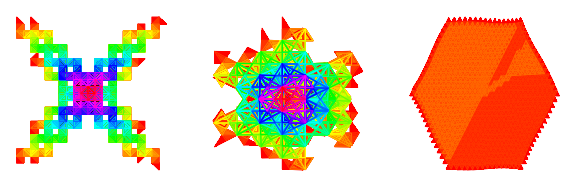

```mathematica
GraphicsRow[{showLengthIdeal[ST,30],showLengthIdeal[HT,30],showLengthIdeal[TT,30]},ImageSize->Large]
```

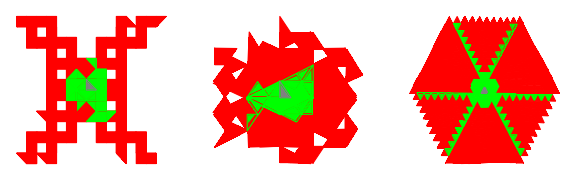

```mathematica
GraphicsRow[{showSmoothness[ST,20],showSmoothness[HT,20],showSmoothness[TT,20]},ImageSize->Large]
```

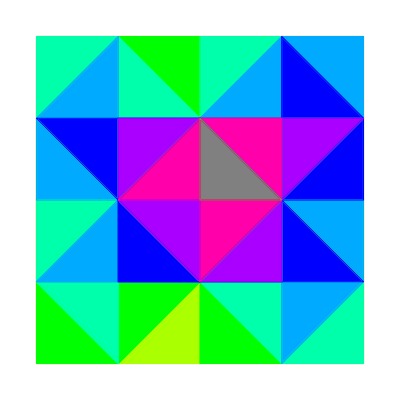
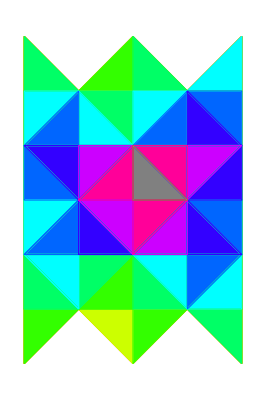
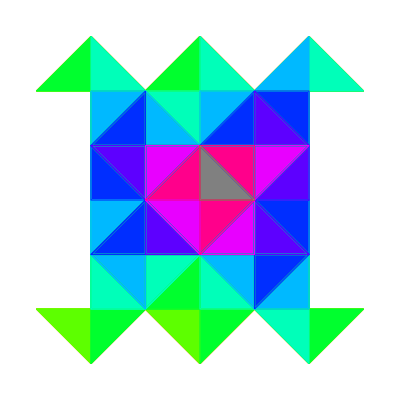
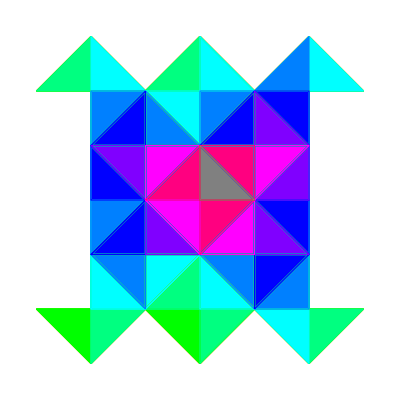
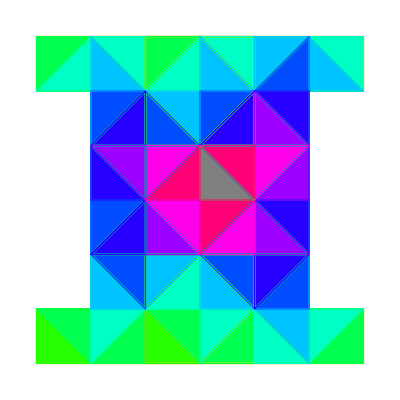
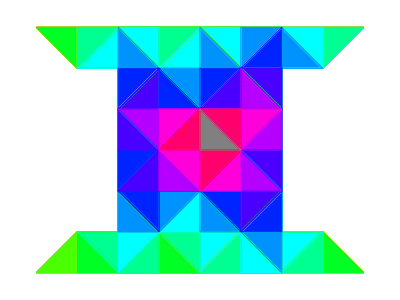
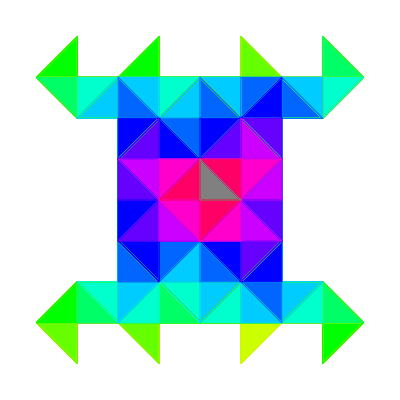
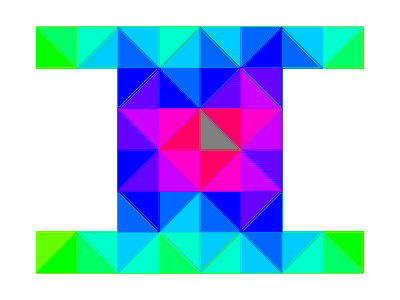

```mathematica
showNonSmoothBruhatIdeals[ST,15]
```

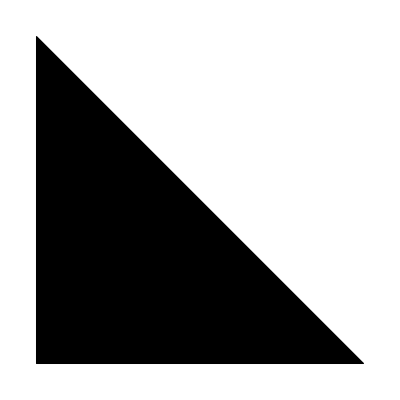
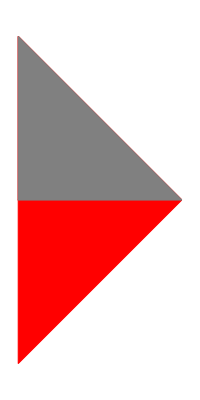
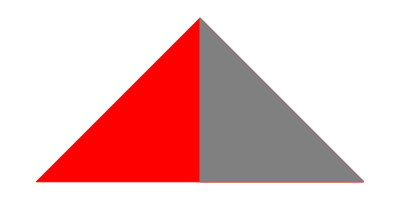
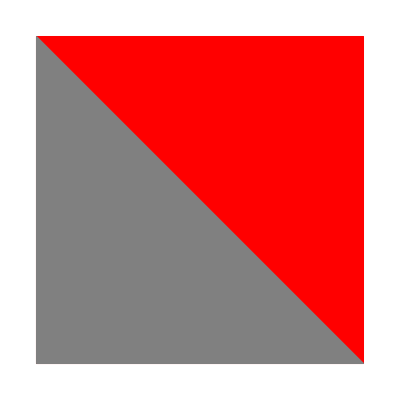
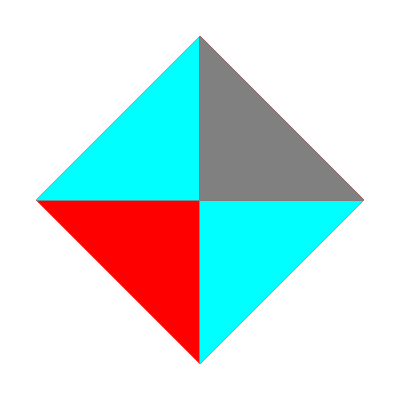
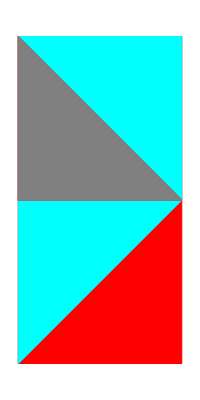
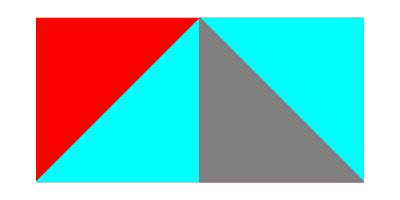
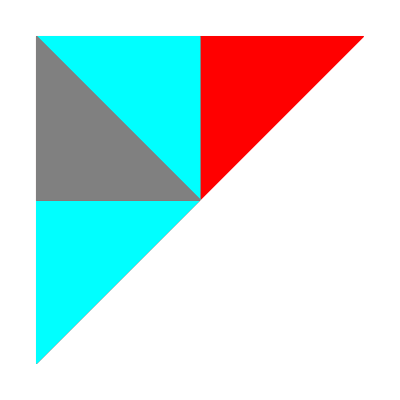
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
showSmoothBruhatIdeals[ST,15]
```

#### Hyperplane Arrangements

```mathematica
showHyperplanes[M_,k_]:=showHyperplanes[M,DeleteDuplicates[Flatten[inv[M,#]&/@Complement[words[M,k],words[M,k-1]]]]]
showInvArrangement[M_,""]:=showChambers[M,{""},Black]
showInvArrangement[M_,w_]:=Show[showHyperplanes[M,inv[M,w]],showChambers[M,{""},Black],showChambers[M,{w},Red]]
showInvArrangementBruhat[M_,w_]:=Show[showBruhatIdeal[M,w],showInvArrangement[M,w]]
showInvArrangementLeftBruhat[M_,w_]:=Show[showLeftBruhatIdeal[M,w],showInvArrangement[M,w]]
```

#### Hyperplane Arrangements Examples

```mathematica
GraphicsRow[{showInvArrangement[ST,"123123121"],showInvArrangementBruhat[ST,"123123121"],showInvArrangementLeftBruhat[ST,"123123121"]}]
```

-Graphics-

```mathematica
Show[showBruhatIdeal[TT,"123123123123123"],showHyperplanes[TT,inv[TT,"123123123123123"]]]
```

-Graphics-

## 2.5 Factorisation

### Polynomial Manipulation

```mathematica
zeroPolynomialQ[poly_,q_]:=CoefficientList[poly,q]=={}
polynomialDividesQ[poly1_,poly2_,q_]:=If[zeroPolynomialQ[PolynomialRemainder[poly1,poly2,q],q],True,False]
divideMult[m_,n_]:=Floor[m/n]
factorMults[factors1_,fac2_]:=divideMult[Select[factors1,#[[1]]==fac2[[1]]&][[1]][[2]],fac2[[2]]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=0/;Not[polynomialDividesQ[poly1,poly2,q]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=Module[{factors1,factors2,mult},
factors1=#&/@Complement[FactorList[poly1],{{1,1}}];
factors2=#&/@Complement[FactorList[poly2],{{1,1}}];
mult=factorMults[factors1,#]&/@factors2;
Min[mult]
]/;polynomialDividesQ[poly1,poly2,q]
removePolynomialFactors[poly1_,poly2_,q_]:=
Simplify[poly1/(poly2^polynomialDividesMultiplicity[poly1,poly2,q])]
removePolynomialFactors[poly1_,polyList_List,q_]:=
Simplify[poly1/Fold[Times,#^polynomialDividesMultiplicity[poly1,#,q]]&/@polyList]
```

### Quantum Factorisation

```mathematica
quantumPoly[k_,q_]:=Total[Table[( q)^i,{i,0,k}]]
quantumPolyQ[1,q_]:=True
quantumPolyQ[poly_,q_]:=CoefficientList[poly,q]==CoefficientList[quantumPoly[Max[1,Exponent[poly,q]],q],q]
quantumFactorQ[poly_,0,q_]:=True
quantumFactorQ[poly_,k_,q_]:=polynomialDividesQ[poly,quantumPoly[k,q],q]
quantumFactorsQ[poly_,q_]:=Fold[Or,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}]]
removeQuantumFactors[poly_,q_]:=removePolynomialFactors[poly,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}],q]
quantumFactorList[poly_,q_]:=Module[{d},
d=Max[1,Exponent[poly,q]];
Select[Table[{{k,q},polynomialDividesMultiplicity[poly,quantumPoly[k,q],q]},{k,1,d}],#[[2]]≥ 1&]
]
quantumFactorisation[poly_,q_]:=FactorList[poly]/;Not[quantumFactorsQ[poly,q]]
quantumFactorisation[poly_,q_]:=Module[{qfl,k,n,newP},
qfl=quantumFactorList[poly,q];
k=Max[#[[1]][[1]]&/@qfl];
n=polynomialDividesMultiplicity[poly,quantumPoly[k,q],q];
newP=removePolynomialFactors[poly,quantumPoly[k,q],q];
Join[quantumFactorisation[newP,q],{{quantumPoly[k,q],n}}]
]/;quantumFactorsQ[poly,q]
quantumFactorisationQ[poly_,q_]:=Fold[And,quantumPolyQ[#[[1]],q]&/@quantumFactorisation[poly,q]]
quantumFactorisationQ[M_List,w_String]:=quantumFactorisationQ[poincarePoly[M,w,q],q]
quantumFactorisationQ[M_List,wList_List]:=Fold[And,quantumFactorisationQ[poincarePoly[M,#,q],q]&/@wList]
quantumExponents[poly_,q_]:=If[quantumFactorisationQ[poly,q],Drop[Flatten[Table[Exponent[#[[1]],q],{i,1,#[[2]]}]&/@quantumFactorisation[poly,q]],1],{}]
quantumExponents[M_List,w_String]:=quantumExponents[poincarePoly[M,w,q],q]
quantumExponents[M_List,wList_List]:={#,quantumExponents[poincarePoly[M,#,q],q]}&/@wList
```

### q-Factorisation Property

```mathematica
qFactorisationProperty[M_,k_]:=
qFactorisationProperty[M,k]={#,quantumFactorisationQ[M,#]}&/@smoothElements[M,k]
qFactorisationPropertyQ[M_,k_]:=Fold[And,#[[2]]&/@qFactorisationProperty[M,k]]
qFactorisationPropertyQ[M_]:=qFactorisationPropertyQ[M,maxLength[M]]
```

H3

```mathematica
qFactorisationPropertyQ[H3]
```

True

H4

```mathematica
qFactorisationPropertyQ[H4,15]
```

$Aborted

F4

```mathematica
qFactorisationPropertyQ[F4,24]
```

True

### Visualisation

```mathematica
lexOrder[list1_,list2_]:=If[list1[[1]]<list2[[1]],True,If[list1[[1]]==list2[[1]],lexOrder[Drop[list1,1],Drop[list2,1]],False]]
lexOrder[{},list_]:=True
lexOrder[list_,{}]:=False/;Not[list=={}]
quantumExponentsVisualisation[M_,k_]:=Sort[{#,quantumExponents[poincarePoly[M,#,q],q],showInvArrangement[M,#]}&/@smoothElements[M,k],lexOrder[#1[[2]],#2[[2]]]&]
```

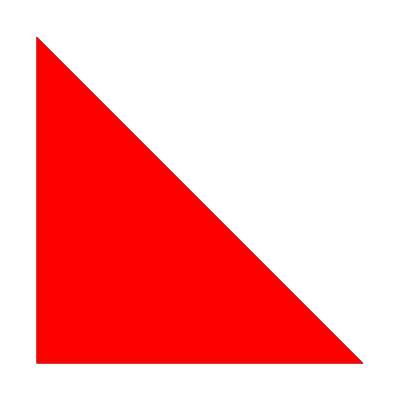
{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{2313,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{3123,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{13123,{1,1,3},-Graphics-},{21313,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{313,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{121231,{1,2,3},-Graphics-},{121313,{1,2,3},-Graphics-},{123121,{1,2,3},-Graphics-},{131231,{1,2,3},-Graphics-},{1212,{1,3},-Graphics-},{1313,{1,3},-Graphics-},{1212312,{1,3,3},-Graphics-},{1212313,{1,3,3},-Graphics-},{1312312,{1,3,3},-Graphics-},{1312313,{1,3,3},-Graphics-},{2123121,{1,3,3},-Graphics-},{3121313,{1,3,3},-Graphics-},{12123121,{1,3,4},-Graphics-},{13121313,{1,3,4},-Graphics-}}

```mathematica
quantumExponentsVisualisation[ST,15]
```

```mathematica
quantumExponentsVisualisation[HT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{21213,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{31212,{1,1,3},-Graphics-},{121213,{1,1,4},-Graphics-},{212123,{1,1,4},-Graphics-},{231212,{1,1,4},-Graphics-},{312121,{1,1,4},-Graphics-},{1212123,{1,1,5},-Graphics-},{2312121,{1,1,5},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{131212,{1,2,3},-Graphics-},{131213,{1,2,3},-Graphics-},{212131,{1,2,3},-Graphics-},{1212131,{1,2,4},-Graphics-},{1312121,{1,2,4},-Graphics-},{12121231,{1,2,5},-Graphics-},{12312121,{1,2,5},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{121212312,{1,3,5},-Graphics-},{212312121,{1,3,5},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{1212123121,{1,4,5},-Graphics-},{1212312121,{1,4,5},-Graphics-},{121212,{1,5},-Graphics-},{12121231212,{1,5,5},-Graphics-},{12121231213,{1,5,5},-Graphics-},{13121231212,{1,5,5},-Graphics-},{21212312121,{1,5,5},-Graphics-},{121212312121,{1,5,6},-Graphics-}}

```mathematica
quantumExponentsVisualisation[TT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{32,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{132,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{321,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1232,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2321,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{232,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{12132,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{13123,{1,2,2},-Graphics-},{23121,{1,2,2},-Graphics-},{23213,{1,2,2},-Graphics-},{1213123,{2,2,3},-Graphics-},{1213213,{2,2,3},-Graphics-},{1312132,{2,2,3},-Graphics-},{1312312,{2,2,3},-Graphics-},{2312131,{2,2,3},-Graphics-},{2321321,{2,2,3},-Graphics-},{121312312,{2,3,4},-Graphics-},{121321321,{2,3,4},-Graphics-},{131213213,{2,3,4},-Graphics-},{131231231,{2,3,4},-Graphics-},{231213123,{2,3,4},-Graphics-},{232132132,{2,3,4},-Graphics-},{12131231231,{2,4,5},-Graphics-},{12132132132,{2,4,5},-Graphics-},{13121321321,{2,4,5},-Graphics-},{13123123123,{2,4,5},-Graphics-},{23121312312,{2,4,5},-Graphics-},{23213213213,{2,4,5},-Graphics-},{1213123123123,{2,5,6},-Graphics-},{1213213213213,{2,5,6},-Graphics-},{1312132132132,{2,5,6},-Graphics-},{1312312312312,{2,5,6},-Graphics-},{2312131231231,{2,5,6},-Graphics-},{2321321321321,{2,5,6},-Graphics-},{121312312312312,{2,6,7},-Graphics-},{121321321321321,{2,6,7},-Graphics-},{131213213213213,{2,6,7},-Graphics-},{131231231231231,{2,6,7},-Graphics-},{231213123123123,{2,6,7},-Graphics-},{232132132132132,{2,6,7},-Graphics-}}

```mathematica
quantumExponentsVisualisation[I2[12],12]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{12,{1,1},-Graphics-},{21,{1,1},-Graphics-},{121,{1,2},-Graphics-},{212,{1,2},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{121212,{1,5},-Graphics-},{212121,{1,5},-Graphics-},{1212121,{1,6},-Graphics-},{2121212,{1,6},-Graphics-},{12121212,{1,7},-Graphics-},{21212121,{1,7},-Graphics-},{121212121,{1,8},-Graphics-},{212121212,{1,8},-Graphics-},{1212121212,{1,9},-Graphics-},{2121212121,{1,9},-Graphics-},{12121212121,{1,10},-Graphics-},{21212121212,{1,10},-Graphics-},{121212121212,{1,11},-Graphics-}}

### Conjectures

```mathematica
letterCount[w_String]:=Sort[Union[makeList[w]]/.CharacterCounts[w]]
letterCounts[M_,w_String]:=DeleteDuplicates[letterCount[#]&/@reduce[M,w]]
centralGeneratorCount[M_,w_,s_]:=Length[Select[Sort[centralGenerator[#]&/@inv[M,w]],#==s&]]
centralGeneratorCounts[M_,w_]:=Sort[Select[Table[centralGeneratorCount[M,w,ToString[i]],{i,1,rank[M]}],Not[#==0]&]]
```

```mathematica
{#,letterCounts[TT,#][[1]]==quantumExponents[TT,#],centralGeneratorCounts[TT,#]==quantumExponents[TT,#]}&/@smoothElements[TT,15]
```

{{,True,True},{1,True,True},{12,True,True},{121,True,True},{1213,True,True},{12131,False,True},{1213123,True,False},{121312312,True,True},{12131231231,False,False},{1213123123123,False,False},{121312312312312,False,False},{12132,True,True},{1213213,True,True},{121321321,True,True},{12132132132,False,False},{1213213213213,False,False},{121321321321321,False,False},{123,True,True},{1232,True,True},{13,True,True},{131,True,True},{1312,True,True},{13121,False,True},{1312132,True,False},{131213213,True,True},{13121321321,False,False},{1312132132132,False,False},{131213213213213,False,False},{13123,True,True},{1312312,True,True},{131231231,True,True},{13123123123,False,False},{1312312312312,False,False},{131231231231231,False,False},{132,True,True},{2,True,True},{21,True,True},{213,True,True},{2131,True,True},{23,True,True},{231,True,True},{23121,True,True},{2312131,True,False},{231213123,False,False},{23121312312,False,False},{2312131231231,False,False},{231213123123123,False,False},{232,True,True},{2321,True,True},{23213,True,True},{2321321,True,True},{232132132,True,True},{23213213213,False,False},{2321321321321,False,False},{232132132132132,False,False},{3,True,True},{31,True,True},{312,True,True},{3121,True,True},{32,True,True},{321,True,True}}

```mathematica
centralGeneratorCounts[H3,#]&/@reduce[H3,"123123123123123"]
```

{{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8}}

## 2.6 Bruhat ideals

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
```

Type A[5]

```mathematica
bruhatIdeal[typeA[5],w[typeA[5],3]]={"","4","5","1","3","2","54","34","45","24","14","43","15","35","23","13","12","32","21","25","234","354","543","254","154","454","345","324","134","343","245","145","435","243","143","124","432","214","235","135","125","325","215","232","132","213","121","321","123","2354","2324","2134","2343","4354","3543","3254","1354","3454","2543","1543","2454","1454","2154","1254","4543","3245","1345","3435","3243","1343","1324","3432","3214","2435","1435","1245","2432","1432","2143","1243","1214","4325","2145","2325","1325","2135","1215","2321","1321","2132","1232","1213","3215","1235","24354","23254","21354","23543","23243","21343","21324","23432","23214","43543","43254","34354","14354","32543","13543","32454","13454","32154","13254","24543","14543","21543","12543","21454","12454","12154","34543","32435","13435","13245","32432","13432","32143","13243","13214","24325","14325","21435","12435","12145","21432","12432","12143","23215","13215","21325","12325","12135","21321","12321","12132","34325","32145","324354","243543","243254","214354","232543","213543","232154","213254","232432","213432","232143","213243","213214","432543","343543","143543","343254","143254","134354","324543","134543","321543","132543","321454","132454","132154","214543","124543","121543","121454","324325","134325","321435","132435","132145","321432","132432","132143","214325","124325","121435","121432","213215","123215","121325","121321","3243543","3243254","3214354","2432543","2143543","2143254","2321543","2132543","2132154","2321432","2132432","2132143","3432543","1432543","1343543","1343254","3214543","1324543","1321543","1321454","1214543","3214325","1324325","1321435","1321432","1214325","1213215","32432543","32143543","32143254","21432543","21321543","21321432","13432543","13214543","13214325","321432543"};
```

Type B[5]

```mathematica
bruhatIdeal[typeB[5],w[typeB[5],3]]={"","5","4","1","3","2","54","45","15","35","25","43","14","34","23","13","12","32","21","24","545","543","454","154","354","254","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5435","4545","1545","3545","2545","4543","1543","3543","2543","4354","1454","3454","2354","1354","1254","3254","2154","2454","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","54354","45435","15435","35435","25435","43545","14545","34545","23545","13545","12545","32545","21545","24545","43543","14543","34543","23543","13543","12543","32543","21543","24543","43254","14354","34354","23454","13454","12454","32454","21454","23254","13254","21354","12154","32154","12354","24354","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","13214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","543545","454354","154354","354354","254354","435435","145435","345435","235435","135435","125435","325435","215435","245435","432545","143545","343545","234545","134545","124545","324545","214545","232545","132545","213545","121545","321545","123545","243545","432543","143543","343543","234543","134543","124543","324543","214543","232543","132543","213543","121543","321543","123543","243543","143254","343254","234354","134354","124354","324354","214354","232454","132454","213454","121454","132154","213254","123254","121354","321454","123454","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","132145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243254","232154","4543545","1543545","3543545","2543545","4354354","1454354","3454354","2354354","1354354","1254354","3254354","2154354","2454354","4325435","1435435","3435435","2345435","1345435","1245435","3245435","2145435","2325435","1325435","2135435","1215435","3215435","1235435","2435435","1432545","3432545","2343545","1343545","1243545","3243545","2143545","2324545","1324545","2134545","1214545","1321545","2132545","1232545","1213545","3214545","1234545","2432545","2321545","1432543","3432543","2343543","1343543","1243543","3243543","2143543","2324543","1324543","2134543","1214543","1321543","2132543","1232543","1213543","3214543","1234543","2343254","1343254","1243254","3243254","2143254","2324354","1324354","2134354","1214354","2321454","1321454","2132454","1232454","1213454","1232154","1213254","3214354","2132154","1234354","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","3214325","1234325","1232145","2432543","2321543","2321432","43543545","14543545","34543545","23543545","13543545","12543545","32543545","21543545","24543545","43254354","14354354","34354354","23454354","13454354","12454354","32454354","21454354","23254354","13254354","21354354","12154354","32154354","12354354","24354354","14325435","34325435","23435435","13435435","12435435","32435435","21435435","23245435","13245435","21345435","12145435","13215435","21325435","12325435","12135435","32145435","12345435","23432545","13432545","12432545","32432545","21432545","23243545","13243545","21343545","12143545","23214545","13214545","21324545","12324545","12134545","12321545","12132545","32143545","21321545","12343545","24325435","23215435","23432543","13432543","12432543","32432543","21432543","23243543","13243543","21343543","12143543","23214543","13214543","21324543","12324543","12134543","12321543","12132543","32143543","21321543","12343543","23243254","13243254","21343254","12143254","23214354","13214354","21324354","12324354","12134354","21321454","12132454","12132154","23214325","21324325","12324325","12134325","21321435","12321435","12132435","12132145","12321432","12132432","12132143","32143254","21321432","12343254","12321454","13214325","432543545","143543545","343543545","234543545","134543545","124543545","324543545","214543545","232543545","132543545","213543545","121543545","321543545","123543545","243543545","143254354","343254354","234354354","134354354","124354354","324354354","214354354","232454354","132454354","213454354","121454354","132154354","213254354","123254354","121354354","321454354","123454354","234325435","134325435","124325435","324325435","214325435","232435435","132435435","213435435","121435435","232145435","132145435","213245435","123245435","121345435","123215435","121325435","321435435","213215435","123435435","232432545","132432545","213432545","121432545","232143545","132143545","213243545","123243545","121343545","213214545","121324545","121321545","321432545","123432545","123214545","243254354","232154354","232432543","132432543","213432543","121432543","232143543","132143543","213243543","123243543","121343543","213214543","121324543","121321543","232143254","132143254","213243254","123243254","121343254","213214354","123214354","121324354","121321454","213214325","121324325","121321435","121321432","321432543","123432543","123214543","123214325","1432543545","3432543545","2343543545","1343543545","1243543545","3243543545","2143543545","2324543545","1324543545","2134543545","1214543545","1321543545","2132543545","1232543545","1213543545","3214543545","1234543545","2343254354","1343254354","1243254354","3243254354","2143254354","2324354354","1324354354","2134354354","1214354354","2321454354","1321454354","2132454354","1232454354","1213454354","1232154354","1213254354","3214354354","2132154354","1234354354","2324325435","1324325435","2134325435","1214325435","2321435435","1321435435","2132435435","1232435435","1213435435","2132145435","1213245435","1213215435","1321432545","2132432545","1232432545","1213432545","2132143545","1232143545","1213243545","1213214545","3214325435","1234325435","1232145435","2321432543","1321432543","2132432543","1232432543","1213432543","2132143543","1232143543","1213243543","1213214543","1232143254","1213243254","1213214354","1213214325","2432543545","2321543545","2321432545","2132143254","23432543545","13432543545","12432543545","32432543545","21432543545","23243543545","13243543545","21343543545","12143543545","23214543545","13214543545","21324543545","12324543545","12134543545","12321543545","12132543545","32143543545","21321543545","12343543545","23243254354","13243254354","21343254354","12143254354","23214354354","13214354354","21324354354","12324354354","12134354354","21321454354","12132454354","12132154354","23214325435","13214325435","21324325435","12324325435","12134325435","21321435435","12321435435","12132435435","12132145435","12321432545","12132432545","12132143545","32143254354","21321432545","12343254354","12321454354","21321432543","12321432543","12132432543","12132143543","12132143254","232432543545","132432543545","213432543545","121432543545","232143543545","132143543545","213243543545","123243543545","121343543545","213214543545","121324543545","121321543545","232143254354","132143254354","213243254354","123243254354","121343254354","213214354354","123214354354","121324354354","121321454354","213214325435","121324325435","121321435435","121321432545","321432543545","123432543545","123214543545","123214325435","121321432543","2321432543545","1321432543545","2132432543545","1232432543545","1213432543545","2132143543545","1232143543545","1213243543545","1213214543545","2132143254354","1232143254354","1213243254354","1213214354354","1213214325435","21321432543545","12321432543545","12132432543545","12132143543545","12132143254354","121321432543545"};
```

Type D[5]

```mathematica
bruhatIdeal[typeD[5],w[typeD[5],3]]={"","5","4","1","3","2","53","45","15","35","25","43","14","34","23","13","12","32","21","24","534","532","453","153","353","253","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5324","4534","1534","3534","2534","4532","1532","3532","2532","4353","1453","3453","2353","1353","1253","3253","2153","2453","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","53243","45324","15324","35324","25324","43534","14534","34534","23534","13534","12534","32534","21534","24534","43532","14532","34532","23532","13532","12532","32532","21532","24532","43253","14353","34353","23453","13453","12453","32453","21453","23253","13253","21353","12153","32153","12353","24353","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","13214","532435","453243","153243","353243","253243","435324","145324","345324","235324","135324","125324","325324","215324","245324","432534","143534","343534","234534","134534","124534","324534","214534","232534","132534","213534","121534","321534","123534","243534","432532","143532","343532","234532","134532","124532","324532","214532","232532","132532","213532","121532","321532","123532","243532","143253","343253","234353","134353","124353","324353","214353","232453","132453","213453","121453","132153","213253","123253","121353","321453","123453","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243253","232153","132143","132145","4532435","1532435","3532435","2532435","4353243","1453243","3453243","2353243","1353243","1253243","3253243","2153243","2453243","4325324","1435324","3435324","2345324","1345324","1245324","3245324","2145324","2325324","1325324","2135324","1215324","3215324","1235324","2435324","1432534","3432534","2343534","1343534","1243534","3243534","2143534","2324534","1324534","2134534","1214534","1321534","2132534","1232534","1213534","3214534","1234534","2432534","2321534","1432532","3432532","2343532","1343532","1243532","3243532","2143532","2324532","1324532","2134532","1214532","1321532","2132532","1232532","1213532","3214532","1234532","2343253","1343253","1243253","3243253","2143253","2324353","1324353","2134353","1214353","2321453","1321453","2132453","1232453","1213453","1232153","1213253","3214353","2132153","1234353","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","2321432","1321432","2132432","1232432","1213432","2132143","1213243","1213214","3214325","1234325","1232145","2432532","2321532","1232143","43532435","14532435","34532435","23532435","13532435","12532435","32532435","21532435","24532435","43253243","14353243","34353243","23453243","13453243","12453243","32453243","21453243","23253243","13253243","21353243","12153243","32153243","12353243","24353243","14325324","34325324","23435324","13435324","12435324","32435324","21435324","23245324","13245324","21345324","12145324","13215324","21325324","12325324","12135324","32145324","12345324","23432534","13432534","12432534","32432534","21432534","23243534","13243534","21343534","12143534","23214534","13214534","21324534","12324534","12134534","12321534","12132534","32143534","21321534","12343534","23432532","13432532","12432532","32432532","21432532","23243532","13243532","21343532","12143532","23214532","13214532","21324532","12324532","12134532","12321532","12132532","32143532","21321532","12343532","23243253","13243253","21343253","12143253","23214353","13214353","21324353","12324353","12134353","12132453","12132153","23214325","13214325","21324325","12324325","12134325","12321435","12132435","12132145","21321432","12132432","12132143","32143253","12343253","12321453","12321432","24325324","23215324","21321435","21321453","432532435","143532435","343532435","234532435","134532435","124532435","324532435","214532435","232532435","132532435","213532435","121532435","321532435","123532435","243532435","143253243","343253243","234353243","134353243","124353243","324353243","214353243","232453243","132453243","213453243","121453243","132153243","213253243","123253243","121353243","321453243","123453243","234325324","134325324","124325324","324325324","214325324","232435324","132435324","213435324","121435324","232145324","132145324","213245324","123245324","121345324","123215324","121325324","321435324","213215324","123435324","232432534","132432534","213432534","121432534","232143534","132143534","213243534","123243534","121343534","213214534","121324534","121321534","321432534","123432534","123214534","232432532","132432532","213432532","121432532","232143532","132143532","213243532","123243532","121343532","213214532","121324532","121321532","232143253","132143253","213243253","123243253","121343253","123214353","121324353","121321453","213214325","123214325","121324325","121321432","321432532","123432532","123214532","121321435","243253243","232153243","213214353","1432532435","3432532435","2343532435","1343532435","1243532435","3243532435","2143532435","2324532435","1324532435","2134532435","1214532435","1321532435","2132532435","1232532435","1213532435","3214532435","1234532435","2343253243","1343253243","1243253243","3243253243","2143253243","2324353243","1324353243","2134353243","1214353243","2321453243","1321453243","2132453243","1232453243","1213453243","1232153243","1213253243","3214353243","2132153243","1234353243","2324325324","1324325324","2134325324","1214325324","2321435324","1321435324","2132435324","1232435324","1213435324","2132145324","1213245324","1213215324","1321432534","2132432534","1232432534","1213432534","2132143534","1232143534","1213243534","1213214534","2321432532","1321432532","2132432532","1232432532","1213432532","2132143532","1232143532","1213243532","2132143253","1232143253","1213243253","1213214353","1213214325","3214325324","1234325324","1232145324","2432532435","2321532435","2321432534","1213214532","23432532435","13432532435","12432532435","32432532435","21432532435","23243532435","13243532435","21343532435","12143532435","23214532435","13214532435","21324532435","12324532435","12134532435","12321532435","12132532435","32143532435","21321532435","12343532435","23243253243","13243253243","21343253243","12143253243","23214353243","13214353243","21324353243","12324353243","12134353243","21321453243","12132453243","12132153243","23214325324","13214325324","21324325324","12324325324","12134325324","21321435324","12321435324","12132435324","12132145324","12321432534","12132432534","12132143534","21321432532","12321432532","12132432532","12132143253","32143253243","21321432534","12343253243","12321453243","12132143532","232432532435","132432532435","213432532435","121432532435","232143532435","132143532435","213243532435","123243532435","121343532435","213214532435","121324532435","121321532435","232143253243","132143253243","213243253243","123243253243","121343253243","213214353243","123214353243","121324353243","121321453243","213214325324","121324325324","121321435324","121321432534","121321432532","321432532435","123432532435","123214532435","123214325324","2321432532435","1321432532435","2132432532435","1232432532435","1213432532435","2132143532435","1232143532435","1213243532435","1213214532435","2132143253243","1232143253243","1213243253243","1213214353243","1213214325324","21321432532435","12321432532435","12132432532435","12132143532435","12132143253243","121321432532435"};
```

F4

```mathematica
bruhatIdeal[F4,w[F4,3]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","1432","3432","2432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","14323","34323","24323","13432","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","143234","343234","243234","134323","324323","214323","323432","232432","132432","213432","121432","321432","123432","234323","124323","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121323","121321","1343234","3243234","2143234","3234323","2324323","1324323","2134323","1214323","3214323","1234323","2323432","1323432","2321432","1321432","2132432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1213214","2132132","1232132","2343234","1243234","1232134","1213213","32343234","23243234","13243234","21343234","12143234","32143234","12343234","23234323","13234323","23214323","13214323","21324323","12324323","12134323","23213432","13213432","21323432","12323432","21321432","12321432","12132432","32134323","23213243","13213243","21321343","12132343","23213234","13213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","232343234","132343234","232143234","132143234","213243234","123243234","121343234","232134323","132134323","213234323","123234323","213214323","123214323","121324323","213213432","123213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","123213234","121321324","121321323","321343234","121321432","2321343234","1321343234","2132343234","1232343234","2132143234","1232143234","1213243234","2132134323","1232134323","1213234323","1213214323","1213213432","2132132343","1232132343","1213213243","1213213234","21321343234","12321343234","12132343234","12132143234","12132134323","12132132343","121321343234"};
bruhatIdeal[F4,w[F4,4]]={"","4","1","3","2","43","34","24","14","23","13","12","32","21","432","343","243","143","324","214","234","124","323","134","232","132","213","121","321","123","4321","4323","3432","2432","1432","3243","2143","2343","1243","1343","3234","1324","2134","1214","3214","1234","2324","1323","3213","2323","2321","1321","2132","1232","1213","43234","43213","14321","34321","24321","34323","24323","14323","32432","21432","23432","12432","32343","21343","12143","32143","12343","23243","13432","13234","23214","13214","12324","12134","32134","23213","13213","12323","32132","21323","23234","21321","12321","12132","21324","13243","432134","343234","243234","143234","432132","143213","343213","243213","134321","324321","214321","234321","124321","324323","214323","234323","124323","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232343","213243","232134","132134","123234","213214","121324","321324","213234","123214","232132","132132","213213","121323","321323","123213","134323","121321","4321324","1432134","3432134","2432134","1343234","3243234","2143234","2343234","1243234","4321323","1432132","3432132","2432132","1343213","3243213","2143213","3234321","2324321","1324321","2134321","1214321","3214321","1234321","2343213","1243213","3234323","1324323","2134323","1214323","3214323","1234323","2324323","1323432","2321432","1321432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2323432","2132432","2321324","1321324","2132134","1213234","2321323","1321323","2132132","1232132","1213213","3213234","1232134","1213214","43213243","43213234","14321324","34321324","24321324","13432134","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","14321323","34321323","24321323","13432132","32432132","21432132","32343213","23243213","13243213","21343213","12143213","32143213","12343213","23234321","13234321","23214321","13214321","21324321","12324321","12134321","32134321","23432132","12432132","13234323","23214323","13214323","12324323","12134323","32134323","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","32132343","12321343","12132143","23213234","13213234","21321324","12321324","12132134","21321323","12321323","12132132","23234323","21324323","432132343","143213243","343213243","243213243","143213234","343213234","243213234","134321324","324321324","214321324","323432134","232432134","132432134","213432134","121432134","321432134","123432134","232343234","132343234","232143234","132143234","213243234","123243234","121343234","321343234","234321324","124321324","134321323","324321323","214321323","234321323","124321323","323432132","232432132","132432132","213432132","121432132","321432132","123432132","232343213","132343213","232143213","132143213","213243213","123243213","121343213","232134321","132134321","213234321","123234321","213214321","123214321","121324321","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","321323432","123213432","121321432","213213234","123213234","121321324","121321323","1432132343","3432132343","2432132343","1343213243","3243213243","2143213243","2343213243","1243213243","1343213234","3243213234","2143213234","3234321324","2324321324","1324321324","2134321324","1214321324","3214321324","1234321324","2323432134","1323432134","2321432134","1321432134","2132432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","3234321323","2324321323","1324321323","2134321323","1214321323","3214321323","1234321323","2343213234","1243213234","2323432132","1323432132","2321432132","1321432132","2132432132","1232432132","1213432132","2321343213","1321343213","2132343213","1232343213","2132143213","1232143213","1213243213","2132134321","1232134321","1213214321","3213432132","1213234321","2321324323","1321324323","2132134323","1213234323","2321323432","1321323432","2132132432","1232132432","1213213432","2132132343","1213213243","3213234323","1232134323","1232132343","1213214323","1213213234","13432132343","32432132343","21432132343","32343213243","23243213243","13243213243","21343213243","12143213243","32143213243","12343213243","32132343234","32343213234","23243213234","13243213234","21343213234","12143213234","32143213234","12343213234","23234321324","13234321324","23214321324","13214321324","21324321324","12324321324","12134321324","23213432134","13213432134","21323432134","12323432134","21321432134","12321432134","23213243234","13213243234","21321343234","12321343234","12132343234","12132143234","32134321324","23234321323","13234321323","23214321323","13214321323","21324321323","12324321323","12134321323","32134321323","23213432132","13213432132","21323432132","12323432132","21321432132","12321432132","12132432132","21321343213","12321343213","12132343213","12132134321","23213234323","13213234323","21321324323","12321324323","12132134323","21321323432","12321323432","12132132432","12132132343","23432132343","12432132343","12132432134","12132143213","323432132343","232432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232343213243","132343213243","232143213243","132143213243","213243213243","123243213243","121343213243","232132343234","132132343234","321343213243","232343213234","132343213234","232143213234","132143213234","213243213234","123243213234","121343213234","232134321324","132134321324","213234321324","123234321324","213214321324","123214321324","121324321324","213213432134","123213432134","121321432134","123213243234","121321343234","232134321323","132134321323","213234321323","123234321323","213214321323","123214321323","121324321323","321343213234","213213243234","121323432134","213213432132","123213432132","121323432132","121321432132","121321343213","213213234323","123213234323","121321324323","121321323432","2323432132343","1323432132343","2321432132343","1321432132343","2132432132343","1232432132343","1213432132343","2321343213243","1321343213243","2132343213243","1232343213243","2132143213243","1232143213243","1213243213243","1232132343234","2321343213234","1321343213234","2132343213234","1232343213234","2132143213234","1232143213234","1213243213234","2132134321324","1232134321324","1213234321324","1213214321324","1213213432134","1213213243234","2132134321323","1232134321323","1213234321323","1213214321323","3213432132343","2132132343234","1213213432132","1213213234323","23213432132343","13213432132343","21323432132343","12323432132343","21321432132343","12321432132343","12132432132343","21321343213243","12321343213243","12132343213243","12132143213243","12132132343234","21321343213234","12321343213234","12132343213234","12132143213234","12132134321324","12132134321323","213213432132343","123213432132343","121323432132343","121321432132343","121321343213243","121321343213234","1213213432132343"};
bruhatIdeal[F4,w[F4,5]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","4321","3432","2432","1432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","43213","34323","24323","14323","34321","24321","14321","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","13432","432134","343234","243234","143234","432132","343213","243213","143213","324323","214323","234323","124323","134323","324321","214321","234321","124321","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121321","134321","121323","4321324","3432134","2432134","1432134","3243234","2143234","2343234","1243234","1343234","4321323","3432132","2432132","1432132","3243213","2143213","2343213","1243213","3234323","1324323","2134323","3214323","1234323","2324323","1343213","3234321","1324321","2134321","1214321","3214321","1234321","2324321","1323432","2321432","1321432","1232432","1213432","3213432","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1232134","1213214","2132132","1232132","2323432","2132432","1213213","2321343","1214323","43213243","43213234","34321324","24321324","14321324","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","13432134","34321323","24321323","14321323","32432132","21432132","23432132","12432132","32343213","13243213","21343213","12143213","32143213","12343213","23243213","13234323","23214323","13214323","12324323","12134323","32134323","23234323","21324323","13432132","13234321","23214321","13214321","12324321","12134321","32134321","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","23213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","23234321","21324321","13213234","432132432","432132343","343213243","243213243","143213243","343213234","243213234","143213234","324321324","214321324","234321324","124321324","323432134","132432134","213432134","121432134","321432134","123432134","232432134","132343234","232143234","123243234","121343234","321343234","232343234","213243234","134321324","324321323","214321323","234321323","124321323","323432132","132432132","213432132","121432132","321432132","123432132","232432132","132343213","232143213","132143213","123243213","121343213","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232343213","213243213","134321323","232134321","132134321","123234321","213214321","121324321","321324321","213234321","123214321","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","121321324","121321323","321323432","123213234","121321432","132143234","123213432","4321323432","3432132432","2432132432","1432132432","3432132343","2432132343","1432132343","3243213243","2143213243","2343213243","1243213243","1343213243","3243213234","2143213234","2343213234","1243213234","3234321324","1324321324","2134321324","1214321324","3214321324","1234321324","2324321324","1323432134","2321432134","1321432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","2323432134","2132432134","3234321323","1324321323","2134321323","1214321323","3214321323","1234321323","2324321323","1323432132","2321432132","1321432132","1232432132","1213432132","3213432132","2321343213","1321343213","1232343213","2132143213","1213243213","3213243213","2132343213","1232143213","2321324323","1321324323","2132134323","1213234323","3213234323","1232134323","1213214323","2323432132","2132432132","1343213234","2321324321","1321324321","2132134321","1213234321","2321323432","1321323432","2132132432","1232132432","1213213432","1232132343","1213213243","1213213234","3213234321","2132132343","1232134321","1213214321","43213234323","34321323432","24321323432","14321323432","32432132432","21432132432","23432132432","12432132432","13432132432","32432132343","21432132343","23432132343","12432132343","32343213243","13243213243","21343213243","12143213243","32143213243","12343213243","23243213243","13432132343","32343213234","13243213234","21343213234","12143213234","32143213234","12343213234","23243213234","13234321324","23214321324","13214321324","12324321324","12134321324","32134321324","23213432134","13213432134","12323432134","21321432134","12132432134","32132432134","21323432134","12321432134","23213243234","13213243234","21321343234","12132343234","32132343234","12321343234","12132143234","23234321324","21324321324","13234321323","23214321323","13214321323","12324321323","12134321323","32134321323","23213432132","13213432132","12323432132","21321432132","12132432132","32132432132","21323432132","12321432132","23213243213","13213243213","21321343213","12132343213","23213234323","21321324323","12321324323","12132134323","32132343213","12321343213","12132143213","23234321323","21324321323","13213234323","23213234321","13213234321","21321324321","12321324321","12132134321","21321323432","12321323432","12132132432","12132132343","343213234323","243213234323","143213234323","324321323432","214321323432","234321323432","124321323432","323432132432","132432132432","213432132432","121432132432","321432132432","123432132432","232432132432","323432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232432132343","132343213243","232143213243","132143213243","123243213243","121343213243","321343213243","232343213243","213243213243","134321323432","132343213234","232143213234","132143213234","123243213234","121343213234","321343213234","232134321324","132134321324","123234321324","213214321324","121324321324","321324321324","213234321324","123214321324","232132432134","132132432134","213213432134","121323432134","232132343234","213213243234","123213243234","121321343234","321323432134","123213432134","121321432134","232134321323","132134321323","123234321323","213214321323","121324321323","321324321323","213234321323","123214321323","232132432132","132132432132","213213432132","121323432132","232132343213","132132343213","213213243213","123213243213","121321343213","213213234323","121321324323","321323432132","123213432132","123213234323","121321432132","232343213234","213243213234","132132343234","213213234321","123213234321","121321324321","121321323432","3243213234323","2143213234323","2343213234323","1243213234323","3234321323432","1324321323432","2134321323432","1214321323432","3214321323432","1234321323432","2324321323432","1323432132432","2321432132432","1321432132432","1232432132432","1213432132432","3213432132432","2323432132432","2132432132432","1323432132343","2321432132343","1321432132343","1232432132343","1213432132343","3213432132343","2321343213243","1321343213243","1232343213243","2132143213243","1213243213243","3213243213243","2132343213243","1232143213243","2323432132343","2132432132343","2321343213234","1321343213234","1232343213234","2132143213234","1213243213234","3213243213234","2132343213234","1232143213234","2321324321324","1321324321324","2132134321324","1213234321324","2321323432134","1321323432134","2132132432134","1232132432134","1213213432134","2132132343234","1213213243234","3213234321324","1232134321324","1232132343234","1213214321324","2321324321323","1321324321323","2132134321323","1213234321323","2321323432132","1321323432132","2132132432132","1232132432132","1213213432132","1232132343213","1213213243213","1213213234323","3213234321323","2132132343213","1232134321323","1213214321323","1343213234323","1213213234321","32343213234323","13243213234323","21343213234323","12143213234323","32143213234323","12343213234323","23243213234323","13234321323432","23214321323432","13214321323432","12324321323432","12134321323432","32134321323432","23213432132432","13213432132432","12323432132432","21321432132432","12132432132432","32132432132432","21323432132432","12321432132432","23213432132343","13213432132343","12323432132343","21321432132343","12132432132343","32132432132343","21323432132343","12321432132343","23213243213243","13213243213243","21321343213243","12132343213243","32132343213243","12321343213243","12132143213243","23234321323432","21324321323432","23213243213234","13213243213234","21321343213234","12132343213234","23213234321324","13213234321324","21321324321324","12321324321324","12132134321324","12321323432134","12132132432134","12132132343234","23213234321323","13213234321323","21321324321323","12321324321323","12132134321323","21321323432132","12321323432132","12132132432132","12132132343213","32132343213234","21321323432134","12321343213234","12132143213234","132343213234323","232143213234323","132143213234323","123243213234323","121343213234323","321343213234323","232134321323432","132134321323432","123234321323432","213214321323432","121324321323432","321324321323432","213234321323432","123214321323432","232132432132432","132132432132432","213213432132432","121323432132432","321323432132432","123213432132432","121321432132432","232132432132343","132132432132343","213213432132343","121323432132343","232132343213243","132132343213243","123213243213243","121321343213243","321323432132343","123213432132343","121321432132343","232132343213234","132132343213234","213213243213234","123213243213234","121321343213234","213213234321324","123213234321324","121321324321324","121321323432134","213213234321323","123213234321323","121321323432132","232343213234323","213243213234323","213213243213243","121321324321323","2321343213234323","1321343213234323","1232343213234323","2132143213234323","1213243213234323","3213243213234323","2132343213234323","1232143213234323","2321324321323432","1321324321323432","2132134321323432","1213234321323432","2321323432132432","1321323432132432","2132132432132432","1232132432132432","1213213432132432","2321323432132343","1321323432132343","2132132432132343","1232132432132343","1213213432132343","2132132343213243","1232132343213243","1213213243213243","3213234321323432","1232134321323432","1213214321323432","2132132343213234","1232132343213234","1213213243213234","1213213234321324","1213213234321323","23213243213234323","13213243213234323","21321343213234323","12132343213234323","23213234321323432","13213234321323432","21321324321323432","12321324321323432","12132134321323432","21321323432132432","12321323432132432","12321323432132343","12132132432132343","12132132343213243","32132343213234323","21321323432132343","12321343213234323","12132143213234323","12132132432132432","12132132343213234","232132343213234323","132132343213234323","213213243213234323","123213243213234323","121321343213234323","213213234321323432","123213234321323432","121321324321323432","121321323432132432","121321323432132343","2132132343213234323","1232132343213234323","1213213243213234323","1213213234321323432","12132132343213234323"};
```

H3

```mathematica
bruhatIdealList[H3,w[H3,5]]={"","1","12","123","1232","12321","12323","2","21","23","232","2321","2323","3","32","321","323","3232","32321","121","123213","1232132","12321323","123213232","1232132321","13","132","1323","13232","132321","213","2132","21323","213232","2132321","23213","232132","2321323","23213232","232132321","23232","3213","32132","321323","3213232","32132321","1213","12132","121323","123232","1321","21321","232321","321321","121321","1213232","1232321","13213","132132","1321323","213213","2132132","21321323","2321321","3213213","32132132","321321323","1213213","12132132","121321323","12132321","12321321","1321321","13213232","21321321","213213232","23213213","232132132","321321321","1213213232","123213213","1232132132","132132321","2132132321","2321321321","12132132321","12321321321","13213213","132132132","1321321323","213213213","2132132132","21321321323","2321321323","3213213213","32132132132","321321321323","121321321","1213213213","12132132132","12321321323","1321321321","21321321321","23213213213","121321321321","123213213213","121321321323","13213213213","132132132132","213213213213","2132132132132","232132132132","1321321321323","2321321321323","1213213213213","1232132132132","21321321321323","12132132132132","12321321321323","121321321321323"};
```

H4

```mathematica
bruhatIdeal[H4,w[H4,3]]={"","4","1","3","2","43","14","34","23","13","12","32","21","24","434","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","4343","4324","1434","3434","2434","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","43243","14343","34343","24343","14324","34324","23434","13434","12434","32434","21434","24324","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","13214","432434","143243","343243","234343","134343","124343","324343","214343","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","243243","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","1432434","3432434","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2324324","1324324","2134324","1214324","1321434","2132434","1232434","1213434","3214324","1234324","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","2432434","2321434","23432434","13432434","12432434","32432434","21432434","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","23214324","13214324","21324324","12324324","12134324","21321434","12321434","12132434","32143243","12343243","21321432","12321432","12132432","12132143","232432434","132432434","213432434","121432434","232143243","132143243","213243243","123243243","121343243","123214343","121324343","213214324","121324324","121321434","321432434","213214343","123432434","123214324","121321432","2321432434","1321432434","2132432434","1232432434","1213432434","2132143243","1232143243","1213243243","1213214343","1213214324","21321432434","12321432434","12132432434","12132143243","121321432434"};
bruhatIdeal[H4,w[H4,4]]={"","4","1","3","2","43","14","34","23","12","32","21","24","13","434","432","143","343","234","134","124","324","214","213","121","321","123","243","232","132","4343","4324","1434","3434","2434","4321","1432","3432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","43432","43243","14343","34343","24343","43214","14324","34324","23434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","13434","432434","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243214","232432","4324343","4324324","4321434","1432434","3432434","2432434","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","2324321","1324321","2134321","1214321","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","43243243","43214343","14324343","34324343","24324343","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","23243214","13243214","21343214","12143214","23214324","13214324","21324324","12324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132432","12132143","32143214","12343214","12132434","24321432","12324321","432432434","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","132432434","213432434","121432434","321432434","123432434","243214324","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","232432143","132432143","213432143","121432143","232143243","132143243","213243243","123243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","213214324","123214324","121324324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","232432434","121343214","4321432434","1432432434","3432432434","2432432434","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2432143243","2324321432","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1232432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","12324324324","12134324324","23214321434","13214321434","21324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143243","12132143214","24321432434","21324324324","12324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","121321432434","321432143243","123432143243","213214321432","123214321432","121324321432","121321432432","121321432143","2324321432434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1232432432434","1213432432434","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1213243214343","1213214324343","2132143214324","1232143214324","1213214324324","1213214321434","3214321432434","1234321432434","1232143214343","1213243214324","1213214321432","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","12132143214324","213214321432434","123214321432434","121324321432434","121321432432434","121321432143243","1213214321432434"};
bruhatIdeal[H4,w[H4,5]]={"","4","1","2","3","43","14","23","12","32","21","24","13","34","434","432","143","234","134","124","324","214","213","121","321","123","243","232","132","343","4343","4324","1434","3434","2434","4321","1432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","3432","43432","43243","14343","34343","24343","43214","14324","34324","23434","13434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","432434","434321","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","213214","121324","121321","321432","123432","123214","243214","232432","121343","4324343","4324324","4321434","1432434","2432434","4324321","1434321","3434321","2434321","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","1324321","2134321","1214321","2321432","1321432","2132432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","2324321","1232432","1213432","3432434","1214343","43243432","43243243","43214343","14324343","34324343","24324343","43243214","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","43214321","14324321","34324321","23434321","13434321","12434321","32434321","21434321","24324321","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","13243214","21343214","12143214","23214324","13214324","21324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132143","32143214","12343214","12132434","24321432","12324321","23243214","12324324","12132432","432432434","432432432","432143432","143243432","343243432","243243432","432432143","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","432143214","143243214","343243214","243243214","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","232432434","132432434","213432434","121432434","321432434","123432434","243214324","143214321","343214321","234324321","134324321","124324321","324324321","214324321","232434321","132434321","213434321","121434321","321434321","123434321","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","132432143","213432143","121432143","232143243","132143243","213243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","121343214","213214324","123214324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","243214321","121324324","232432143","123243243","4324324324","4324321434","4321432434","1432432434","3432432434","2432432434","4324321432","4321432432","1432432432","3432432432","2432432432","1432143432","3432143432","2343243432","1343243432","1243243432","3243243432","2143243432","2432143432","4321432143","1432432143","3432432143","2432432143","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2432143243","1432143214","3432143214","2343243214","1343243214","1243243214","3243243214","2143243214","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2343214321","1343214321","1243214321","3243214321","2143214321","2324324321","1324324321","2134324321","1214324321","2321434321","1321434321","1232434321","1213434321","3214324321","1234324321","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","2432143214","2132434321","2324321432","1232432432","43243243243","43214324343","43243214324","43214324324","14324324324","34324324324","24324324324","43214321434","14324321434","34324321434","24324321434","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","24321432434","43214321432","14324321432","34324321432","24324321432","14321432432","34321432432","23432432432","13432432432","12432432432","32432432432","21432432432","23432143432","13432143432","12432143432","32432143432","21432143432","23243243432","13243243432","21343243432","12143243432","32143243432","12343243432","24321432432","14321432143","34321432143","23432432143","13432432143","12432432143","32432432143","21432432143","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23432143214","13432143214","12432143214","32432143214","21432143214","23243243214","13243243214","21343243214","12143243214","32143243214","12343243214","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","21324324324","12324324324","12134324324","23214321434","13214321434","21324321434","12324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23243214321","13243214321","21343214321","12143214321","23214324321","13214324321","12324324321","12134324321","12321434321","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143214","32143214321","12343214321","12132434321","12132143243","24321432143","21324324321","21321434321","432432432434","432432143243","432143243243","143243243243","343243243243","243243243243","432143214343","143214324343","343214324343","243214324343","432143214324","143243214324","343243214324","243243214324","143214324324","343214324324","234324324324","134324324324","124324324324","324324324324","214324324324","243214324324","143214321434","343214321434","234324321434","134324321434","124324321434","324324321434","214324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","243214321434","143214321432","343214321432","234324321432","134324321432","124324321432","324324321432","214324321432","234321432432","134321432432","124321432432","324321432432","214321432432","232432432432","132432432432","213432432432","121432432432","321432432432","123432432432","232432143432","132432143432","213432143432","121432143432","232143243432","132143243432","213243243432","123243243432","121343243432","321432143432","123432143432","234321432143","134321432143","124321432143","324321432143","214321432143","232432432143","132432432143","213432432143","121432432143","321432432143","123432432143","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","321432143243","123432143243","232432143214","132432143214","213432143214","121432143214","232143243214","132143243214","213243243214","123243243214","121343243214","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","232143214321","132143214321","123243214321","121343214321","213214324321","123214324321","121321434321","213214321432","123214321432","121324321432","121321432432","121321432143","321432143214","123432143214","121321432434","243214321432","213243214321","121324324321","4324321432434","4321432432434","1432432432434","3432432432434","2432432432434","4321432143243","1432432143243","3432432143243","2432432143243","1432143243243","3432143243243","2343243243243","1343243243243","1243243243243","3243243243243","2143243243243","2432143243243","1432143214343","3432143214343","2343214324343","1343214324343","1243214324343","3243214324343","2143214324343","2432143214343","1432143214324","3432143214324","2343243214324","1343243214324","1243243214324","3243243214324","2143243214324","2343214324324","1343214324324","1243214324324","3243214324324","2143214324324","2324324324324","1324324324324","2134324324324","1214324324324","3214324324324","1234324324324","2343214321434","1343214321434","1243214321434","3243214321434","2143214321434","2324324321434","1324324321434","2134324321434","1214324321434","3214324321434","1234324321434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1213432432434","3214321432434","1234321432434","2432143214324","2343214321432","1343214321432","1243214321432","3243214321432","2143214321432","2324324321432","1324324321432","2134324321432","1214324321432","3214324321432","1234324321432","2324321432432","1324321432432","2134321432432","1214321432432","2321432432432","1321432432432","2132432432432","1232432432432","1213432432432","2321432143432","1321432143432","2132432143432","1232432143432","1213432143432","2132143243432","1232143243432","1213243243432","3214321432432","1234321432432","2324321432143","1324321432143","2134321432143","1214321432143","2321432432143","1321432432143","2132432432143","1232432432143","1213432432143","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1232143214343","1213243214343","2321432143214","1321432143214","2132432143214","1232432143214","1213432143214","2132143243214","1232143243214","1213243243214","2132143214324","1232143214324","1213243214324","1213214324324","1213214321434","2132143214321","1232143214321","1213214324321","1213214321432","3214321432143","1234321432143","1213243214321","1213214324343","2324321432434","1232432432434","43214321432434","14324321432434","34324321432434","24324321432434","14321432432434","34321432432434","23432432432434","13432432432434","12432432432434","32432432432434","21432432432434","24321432432434","14321432143243","34321432143243","23432432143243","13432432143243","12432432143243","32432432143243","21432432143243","23432143243243","13432143243243","12432143243243","32432143243243","21432143243243","23243243243243","13243243243243","21343243243243","12143243243243","32143243243243","12343243243243","23432143214343","13432143214343","12432143214343","32432143214343","21432143214343","23243214324343","13243214324343","21343214324343","12143214324343","32143214324343","12343214324343","23432143214324","13432143214324","12432143214324","32432143214324","21432143214324","23243243214324","13243243214324","21343243214324","12143243214324","32143243214324","12343243214324","23243214324324","13243214324324","21343214324324","12143214324324","23214324324324","13214324324324","21324324324324","12324324324324","12134324324324","32143214324324","12343214324324","23243214321434","13243214321434","21343214321434","12143214321434","23214324321434","13214324321434","21324324321434","12324324321434","12134324321434","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","32143214321434","12343214321434","24321432143243","23243214321432","13243214321432","21343214321432","12143214321432","23214324321432","13214324321432","21324324321432","12324324321432","12134324321432","23214321432432","13214321432432","21324321432432","12324321432432","12134321432432","21321432432432","12321432432432","12132432432432","21321432143432","12321432143432","12132432143432","23214321432143","13214321432143","21324321432143","12324321432143","12134321432143","21321432432143","12321432432143","12132432432143","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","21321432143214","12321432143214","12132432143214","12132143214324","12132143214321","32143214321432","12343214321432","12132143243432","12132143243214","143214321432434","343214321432434","234324321432434","134324321432434","124324321432434","324324321432434","214324321432434","234321432432434","134321432432434","124321432432434","324321432432434","214321432432434","232432432432434","132432432432434","213432432432434","121432432432434","321432432432434","123432432432434","234321432143243","134321432143243","124321432143243","324321432143243","214321432143243","232432432143243","132432432143243","213432432143243","121432432143243","321432432143243","123432432143243","232432143243243","132432143243243","213432143243243","121432143243243","232143243243243","132143243243243","213243243243243","123243243243243","121343243243243","321432143243243","123432143243243","232432143214343","132432143214343","213432143214343","121432143214343","232143214324343","132143214324343","213243214324343","123243214324343","121343214324343","321432143214343","123432143214343","232432143214324","132432143214324","213432143214324","121432143214324","232143243214324","132143243214324","213243243214324","123243243214324","121343243214324","232143214324324","132143214324324","213243214324324","123243214324324","121343214324324","213214324324324","121324324324324","232143214321434","132143214321434","123243214321434","121343214321434","213214324321434","123214324321434","213214321432434","123214321432434","121324321432434","121321432432434","321432143214324","123432143214324","232143214321432","132143214321432","213243214321432","123243214321432","121343214321432","213214324321432","123214324321432","121324324321432","213214321432432","123214321432432","121324321432432","121321432432432","121321432143432","213214321432143","123214321432143","121324321432143","121321432432143","121321432143243","121321432143214","243214321432434","213243214321434","123214324324324","121324324321434","2343214321432434","1343214321432434","1243214321432434","3243214321432434","2143214321432434","2324324321432434","1324324321432434","2134324321432434","1214324321432434","3214324321432434","1234324321432434","2324321432432434","1324321432432434","2134321432432434","1214321432432434","2321432432432434","1321432432432434","2132432432432434","1232432432432434","1213432432432434","3214321432432434","1234321432432434","2324321432143243","1324321432143243","2134321432143243","1214321432143243","2321432432143243","1321432432143243","2132432432143243","1232432432143243","1213432432143243","2321432143243243","1321432143243243","2132432143243243","1232432143243243","1213432143243243","2132143243243243","1232143243243243","1213243243243243","2321432143214343","1321432143214343","2132432143214343","1232432143214343","1213432143214343","2132143214324343","1232143214324343","1213243214324343","2321432143214324","1321432143214324","2132432143214324","1232432143214324","1213432143214324","2132143243214324","1232143243214324","1213243243214324","2132143214324324","1232143214324324","1213243214324324","1213214324324324","2132143214321434","1232143214321434","1213243214321434","1213214324321434","1213214321432434","3214321432143243","1234321432143243","2132143214321432","1232143214321432","1213243214321432","1213214324321432","1213214321432432","1213214321432143","23243214321432434","13243214321432434","21343214321432434","12143214321432434","23214324321432434","13214324321432434","21324324321432434","12324324321432434","12134324321432434","23214321432432434","13214321432432434","21324321432432434","12324321432432434","12134321432432434","21321432432432434","12321432432432434","12132432432432434","23214321432143243","13214321432143243","21324321432143243","12324321432143243","12134321432143243","21321432432143243","12321432432143243","12132432432143243","21321432143243243","12321432143243243","12132432143243243","12132143243243243","21321432143214343","12321432143214343","12132143214324343","21321432143214324","12321432143214324","12132432143214324","12132143214324324","12132143214321434","32143214321432434","12343214321432434","12132432143214343","12132143243214324","12132143214321432","232143214321432434","132143214321432434","213243214321432434","123243214321432434","121343214321432434","213214324321432434","123214324321432434","121324324321432434","213214321432432434","123214321432432434","121324321432432434","121321432432432434","213214321432143243","123214321432143243","121324321432143243","121321432432143243","121321432143243243","121321432143214343","121321432143214324","2132143214321432434","1232143214321432434","1213243214321432434","1213214324321432434","1213214321432432434","1213214321432143243","12132143214321432434"};
```

# 3. Folding square complexes of RACGs

This notebook is designed to be compatible with the Coxeter groups notebook, ie a Coxeter group is specified by its Coxeter matrix, and elements of a Coxeter group are formatted as strings.We shall restrict to RACGs whose Davis complex is two dimensional, thus we will work only with square complexes.

## 3.1 Square Complexes

#### Implementation of square complexes

We will encode a square complex as an association

<|"vertices" -> "VertexList", "edges" -> "EdgeAssociation", "squares" -> "SquareAssociation"|>

where the first entry is a list of strings, each string being a vertex, eg

{"v0", "v1", "v2"}

The second entry is an association of edge names with edge data, each edge being specified by two pieces of data 1) a list containing two vertices; and 2) a string which should be a single generator of a Coxeter group, though of as the label of that edge. Thus an edge has the form

"e1" -> {{"v0", "v1"}, "a"}

We can naturally treat such an edge as being oriented from the vertex with smaller index to the one with larger index (where the edge is not a loop), so from “v0” to “v1” in this case. For the purpose of folding edges in the context of Coxeter groups, this orientation is ignored, however this can lead to ambiguity when folding an edge with an edge loop. In this implementation we always fold so that orientations match in this case. The place this becomes relevant is when computing the fundamental groups of square complexes, which are generated by the oriented edges.
The final part of the specification of a square complex is an association of square names with square data. Each square is specified by a list of the four edge names which bound the square. So a square looks like

"s1" -> {"e0", "e1", "e2", "e3"}

Note that cyclically permuting the edges listed in a square, or reversing their order should not represent different squares. Again, orientations of edges can cause ambiguity in the case that part of the boundary of a square is mapped to an edge loop. In this implementation we will treat parallel boundary edges of a square as being oriented in the same direction, ie consistent with the product structure of the square.
Thus as an example, a square complex consisting of a single square would look as follows

<|
 "vertices" -> {"v0", "v1", "v2", "v3"},
 "edges" -> <|"e1" -> {{"v0", "v1"}, "a"}, "e2" -> {{"v1", "v2"}, "b"}, "e3" -> {{"v2", "v3"}, "a"}, "e4" -> {{"v3", "v0"}, "b"}|>,
 "squares" -> <|"s1" -> {"e1", "e2", "e3", "e4"}|>
 |>

## 3.1.1 Basic square complex functions

### Square complex properties

```mathematica
maxVertexIndex[squareComplex_]:=Max[Append[ToExpression[StringDrop[#,1]]&/@squareComplex[["vertices"]],-1]]
maxEdgeIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["edges"]] ],0] ]
maxSquareIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["squares"]] ],0] ]
cubeCount[squareComplex_]:=AssociationThread[{"vertexCount","edgeCount","squareCount"},Length[squareComplex[[#]]]&/@{"vertices","edges","squares"}]
graphQ[squareComplex_]:=squareComplex[["squares"]]==<||>
sortKeys[keyList_]:=SortBy[keyList,StringDrop[#,1]&]
```

### Vertex properties

```mathematica
incidentEdges[squareComplex_,v1_]:=Select[Keys[squareComplex[["edges"]]],MemberQ[edgeVertices[squareComplex,#],v1]&]
incidentEdges[squareComplex_,v1_,edgelabel1_]:=Select[incidentEdges[squareComplex,v1],edgeLabel[squareComplex,#]==edgelabel1&]
incidentEdgeLabels[squareComplex_,v1_]:=edgeLabel[squareComplex,#]&/@incidentEdges[squareComplex,v1]
```

### Edge properties

```mathematica
edgeLabel[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[2]]
edgeVertices[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[1]]
initialVertex[squareComplex_,e1_]:="v"<>ToString[Min[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
terminalVertex[squareComplex_,e1_]:="v"<>ToString[Max[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
disjointEdgesQ[squareComplex_,{e1_,e2_}]:=Length[DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@{e1,e2}]]]==4
incidentSquares[squareComplex_,e1_]:=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&]
incidentSquareTypes[squareComplex_,e1_]:=DeleteDuplicates[squareType[squareComplex,#]&/@incidentSquares[squareComplex,e1]]
freeEdgeQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==0
freeFaceQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==1&&Length[Select[squareComplex[["squares"]][[incidentSquares[squareComplex,e1][[1]]]],#==e1&]]==1
edgeLoopQ[squareComplex_,e1_]:=edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e1][[2]]
```

### Square properties

```mathematica
squareType[squareComplex_,s1_]:=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@squareComplex[["squares"]][[s1]]]]
squaresAdjacentQ[squareComplex_,{s1_,s2_}]:=Not[Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]]=={}]
boundaryEqualQ[squareComplex_,{s1_,s2_}]:=Block[{permutations,boundaryPermutations},
permutations={Cycles[{}],Cycles[{{1,2,3,4}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4},{2,3}}],Cycles[{{2,4}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,3}}]};
boundaryPermutations=Permute[squareComplex[["squares"]][[s1]],#]&/@permutations;
MemberQ[boundaryPermutations,squareComplex[["squares"]][[s2]]]
]
squareVertices[squareComplex_,s1_]:=DeleteDuplicates[
Flatten[
edgeVertices[squareComplex,#]&/@squareComplex[["squares"]][[s1]]
]
]
```

### Walls

```mathematica
elementaryParallelEdges[squareComplex_,e1_String]:=Select[
DeleteDuplicates[Flatten[squareComplex[["squares"]][[#]]&/@incidentSquares[squareComplex,e1]]],
edgeLabel[squareComplex,e1]==edgeLabel[squareComplex,#]&&Not[e1==#]&
]
elementaryParallelEdges[squareComplex_,eList_List]:=DeleteDuplicates[Flatten[elementaryParallelEdges[squareComplex,#]&/@eList]]
parallelEdges[squareComplex_,eList_List]:=eList/;SubsetQ[eList,elementaryParallelEdges[squareComplex,eList]]
parallelEdges[squareComplex_,eList_List]:=parallelEdges[squareComplex,DeleteDuplicates[Join[eList,elementaryParallelEdges[squareComplex,eList]]]]
wall[squareComplex_,e1_]:=parallelEdges[squareComplex,{e1}]
wallSquares[squareComplex_,e1_]:=DeleteDuplicates[Flatten[incidentSquares[squareComplex,#]&/@wall[squareComplex,e1]]]
wallReps[squareComplex_]:=DeleteDuplicatesBy[Keys[ squareComplex[["edges"]] ],sortKeys[wall[squareComplex,#]]&]
```

### Functions on square complexes

```mathematica
deleteDuplicateVertices[vertexList_List]:=DeleteDuplicatesBy[vertexList,ToExpression[StringReplace[#,"v"->""]]&]
reindexToRelabel[reindex_List,label_]:=Normal[Map[label<>#&,KeyMap[label<>#&,Association[reindex]]]]
reindexVertices[squareComplex_,reindexing_]:=Block[{relabelledEdgeValues},
relabelledEdgeValues={Replace[#,reindexToRelabel[reindexing,"v"]]&/@#[[1]],#[[2]]}&/@Values[squareComplex[["edges"]]];
<|
"vertices"->DeleteDuplicates[Replace[#,reindexToRelabel[reindexing,"v"]]&/@squareComplex[["vertices"]]],
"edges"->AssociationThread[Keys[squareComplex[["edges"]]]-> relabelledEdgeValues],
"squares"->squareComplex[["squares"]]
|>
]
reindexEdges[squareComplex_,reindexing_]:=Block[{relabelledEdgeKeys,relabelledSquareValues},
relabelledEdgeKeys=Replace[#,reindexToRelabel[reindexing,"e"]]&/@Keys[squareComplex[["edges"]]];
relabelledSquareValues=Replace[#,reindexToRelabel[reindexing,"e"]]&/@#&/@Values[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->AssociationThread[relabelledEdgeKeys->Values[squareComplex[["edges"]]]],
"squares"->AssociationThread[Keys[squareComplex[["squares"]]]->relabelledSquareValues]
|>
]
reindexSquares[squareComplex_,reindexing_]:=Block[{relabelledSquareKeys},
relabelledSquareKeys=Replace[#,reindexToRelabel[reindexing,"s"]]&/@Keys[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->AssociationThread[relabelledSquareKeys->Values[squareComplex[["squares"]]]]
|>
]
relabelEdges[squareComplex_,relabelling_]:=Block[{newEdges},
newEdges={#[[1]],StringReplace[#[[2]],relabelling]}&/@squareComplex[["edges"]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->newEdges,
"squares"->squareComplex[["squares"]]
|>
]
complexUnion[squareComplex1_,squareComplex2_]:=<|
"vertices"->deleteDuplicateVertices[Union[squareComplex1[["vertices"]],squareComplex2[["vertices"]]]],
"edges"-> Join[squareComplex1[["edges"]],squareComplex2[["edges"]]],
"squares"->Join[squareComplex1[["squares"]],squareComplex2[["squares"]]]
|>(*gives the union of two square complexes with vertices, edges, and squares with the same names identified. Note this function will delete edges or squares which have duplicate names, regardless of whether their data is the same*)
complexUnion[cubeComplexList_List]:=Fold[complexUnion,cubeComplexList]
inducedSubcomplex[squareComplex_,vertexSet_List]:=Block[{edgeSet,squareSet},
edgeSet=Select[Keys[ squareComplex[["edges"]] ],SubsetQ[vertexSet,edgeVertices[squareComplex,#]]&];
squareSet=Select[Keys[ squareComplex[["squares"]] ],SubsetQ[ edgeSet,squareComplex[["squares"]][[#]] ]&];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wedge[squareComplex1_,squareComplex2_]:=Block[{vIndexShift,eIndexShift,sIndexShift,vIndexList,eIndexList,sIndexList,vReindexing,eReindexing,sReindexing,reindexedSquareComplex},
vIndexShift=Max[ToExpression[StringDrop[#,1]]&/@squareComplex1[["vertices"]]];
eIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["edges"]]]];
sIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["squares"]]]];
vIndexList=ToExpression[StringDrop[#,1]]&/@Complement[squareComplex2[["vertices"]],{"v0"}];
eIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["edges"]]];
sIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["squares"]]];
vReindexing=ToString[#]-> ToString[#+vIndexShift]&/@vIndexList;
eReindexing=ToString[#]->ToString[#+eIndexShift]&/@eIndexList;
sReindexing=ToString[#]->ToString[#+sIndexShift]&/@sIndexList;
reindexedSquareComplex=reindexSquares[reindexEdges[reindexVertices[squareComplex2,vReindexing],eReindexing],sReindexing];
complexUnion[squareComplex1,reindexedSquareComplex]
]
```

## 3.1.2 Constructing a rose graph

```mathematica
wordToLoop[w_String]:=<|
"vertices"->Table["v"<>ToString[i],{i,0,StringLength[w]-1}],
"edges"->Association[Table["e"<>ToString[i+1]->{{"v"<>ToString[i],"v"<>ToString[Mod[i+1,StringLength[w]]]},StringTake[w,{i+1}]},{i,0,StringLength[w]-1}]],
"squares"-><||>
|>
wordToLoop[w_String,vertexLabelShift_,edgeLabelShift_]:=reindexEdges[
reindexVertices[
wordToLoop[w],
Table[ToString[i]-> ToString[i+vertexLabelShift],{i,1,StringLength[w]-1}]
],
Table[ToString[i]-> ToString[i+edgeLabelShift],{i,1,StringLength[w]}]
]
setToRose[wList_List]:=complexUnion[
Table[
wordToLoop[
wList[[i]],
Total[
Table[
StringLength[wList[[j]]]-1,
{j,1,i-1}
](*each word shifts the index of vertices for subsiquent words by one less than their length*)
],(*this is the total off-set*)
Total[
Table[
StringLength[wList[[j]]],
{j,1,i-1}
](*each word shifts the index of edges for subsequent words by length*)
](*this is the total off-set*)
],(*This is the loop for the ith word based at v0 with other vertex labels correctly indexed*)
{i,1,Length[wList]}
](*The list of all loops corresponding to wList, disjoint except for their base vertices*)
]
```

## 3.1.3 Retractions of square complexes

### Deformation retractions of squares

```mathematica
squareRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[freeFaceQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleSquareDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&,1][[1]]
deformationRetractSquare[squareComplex_,e1_]:=Block[{sKey},
sKey=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&][[1]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],{e1}],
"squares"->KeyDrop[squareComplex[["squares"]],sKey]
|>
]
deformationRetractSquare[squareComplex_]:=deformationRetractSquare[squareComplex,possibleSquareDeformationRetraction[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=squareComplex/;Not[squareRetractionPossibleQ[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=fullSquareDeformationRetraction[deformationRetractSquare[squareComplex]]
```

### Deformation retraction of edges

```mathematica
edgeRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[Not[edgeLoopQ[squareComplex,#]]&&freeEdgeQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleEdgeDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],Not[edgeLoopQ[squareComplex,#]]&,1][[1]]
deformationRetractEdge[squareComplex_,e1_]:=Block[{v1,v2,minvIndex,maxvIndex,edgeDeleted},
v1=edgeVertices[squareComplex,e1][[1]];
v2=edgeVertices[squareComplex,e1][[2]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"-> KeyDrop[squareComplex[["edges"]],e1],
"squares"->squareComplex[["squares"]]
|>;
reindexVertices[edgeDeleted,{maxvIndex->minvIndex}]
]
deformationRetractEdge[squareComplex_]:=deformationRetractEdge[squareComplex,possibleEdgeDeformationRetraction[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=squareComplex/;Not[edgeRetractionPossibleQ[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=fullEdgeDeformationRetraction[deformationRetractEdge[squareComplex]]
```

### Deformation retraction of walls

```mathematica
wallRetractableQ[squareComplex_,e1_]:=Fold[And,Join[Not[edgeLoopQ[squareComplex,#]]&/@wall[squareComplex,e1],{True,True}]]
wallRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[wallRetractableQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleWallDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],wallRetractableQ[squareComplex,#]&,1][[1]]
deformationRetractWall[squareComplex_,e1_]:=Block[{wall1,wallSquares1,wallLabel,finalFolds,squaresDeleted,wallRetracted},
wall1=wall[squareComplex,e1];(*list of edges in  the wall containing e1*)
wallSquares1=wallSquares[squareComplex,e1];(*list of squares appearing in the wall*)
wallLabel=edgeLabel[squareComplex,e1];
squaresDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares1]
|>;(*the result of deleting the interiors of all squares along the wall*)
wallRetracted=Fold[
deformationRetractEdge,
squaresDeleted,
wall1
];(*the resul of then retracting all edges along the wall*)
finalFolds=DeleteDuplicates[Select[squareComplex[["squares"]][[#]],Not[edgeLabel[squareComplex,#]==wallLabel]&]&/@wallSquares1];(*list of all type II folds which now have to be done*)
Fold[
edgeFold,
wallRetracted,
finalFolds
]
]/;Not[freeEdgeQ[squareComplex,e1]]
deformationRetractWall[squareComplex_,e1_]:=deformationRetractEdge[squareComplex,e1]
deformationRetractWall[squareComplex_]:=deformationRetractWall[squareComplex,possibleWallDeformationRetraction[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=squareComplex/;Not[wallRetractionPossibleQ[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[deformationRetractWall[squareComplex]]
```

### Deformation retraction and pruning square complexes

```mathematica
fullDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[fullSquareDeformationRetraction[squareComplex]]
pruneEdgeLoops[squareComplex_]:=Block[{prunableEdges},
prunableEdges=Select[Keys[squareComplex[["edges"]]],edgeLoopQ[squareComplex,#]&&freeEdgeQ[squareComplex,#]&];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],prunableEdges],
"squares"->squareComplex[["squares"]]
|>
]
fullDeformationRetractionAndPruning[squareComplex_]:=pruneEdgeLoops[fullDeformationRetraction[squareComplex]]
```

## 3.1.4 Topology of square complexes

### Connectedness

```mathematica
neighbouringVertices[squareComplex_,v1_String]:=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@incidentEdges[squareComplex,v1]]]
neighbouringVertices[squareComplex_,vertexSet_List]:=DeleteDuplicates[Flatten[neighbouringVertices[squareComplex,#]&/@vertexSet]]
connectedComponent[squareComplex_,vertexSet_]:=inducedSubcomplex[squareComplex,vertexSet]/;ContainsExactly[neighbouringVertices[squareComplex,vertexSet],vertexSet]
connectedComponent[squareComplex_,vertexSet_]:=connectedComponent[squareComplex,neighbouringVertices[squareComplex,vertexSet]]
connectedQ[squareComplex_]:=ContainsExactly[connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}][["vertices"]],squareComplex[["vertices"]]]/;Not[Length[squareComplex[["vertices"]] ]==0]
connectedQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=0/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=n+1/;connectedQ[squareComplex]&&Not[Length[squareComplex[["vertices"]] ]==0]
numberComponents[squareComplex_,n_:0]:=Block[{component1,componentRemoved},
component1=connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}];
componentRemoved=<|
"vertices"->Complement[squareComplex[["vertices"]],component1[["vertices"]] ],
"edges"->KeyComplement[squareComplex[["edges"]],component1[["edges"]]],
"squares"->KeyComplement[squareComplex[["squares"]],component1[["squares"]]]
|>;
numberComponents[componentRemoved,n+1]
]
```

### Cut vertices

```mathematica
cutVertexQ[squareComplex_,v1_]:=Not[connectedQ[
inducedSubcomplex[squareComplex,Complement[squareComplex[["vertices"]],{v1}]]
]]
cutVertices[squareComplex_]:=Select[squareComplex[["vertices"]],cutVertexQ[squareComplex,#]&]
containsCutVertexQ[squareComplex_]:=Length[cutVertices[squareComplex]]>0
```

### Cut walls

```mathematica
wallCarrier[squareComplex_,e1_]:=Block[{vertexSet,squareSet,edgeSet},
vertexSet=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@wall[squareComplex,e1]]];
squareSet=wallSquares[squareComplex,e1];
edgeSet=DeleteDuplicates[Join[{e1},Flatten[squareComplex[["squares"]][[#]]&/@squareSet]]];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wallCollapsableQ[squareComplex_,e1_]:=fundamentalGroupPresentation[wallCarrier[squareComplex,e1]]==<|"generators"->{},"relations"->{}|>
containsCollapableWallQ[squareComplex_]:=Fold[Or,Join[wallCollapsableQ[squareComplex,#]&/@wallReps[squareComplex],{False,False}]]
cutWallQ[squareComplex_,e1_]:=Not[connectedQ[
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],wall[squareComplex,e1]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares[squareComplex,e1]]
|>
]]
cutWalls[squareComplex_]:=Select[wallReps[squareComplex],cutWallQ[squareComplex,#]&]
containsCutWallQ[squareComplex_]:=Length[cutWalls[squareComplex]]>0
wallTwoSidedQ[squareComplex_,e1_]:=cutWallQ[wallCarrier[squareComplex,e1],e1]
```

### Surface topology

```mathematica
surfaceQ[squareComplex_]:=Length[squareComplex[["edges"]] ]≥ 1&& Fold[And,Join[MemberQ[{1,2},Length[incidentSquares[squareComplex,#]]]&/@Keys[squareComplex[["edges"]] ],{True,True}] ]
eulerCharacteristic[squareComplex_]:=Length[squareComplex[["vertices"]] ]-Length[squareComplex[["edges"]] ]+Length[squareComplex[["squares"]] ]
surfaceClosedQ[squareComplex_]:=Length[Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&]]==0/;surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=Block[{edgeKeys,vertices},
edgeKeys=Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&];
vertices=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@edgeKeys]];
<|
"vertices"->vertices,
"edges"->KeySelect[squareComplex[["edges"]],MemberQ[edgeKeys,#]&],
"squares"-><||>
|>
]/;Not[surfaceClosedQ[squareComplex]]&&surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=<|"vertices"->{},"edges"-><||>,"squares"-><||>|>/;surfaceClosedQ[squareComplex]&&surfaceQ[squareComplex]
numberBoundaries[squareComplex_]:=numberBoundaries[squareComplex]=numberComponents[surfaceBoundary[squareComplex]]
orientableQ[squareComplex_]:=Fold[And,Join[wallTwoSidedQ[squareComplex,#]&/@wallReps[squareComplex],{True,True}]]
genus[squareComplex_]:=(2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex])/2/;surfaceQ[squareComplex]&&orientableQ[squareComplex]
crossCaps[squareComplex_]:=2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex]/;surfaceQ[squareComplex]&&Not[orientableQ[squareComplex]]
surfaceClassification[squareComplex_]:=If[
surfaceQ[squareComplex],
If[
orientableQ[squareComplex],
Print["Orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", genus "<>ToString[genus[squareComplex]]<>", and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"],
Print["Non-orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", "<>ToString[crossCaps[squareComplex]]<>" cross-cap(s), and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"]
],
Print["Not a surface"]
]
```

## 3.2 Free groups and fundamental groups

## 3.2.1 Basic functions in groups

We will represent elements of groups as strings whose characters are treated as the generators of the group. In the case of non-Coxeter groups where a generator may be distinct from its inverse, the generators will be lower case letters, and their inverses the corresponding upper case letters. We will be working a lot with automorphisms of free groups. An automorphism is determined by its effect on the generators of a group, and hence we will represent automorphisms by associations whose keys are the generators of the group, and whose values are the images of those generators under the automorphism:

<| “a”-> “aB”, “b”-> “Cbc”, “c”-> “Ac”|>

### Functions which apply to generators

```mathematica
inverse[generator_]:=If[LowerCaseQ[generator],ToUpperCase[generator],ToLowerCase[generator]]/;StringLength[generator]==1
gen[generator_,"0"]:=generator
gen[generator_,"1"]:=ToUpperCase[generator]
```

### Functions which apply to words

```mathematica
inverse[word_]:=StringReverse[StringJoin[inverse[#]&/@Table[StringTake[word,{i}],{i,1,StringLength[word]}]]]/;StringLength[word]>1
inverse[""]="";
freelyReducedQ[word_]:=Not[Fold[Or,Join[Table[StringTake[word,{i}]==inverse[StringTake[word,{i+1}]],{i,1,StringLength[word]-1}],{False,False}]]]
cyclicallyReducedQ[""]=True;
cyclicallyReducedQ[word_]:=freelyReducedQ[word]&&Not[StringTake[word,1]==inverse[StringTake[word,-1]]]
freelyReduce[word_]:=word/;freelyReducedQ[word]
freelyReduce[word_]:=Block[{position},
position=Select[Table[i,{i,1,StringLength[word]-1}],StringTake[word,{#}]==inverse[StringTake[word,{#+1}]]&,1][[1]];
freelyReduce[StringDrop[word,{position,position+1}]]
]
freelyReducedLength[word_]:=freelyReducedLength[word]=StringLength[freelyReduce[word]]
cyclicallyReduce[word_String]:=If[
cyclicallyReducedQ[word],
word,
If[
freelyReducedQ[word]&&Not[cyclicallyReducedQ[word]],
cyclicallyReduce[StringTake[word,{2,StringLength[word]-1}]],
cyclicallyReduce[freelyReduce[word]]
]
]
cyclicallyReducedLength[word_String]:=cyclicallyReducedLength[word]=StringLength[cyclicallyReduce[word]]
```

## 3.2.2 Whitehead automorphisms

### Whitehead automorphisms of type I

```mathematica
autI[generators_,permutation_, binary_]:=Association[
Table[
generators[[i]]->gen[ generators[[ PermutationReplace[i,permutation] ]],StringTake[binary,{i}]],
{i,1,Length[generators]}]
]
permutations[generators_]:=PermutationCycles[#]&/@Permutations[Table[i,{i,1,Length[generators]}]]
binaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,2]],n]],
{i,2^(n-1),2^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,2]],length],{i,2^(length-1),2^length-1}]
]
]
]
autIParameters[generators_]:=AssociationThread[
{"permutation","binary"},#]&/@
Flatten[
Table[
Table[
{permutations[generators][[i]],binaryNumbers[Length[generators]][[j]]},{i,1,Length[permutations[generators]]}
],
{j,1,Length[binaryNumbers[Length[generators]]]}
],
1]
allAutI[generators_]:=allAutI[generators]=autI[generators,#[["permutation"]],#[["binary"]]]&/@autIParameters[generators]
allAutI[{}]={};
```

### Whitehead automorphisms of type II

```mathematica
preAutII[generators_,generator_,multiplier_,"0"]:=generator
preAutII[generators_,generator_,multiplier_,"1"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator]
]
preAutII[generators_,generator_,multiplier_,"2"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[generator, multiplier]
]
preAutII[generators_,generator_,multiplier_,"3"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator, multiplier]
]
autII[generators_,multiplier_, quaternary_]:=Association[
Table[
gen[generators[[i]],"0"]-> preAutII[generators,gen[generators[[i]],"0"],multiplier,StringTake[quaternary,{i}]],
{i,1,Length[generators]}]
]
multipliers[generators_]:=Join[generators,inverse[#]&/@generators]
quaternaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,4]],n]],
{i,4^(n-1),4^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,4]],length],{i,4^(length-1),4^length-1}]
]
]
]
autIIParameters[generators_]:=AssociationThread[{"multiplier","quaternary"},#]&/@Flatten[
Table[
Table[
{multipliers[generators][[i]],quaternaryNumbers[Length[generators]][[j]]},{i,1,Length[multipliers[generators]]}
],
{j,1,Length[quaternaryNumbers[Length[generators]]]}
],
1]
allAutII[generators_]:=allAutII[generators]=DeleteDuplicates[autII[generators,#[["multiplier"]],#[["quaternary"]]]&/@autIIParameters[generators]]
allAutII[{}]={};
```

## 3.2.3 Whitehead’s minimisation algorithm

We need to keep track, not only of what happens to a particular element as we apply Whitehead automorphisms to reduce its length, but also what these automorphisms do to the generators of the free group. We will record this information as an association which we will refer to as a word automorphism, or wordAut for short

<| 
“word”-> “string”, 
“aut”-> <| “a”-> aut[“a”], “b”->aut[“b”]|>, 
“inverseAut”-> <| “a”-> inverseAut[“a”], “b”-> inverseAut[“b”]|>
|>

### Functions applying automorphisms

```mathematica
automorphismToRules[automorphism_]:=Join[Normal[automorphism],Normal[AssociationThread[inverse[#]&/@Keys[automorphism],inverse[#]&/@Values[automorphism]]]]
aut[word_String,automorphism_Association]:=freelyReduce[StringReplace[word,automorphismToRules[automorphism]]](*applies automorphism to the element represented by word*)
aut[automorphism1_Association,automorphism2_Association]:=AssociationThread[Keys[automorphism1],aut[#,automorphism2]&/@Values[automorphism1]]/;StringLength[Keys[automorphism1][[1]]]==1(*gives the automorphism which results from applying automorphism1 followed by automorphism2*)
aut[wordAut_Association,automorphism_Association]:=<|
"word"->aut[wordAut[["word"]],automorphism],
"aut"->aut[wordAut[["aut"]],automorphism],
"inverseAut"->aut[inverseAutomorphism[automorphism],wordAut[["inverseAut"]]]
|>/;MemberQ[Keys[wordAut],"word"](*gives the result of applying automorphism to wordAut*)
automorphismType[automorphism_]:=If[
Fold[Or,Join[StringLength[#]>1&/@Values[automorphism],{False,False}]],
"Type II",
"Type I"
]
inverseAutomorphism[automorphism_]:=KeySelect[
AssociationThread[Values[automorphismToRules[automorphism]],Keys[automorphismToRules[automorphism]]],
LowerCaseQ
]/;automorphismType[automorphism]=="Type I"
inverseAutomorphism[automorphism_]:=Block[{nonTrivValue,nonTrivKey,multiplier,quaternary},
nonTrivValue=Select[Values[automorphism],StringLength[#]>1&,1][[1]];
nonTrivKey=Select[Keys[automorphism],automorphism[[#]]==nonTrivValue&,1][[1]];
multiplier=If[
StringLength[nonTrivValue]==3,
StringTake[nonTrivValue,{3}],
If[
StringTake[nonTrivValue,1]==nonTrivKey,
StringTake[nonTrivValue,{2}],
inverse[StringTake[nonTrivValue,1]]
]
];
quaternary=StringJoin[
If[
StringLength[automorphism[[#]]]==1,
"0",
If[
StringLength[automorphism[[#]]]==3,
"3",
If[
StringTake[automorphism[[#]],{2}]==#,
"1",
"2"
]
]
]&/@Keys[automorphism]
];
autII[Keys[automorphism],inverse[multiplier],quaternary]
]/;automorphismType[automorphism]=="Type II"
cyclicallyReduce[wordAut_]:=If[
cyclicallyReducedQ[wordAut[["word"]]],
wordAut,
If[
freelyReducedQ[wordAut[["word"]]]&&Not[cyclicallyReducedQ[wordAut[["word"]]]],
cyclicallyReduce[
aut[wordAut,autII[Keys[wordAut[["aut"]]],StringTake[wordAut[["word"]],1],StringJoin[Table["3",{i,1,Length[wordAut[["aut"]]]}]]]]
],
cyclicallyReduce[<|"word"->freelyReduce[wordAut[["word"]]],"aut"->wordAut[["aut"]],"inverseAut"->wordAut[["inverseAut"]]|>]
]
]
```

### The algorithm

```mathematica
allAut[generators_]:=allAut[generators]=Join[allAutI[generators],allAutII[generators]]
reducedWhiteheadNeighbourQuick[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]=aut[
wordAut,
Join[
Select[
allAutII[Keys[ wordAut[["aut"]] ]],
StringLength[aut[wordAut[["word"]],#]]<StringLength[wordAut[["word"]]]&,
1
],
{AssociationThread[ Keys[ wordAut[["aut"]] ],Keys[ wordAut[["aut"]] ]]}
][[1]]
](*This performs a Whitehead reduction if one can be found quickly*)
automorphismMinimalQuickQ[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]==wordAut
(*whiteheadNeighbours[wordAut_]:=(*whiteheadNeighbours[wordAut]=*)DeleteDuplicates[
cyclicallyReduce[aut[wordAut,#]]&/@allAutII[Keys[ wordAut[["aut"]] ]]
]
minimumLengthOfNeighbour[wordAut_]:=(*minimumLengthOfNeighbour[wordAut]=*)Min[StringLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]]
automorphismMinimalSlowQ[wordAut_]:=minimumLengthOfNeighbour[wordAut]≥cyclicallyReducedLength[ wordAut[["word"]] ]
reducedWhiteheadNeighbourSlow[wordAut_]:=Block[{freelyMinimalNeighbours,minimumFreeLength,list},
minimumFreeLength=Min[freelyReducedLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]];
freelyMinimalNeighbours=Select[whiteheadNeighbours[wordAut],freelyReducedLength[#[["word"]]]==minimumFreeLength&];
list=whiteheadReduce[#]&/@Select[freelyMinimalNeighbours,cyclicallyReducedLength[#[["word"]]]==minimumLengthOfNeighbour[wordAut]&];
DeleteDuplicatesBy[Flatten[list],#[["word"]]&]
][[1]]*)(*These are an old slow version of the algoritm which I think is redundant*)
whiteheadReduce[wordAut_]:=whiteheadReduce[wordAut]=If[
Not[automorphismMinimalQuickQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourQuick[wordAut]],
(*If[
Not[automorphismMinimalSlowQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourSlow[wordAut]],(*If wordAut can be reduced, but not in an obvious way, we then perform the slow algorithm once before testing whether the fast algorithm can again be applied*)
wordAut(*If wordAut is Whitehead reduced we just return wordAut*)
]*)wordAut
]
whiteheadReduce[generators_List,word_String]:=Block[{automorphism},
automorphism=AssociationThread[generators,generators];
whiteheadReduce[<|"word"->word,"aut"->automorphism,"inverseAut"->automorphism|>]
]
primitiveElementQ[generators_, word_]:=StringLength[ whiteheadReduce[generators,word][["word"]] ]==1
```

## 3.2.4 Fundamental groups

### Maximal contractable sub-complexes

```mathematica
edgeFormsCycleQ[squareComplex_,subComplex_,e1_]:=SubsetQ[subComplex[["vertices"]],edgeVertices[squareComplex,e1] ]
maximalSubTreeQ[squareComplex_,subGraph_]:=ContainsExactly[squareComplex[["vertices"]],subGraph[["vertices"]] ](*this assumes subGraph is connected*)
extendTree[squareComplex_,subGraph_]:=subGraph/;maximalSubTreeQ[squareComplex,subGraph]
extendTree[squareComplex_,subGraph_]:=Block[{edgeAddition,vertexAddition,extendedTree},
edgeAddition=Select[
Keys[ squareComplex[["edges"]] ],
Not[MemberQ[Keys[ subGraph[["edges"]] ],#]]&&
Not[edgeFormsCycleQ[squareComplex,subGraph,#]]&&
IntersectingQ[edgeVertices[squareComplex,#],subGraph[["vertices"]] ]&,
1
][[1]];
vertexAddition=Select[edgeVertices[squareComplex,edgeAddition],Not[MemberQ[subGraph[["vertices"]] ,#]]&][[1]];
extendedTree=<|
"vertices"->Join[subGraph[["vertices"]],{vertexAddition}],
"edges"->Append[subGraph[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"-><||>
|>;
extendTree[squareComplex,extendedTree]
]
maximalSubTree[squareComplex_]:=maximalSubTree[squareComplex]=extendTree[squareComplex,<|"vertices"->{squareComplex[["vertices"]][[1]]},"edges"-><||>,"squares"-><||>|>]
squareUnionContractableQ[squareComplex_,subComplex_,s1_]:=Length[Select[squareComplex[["squares"]][[s1]],MemberQ[Keys[ subComplex[["edges"]] ],#]&]]==3
maximalContractableSubcomplexQ[squareComplex_,subComplex_]:=Fold[And,Join[Not[squareUnionContractableQ[squareComplex,subComplex,#]]&/@Keys[ squareComplex[["squares"]] ],{True,True}]]
extendContractableSubComplex[squareComplex_,subComplex_]:=subComplex/;maximalContractableSubcomplexQ[squareComplex,subComplex]
extendContractableSubComplex[squareComplex_,subComplex_]:=Block[{squareAddition,edgeAddition,extendedSubComplex},
squareAddition=Select[Keys[ squareComplex[["squares"]] ],Not[MemberQ[Keys[ subComplex[["squares"]] ],#]]&&squareUnionContractableQ[squareComplex,subComplex,#]&,1][[1]];
edgeAddition=Select[squareComplex[["squares"]][[squareAddition]],Not[MemberQ[Keys[ subComplex[["edges"]] ],#]]&][[1]];
extendedSubComplex=<|
"vertices"->subComplex[["vertices"]],
"edges"->Append[subComplex[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"->Append[subComplex[["squares"]],squareAddition->squareComplex[["squares"]][[squareAddition]] ]
|>;
extendContractableSubComplex[squareComplex,extendedSubComplex]
]
maximalContractableSubComplex[squareComplex_]:=extendContractableSubComplex[squareComplex,maximalSubTree[squareComplex]]
```

### From square complexes to group presentations

```mathematica
characters={"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"};
edgesToGenerators[squareComplex_,eList_]:=Block[{generatorsAssoc,eListComplement,nonGeneratorsAssoc},
generatorsAssoc=AssociationThread[eList,Take[characters,Length[eList]]];
eListComplement=Complement[Keys[ squareComplex[["edges"]] ],eList];
nonGeneratorsAssoc=AssociationThread[eListComplement,Table["",{i,1,Length[eListComplement]}]];
Join[generatorsAssoc,nonGeneratorsAssoc]
]/;Length[eList]≤Length[characters]
edgesToGenerators[squareComplex_,eList_]:=Block[{},
Print["Too few characters to act as generators"];
Abort
]/;Length[eList]>Length[characters]
squareBoundaryInverseQ[squareComplex_,s1_,sequence_]:=Block[{boundaryList,e1,eNext,eOpp},
boundaryList=squareComplex[["squares"]][[s1]];
e1=boundaryList[[sequence]];
eNext=boundaryList[[ Mod[sequence+1,4,1] ]];
eOpp=boundaryList[[ Mod[sequence+2,4,1] ]];
If[
edgeLoopQ[squareComplex,e1],(*orientations of opposite sides of squares should match to respect the product structure of the square in a side is an edge loop*)
If[
edgeLoopQ[squareComplex,eOpp],(*if both e1 and eOpp are loops we use the convention that the first and second edges in boundaryList are oriented cyclically wrt toe boundary of the square*)
MemberQ[{3,4},sequence],
Not[squareBoundaryInverseQ[squareComplex,s1,Mod[sequence+2,4,1]]](*otherwise we give e1 the opposit orientation to eOpp*)
],
MemberQ[edgeVertices[squareComplex,eNext],initialVertex[squareComplex,e1]](*if an edge is not a loop, it has the orientation induced by the ordering of its endpoints*)
]
]
squareBoundaryEdgeToGenerator[squareComplex_,s1_,sequence_,eList_]:=Block[{generatorsAssoc,boundaryList},
boundaryList=squareComplex[["squares"]][[s1]];
generatorsAssoc=edgesToGenerators[squareComplex,eList];
If[squareBoundaryInverseQ[squareComplex,s1,sequence],inverse[ generatorsAssoc[[ boundaryList[[sequence]] ]] ],generatorsAssoc[[ boundaryList[[sequence]] ]]]
]
squareToRelation[squareComplex_,eList_,s1_]:=
StringJoin[Table[squareBoundaryEdgeToGenerator[squareComplex,s1,i,eList],{i,1,4}]]
fundamentalGroupPresentation[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc,generators,nullSquares,squareList,relations},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
generators=generatorsAssoc[[#]]&/@edgeList;
nullSquares=Keys[ contractableSubComplex[["squares"]] ];
squareList=Complement[Keys[ squareComplex[["squares"]] ],nullSquares];
relations=Complement[squareToRelation[squareComplex,edgeList,#]&/@squareList,{""}];
<|"generators"->generators,"relations"->relations|>
]
```

### Removing obviously redundant generators and relations

```mathematica
cyclicallyPermute[word_,1]:=StringTake[word,-1]<>StringDrop[word,-1]
cyclicallyPermute[word_,n_]:=cyclicallyPermute[cyclicallyPermute[word,1],n-1]
relationADefinitionQ[word_,letter_]:=StringCount[word,{letter,inverse[letter]}]==1
relationADefinitionQ[word_]:=Fold[Or,Join[relationADefinitionQ[word,#]&/@DeleteDuplicates[Table[StringTake[word,{i}],{i,1,StringLength[word]}]],{False,False}]]
relationToDefinition[word_]:=Block[{generator,position,definition},
generator=Select[DeleteDuplicates[Table[StringTake[StringReverse[word],{i}],{i,1,StringLength[word]}]],relationADefinitionQ[word,#]&,1][[1]];
position=StringPosition[StringReverse[word],generator,1][[1]][[1]];
definition=freelyReduce[StringDrop[cyclicallyPermute[word,position],1]];
<|generator->inverse[definition],inverse[generator]->definition|>
]
containsRelationDefinitionQ[presentation_]:=Fold[Or,Join[relationADefinitionQ[#]&/@presentation[["relations"]],{False,False}]]
possibleDefinition[presentation_]:=relationToDefinition[Select[presentation[["relations"]],relationADefinitionQ[#]&,1][[1]]]
applyDefinition[presentation_,definition_]:=<|
"generators"->Complement[presentation[["generators"]],{ToLowerCase[ Keys[definition][[1]] ]}],
"relations"->Complement[freelyReduce[StringReplace[#,Normal[definition]]]&/@presentation[["relations"]],{""}]
|>
removeRedundantGenerators[presentation_]:=presentation/;Not[containsRelationDefinitionQ[presentation]]
removeRedundantGenerators[presentation_]:=removeRedundantGenerators[applyDefinition[presentation,possibleDefinition[presentation]]]
```

### Removing non-obviously redundant generators and relations

```mathematica
redundantRelation[presentation_]:=redundantRelation[presentation]=Select[presentation[["relations"]],primitiveElementQ[presentation[["generators"]],#]&,1]
containsRedundantRelationQ[presentation_]:=Not[redundantRelation[presentation]=={}]
rewrite[word_,inverseAut_]:=aut[word,inverseAut](*Let word be written in terms of X, we want to rewrite it in terms of Y=aut[X], for which we need only inverseAut. Note that the output looks like a word in X, but should be thought of as a word in Y, where we have replabelled aut[x] with x*)
removeARedunadantRelation[presentation_]:=Block[{redRel,wordAut,redGen,inverseAut,newRelations},
redRel=redundantRelation[presentation][[1]];
wordAut=whiteheadReduce[presentation[["generators"]],redRel];
redGen=ToLowerCase[wordAut[["word"]]];
inverseAut=wordAut[["inverseAut"]];
newRelations=freelyReduce[StringReplace[rewrite[#,inverseAut],{redGen->"",inverse[redGen]->""}]]&/@Complement[presentation[["relations"]],{redRel}];
<|
"generators"->Complement[presentation[["generators"]],{redGen}],
"relations"->newRelations
|>
](*NB this outputs a presentation with generators represented by the same symbols an the generators on the input presentation, however these do not represnet the same elements in isomorphic groups, they represent completely different group elements. What is true is that the input and output presentations define isomorphic groups useing different size generating sets*)
removeRedundantRelations[presentation_]:=presentation/;Not[containsRedundantRelationQ[presentation]]
removeRedundantRelations[presentation_]:=removeRedundantRelations[
removeARedunadantRelation[presentation]
]
simplifyPresentation[presentation_]:=
removeRedundantRelations[removeRedundantGenerators[presentation]]
freeGroupQ[presentation_]:=simplifyPresentation[presentation][["relations"]]=={}
freeComplexQ[squareComplex_]:=freeGroupQ[fundamentalGroupPresentation[squareComplex]]
```

### Geodesics in trees

```mathematica
edgeBetweenQ[tree_,v1_,v2_,e1_]:=Block[{forest,v1Component},
forest=<|
"vertices"->tree[["vertices"]],
"edges"->KeyDrop[tree[["edges"]],e1],
"squares"-><||>
|>;
v1Component=connectedComponent[forest,{v1}];
Not[MemberQ[v1Component[["vertices"]],v2]]
]
nextEdgeBetween[tree_,v1_,v2_]:=Select[incidentEdges[tree,v1],edgeBetweenQ[tree,v1,v2,#]&][[1]]
geodesicEdgeList[tree_,v1_,v2_]:={}/;v1==v2
geodesicEdgeList[tree_,v1_,v2_]:=Block[{nextEdge,nextVertex},
nextEdge=nextEdgeBetween[tree,v1,v2];
nextVertex=Complement[edgeVertices[tree,nextEdge],{v1}][[1]];
Join[{nextEdge},geodesicEdgeList[tree,nextVertex,v2]]
]
edgeToCycle[squareComplex_,e1_]:=Join[
geodesicEdgeList[maximalSubTree[squareComplex],"v0",initialVertex[squareComplex,e1]],
{e1},
geodesicEdgeList[maximalSubTree[squareComplex],terminalVertex[squareComplex,e1],"v0"]
]
edgeToWord[squareComplex_,e1_]:=StringJoin[squareComplex[["edges"]][[#]][[2]]&/@edgeToCycle[squareComplex,e1]]
generatorsToWords[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
AssociationThread[Complement[Values[generatorsAssoc],{""}],edgeToWord[squareComplex,#]&/@edgeList]
]
```

### From presentations to subgroups of Coxeter groups

```mathematica
presentationToSubgroup[presentation_,generatorsToWords_]:=/;presentation[["relations"]]=={}||Not[containsRedundantRelationQ[presentation]]
```

```mathematica
removeRedundantGenerators[fundamentalGroupPresentation[example6]]
```

<|generators→{e,f,h,k},relations→{kFKfEheH}|>

```mathematica
example6=completion[raPentagon,{"13","24","5135","5245"}];
```

```mathematica
tree6=maximalSubTree[example6];
```

```mathematica
generatorsToWords[example6]
```

<|a→5425,b→1421,c→2321,d→2525,e→125415,f→512415,g→521415,h→31,i→523415,j→42,k→5315|>

## 3.3 Folding square complexes

## 3.3.1 Counting moves

Sometimes it is useful to know how many moves have been performed in a given completion sequence. To find this out, initialise these variables to 0, compute the completion, and then evaluate moveCount.

```mathematica
edgeFoldCount=0;
squareFoldCount=0;
squareAttachCount=0;
moveCount:=ToString[edgeFoldCount]<>" edges have been folded, "<>ToString[squareFoldCount]<>" squares have been folded, and "<>ToString[squareAttachCount]<>" squares have been attached.";
initialiseCounts:=Block[{},edgeFoldCount=0;squareFoldCount=0;squareAttachCount=0;]
```

## 3.3.2 Folding edges

### Possible edge folds

```mathematica
edgeFoldPossibleQ[squareComplex_,vertex_,edgeLabel_]:=If[Length[Select[incidentEdgeLabels[squareComplex,vertex],#==edgeLabel&]]≥2,True,False]
edgeFoldPossibleQ[squareComplex_,vertex_]:=Fold[Or,edgeFoldPossibleQ[squareComplex,vertex,#]&/@incidentEdgeLabels[squareComplex,vertex]]/;Length[incidentEdgeLabels[squareComplex,vertex]]≥2
edgeFoldPossibleQ[squareComplex_,vertex_]:=edgeFoldPossibleQ[squareComplex,vertex,incidentEdgeLabels[squareComplex,vertex][[1]]]/;Length[incidentEdgeLabels[squareComplex,vertex]]==1
edgeFoldPossibleQ[squareComplex_,vertex_]:=False/;Length[incidentEdgeLabels[squareComplex,vertex]]==0
edgeFoldPossibleQ[squareComplex_]:=Fold[ Or,edgeFoldPossibleQ[squareComplex,#]&/@squareComplex[["vertices"]] ]/;Length[squareComplex[["vertices"]]]≥2
edgeFoldPossibleQ[squareComplex_]:=edgeFoldPossibleQ[squareComplex,squareComplex[["vertices"]][[1]] ]/;Length[squareComplex[["vertices"]]]==1
edgeFoldPossibleQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]]]==0
possibleEdgeFolds[squareComplex_,vertex_,edgeLabel_]:=Subsets[incidentEdges[squareComplex,vertex,edgeLabel],{2}]
possibleEdgeFolds[squareComplex_,vertex_]:=Fold[Join,possibleEdgeFolds[squareComplex,vertex,#]&/@DeleteDuplicates[incidentEdgeLabels[squareComplex,vertex]]]
possibleEdgeFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,possibleEdgeFolds[squareComplex,#]&/@squareComplex[["vertices"]]]]
```

### Folding edges

```mathematica
foldType[squareComplex_,{e1_,e2_}]:=If[
Or[
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[1]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[2]],
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[2]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[1]]
],
"Type II",
"Type I"
]
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{mineIndex,maxeIndex},
mineIndex=ToString[Min[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
maxeIndex=ToString[Max[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
reindexEdges[squareComplex,{maxeIndex->mineIndex}]
]/;foldType[squareComplex,{e1,e2}]=="Type II"
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,minvIndex,maxvIndex},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeFold[reindexVertices[squareComplex,{maxvIndex->minvIndex}],{e1,e2}]
]
foldEdges[squareComplex_]:=edgeFold[ squareComplex,possibleEdgeFolds[squareComplex][[1]] ]
```

### Freely folding edges

Free edge folds are sorted into three types: those which obviously result in a free complex because they are type I or involve an edge without any incident edges; those which aren’t obviously free,but which nevertheless result in a square complex which deformation retracts onto a graph; and finally those which result in a complex with non-trivial second homology perhaps, but nevertheless have free fundamental group.

#### Obviously free folds

```mathematica
obviousFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=If[
foldType[squareComplex,{e1,e2}]=="Type I",
True,
If[
freeEdgeQ[squareComplex,e1]||freeEdgeQ[squareComplex,e2],
True,
graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
]
](*This is liable to false negatives, which we can eliminate with a much slower algorithm which we will apply separately when all of these free folds have been performed*)
possibleObviousFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],obviousFreeEdgeFoldQ[squareComplex,#]&]
obviousFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleObviousFreeEdgeFolds[squareComplex]]≥1
foldObviousEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleObviousFreeEdgeFolds[squareComplex][[1]] ]
```

#### Non-closing free folds

```mathematica
nonClosingEdgeFoldQ[squareComplex_,{e1_,e2_}]:=graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
possibleNonClosingEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],nonClosingEdgeFoldQ[squareComplex,#]&]
nonClosingEdgeFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingEdgeFolds[squareComplex]]≥1
foldNonClosingEdges[squareComplex_]:=edgeFold[ squareComplex,possibleNonClosingEdgeFolds[squareComplex][[1]] ]
```

#### Hidden free folds

```mathematica
hiddenFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=freeComplexQ[edgeFold[squareComplex,{e1,e2}]]
possibleHiddenFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],hiddenFreeEdgeFoldQ[squareComplex,#]&]
hiddenFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleHiddenFreeEdgeFolds[squareComplex]]==1
foldHiddenEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleHiddenFreeEdgeFolds[squareComplex][[1]] ]
```

## 3.3.3 Folding squares

### Possible square folds

```mathematica
squareFoldPossibleQ[squareComplex_,e1_,type_]:=Length[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&]]≥2
squareFoldPossibleQ[squareComplex_,e1_String]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{False,False}]]
squareFoldPossibleQ[squareComplex_,{s1_,s2_}]:=squareType[squareComplex,s1]==squareType[squareComplex,s2]&&IntersectingQ[squareComplex[["squares"]][[s1]], squareComplex[["squares"]][[s2]]]&&Not[s1==s2]
squareFoldPossibleQ[squareComplex_]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,#]&/@DeleteDuplicates[Flatten[Values[squareComplex[["squares"]]]]],{False,False}]]
possibleSquareFolds[squareComplex_,e1_,type_]:=DeleteDuplicates[SortBy[#,StringDrop[#,1]&]&/@Subsets[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&],{2}]]
possibleSquareFolds[squareComplex_,e1_]:=Fold[Join,Join[possibleSquareFolds[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{{},{}}]]
possibleSquareFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,Join[possibleSquareFolds[squareComplex,#]&/@Keys[squareComplex[["edges"]]],{{},{}}]]]
```

### Folding squares

```mathematica
squareEdgeIdentifications[squareComplex_,{s1_,s2_}]:=Block[{initialEdgeMatch,initialEdge1,secondEdge1,terminalVertexOfInitialEdge1,secondEdge2,increment},
initialEdgeMatch=Select[
Flatten[Table[Table[{i,j},{i,1,4}],{j,1,4}],1],
squareComplex[["squares"]][[s1]][[#[[1]]]]==squareComplex[["squares"]][[s2]][[ #[[2]] ]]&,
1
][[1]];
initialEdge1=squareComplex[["squares"]][[s1]][[ initialEdgeMatch[[1]] ]];
secondEdge1=squareComplex[["squares"]][[s1]][[ Mod[initialEdgeMatch[[1]]+1,4,1] ]];
terminalVertexOfInitialEdge1=Select[
edgeVertices[squareComplex,initialEdge1],
MemberQ[edgeVertices[squareComplex,secondEdge1],#]&,
1
][[1]];
secondEdge2=Select[
Drop[squareComplex[["squares"]][[s2]],Join[Sort[{initialEdgeMatch[[2]],Mod[initialEdgeMatch[[2]]+2,4,1]}],{2}]],
MemberQ[edgeVertices[squareComplex,#],terminalVertexOfInitialEdge1]&,
1
][[1]];
increment=Select[
{1,-1},
secondEdge2==squareComplex[["squares"]][[s2]][[ Mod[initialEdgeMatch[[2]]+#,4,1] ]]&
][[1]];
Table[
{squareComplex[["squares"]][[s1]][[Mod[initialEdgeMatch[[1]]+j,4,1]]],squareComplex[["squares"]][[s2]][[Mod[initialEdgeMatch[[2]]+j increment,4,1]]]}
,{j,0,3}
]
]
squareFold[squareComplex_,{s1_,s2_}]:=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->Association[Complement[Normal[squareComplex[["squares"]]],{s2-> squareComplex[["squares"]][[s2]]}]]
|>/;boundaryEqualQ[squareComplex,{s1,s2}]
squareFold[squareComplex_,{s1_,s2_}]:=squareFold[
edgeFold[
squareComplex,
Select[squareEdgeIdentifications[squareComplex,{s1,s2}],Not[#[[1]]==#[[2]]]&,1][[1]]
],{s1,s2}
]
foldSquares[squareComplex_]:=squareFold[ squareComplex,possibleSquareFolds[squareComplex][[1]] ]
```

### Freely folding squares

```mathematica
freeSquareFoldQ[squareComplex_,{s1_,s2_}]:=Block[{commonEdges,commonEdgeLabels},
commonEdges=Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]];
commonEdgeLabels=DeleteDuplicates[edgeLabel[squareComplex,#]&/@commonEdges];
Length[commonEdges]==1||Length[commonEdgeLabels]==2
]
possibleFreeSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],freeSquareFoldQ[squareComplex,#]&]
freeSquareFoldPossibleQ[squareComplex_]:=Length[possibleFreeSquareFolds[squareComplex]]≥1
foldSquaresFreely[squareComplex_]:=squareFold[ squareComplex,possibleFreeSquareFolds[squareComplex][[1]] ]
```

### Folding non closing squares

```mathematica
nonClosingSquareFoldQ[squareComplex_,{s1_,s2_}]:=graphQ[fullSquareDeformationRetraction[squareFold[squareComplex,{s1,s2}]]]
possibleNonClosingSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],nonClosingSquareFoldQ[squareComplex,#]&]
nonClosingSquareFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingSquareFolds[squareComplex]]≥1
foldNonClosingSquares[squareComplex_]:=squareFold[ squareComplex,possibleNonClosingSquareFolds[squareComplex][[1]] ]
```

## 3.3.4 Attaching squares

### Possible square attachments

```mathematica
squarePresentQ[squareComplex_,{e1_,e1_}]:=False
squarePresentQ[squareComplex_,{e1_,e2_}]:=Not[
Select[
Keys[ squareComplex[["squares"]] ],
Fold[
Or,
SubsetQ[#,{e1,e2}]&/@
Table[
 {squareComplex[["squares"]][[#]][[i]],squareComplex[["squares"]][[#]][[ Mod[i+1,4,1] ]]}
,{i,1,4}
]
]&
]=={}
]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=False/;e1==e2||squarePresentQ[squareComplex,{e1,e2}]||disjointEdgesQ[squareComplex,{e1,e2}]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=M[[ ToExpression[edgeLabel[squareComplex,e1]] ]][[ ToExpression[edgeLabel[squareComplex,e2]] ]]==2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=Fold[Or,squareAttachmentPossibleQ[M,squareComplex,#]&/@Subsets[incidentEdges[squareComplex,v1],{2}]]/;Length[incidentEdges[squareComplex,v1]]≥2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=False/;Length[incidentEdges[squareComplex,v1]]<2
squareAttachmentPossibleQ[M_,squareComplex_]:=Fold[ Or,Join[squareAttachmentPossibleQ[M,squareComplex,#]&/@squareComplex[["vertices"]] ,{False,False}]]
possibleSquareAttachments[M_,squareComplex_,v1_]:=Select[Subsets[incidentEdges[squareComplex,v1],2],squareAttachmentPossibleQ[M,squareComplex,#]&]
possibleSquareAttachments[M_,squareComplex_]:=Fold[ Join,possibleSquareAttachments[M,squareComplex,#]&/@squareComplex[["vertices"]] ]
```

### Attaching squares

```mathematica
squareAttachment[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,vKey,eKeys,sKey},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
vKey=Select[Table["v"<>ToString[i],{i,0,maxVertexIndex[squareComplex]+1}],Not[MemberQ[squareComplex[["vertices"]],#]]&,1][[1]];
eKeys=Select[Table["e"<>ToString[i],{i,1,maxEdgeIndex[squareComplex]+2}],Not[MemberQ[Keys[ squareComplex[["edges"]] ],#]]&,2];
sKey=Select[Table["s"<>ToString[i],{i,1,maxSquareIndex[squareComplex]+1}],Not[MemberQ[Keys[ squareComplex[["squares"]] ],#]]&,1][[1]];
<|
"vertices"->Append[squareComplex[["vertices"]],vKey],
"edges"->Append[
squareComplex[["edges"]],
{
eKeys[[1]]-> {{v1,vKey},edgeLabel[squareComplex,e2]},
eKeys[[2]]-> {{v2,vKey},edgeLabel[squareComplex,e1]}
}
],
"squares"->Append[
squareComplex[["squares"]],
sKey->{e1,eKeys[[1]],eKeys[[2]],e2}
]
|>
]
attachSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleSquareAttachments[M,squareComplex][[1]]]
```

## 3.3.5 Folding sequences and completions

### 3.3.5.1 Standard completions

#### Folding

```mathematica
foldOnlyEdges[squareComplex_]:=squareComplex/;Not[ edgeFoldPossibleQ[squareComplex]]
foldOnlyEdges[squareComplex_]:=foldOnlyEdges[foldEdges[squareComplex]]
foldedQ[squareComplex_]:=Not[ edgeFoldPossibleQ[squareComplex]||squareFoldPossibleQ[squareComplex] ]
fold[squareComplex_]:=squareComplex/;foldedQ[squareComplex]
fold[squareComplex_]:=Block[{},++edgeFoldCount;fold[ foldEdges[squareComplex] ]]/;edgeFoldPossibleQ[squareComplex]
fold[squareComplex_]:=Block[{},++squareFoldCount;fold[foldSquares[squareComplex] ]/;squareFoldPossibleQ[squareComplex]]
```

#### Completion

```mathematica
completion[M_,squareComplex_Association]:=squareComplex/;foldedQ[squareComplex]&&Not[ squareAttachmentPossibleQ[M,squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;foldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
completion[M_,squareComplex_Association]:=completion[ M,fold[squareComplex] ]/;Not[ foldedQ[squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;completion[ M,attachSquare[M,squareComplex] ]]
completion[M_,wList_List]:=completion[M,wList]=completion[M,setToRose[wList]]
```

### 3.3.5.2 Free completions

#### Freely folding

```mathematica
freelyFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex],
False,
Not[hiddenFreeEdgeFoldPossibleQ[squareComplex]]
]
freelyFold[squareComplex_]:=squareComplex/;freelyFoldedQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++squareFoldCount;freelyFold[ foldSquaresFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&freeSquareFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldHiddenEdgesFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex]]
```

#### Free completion

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
freeCompletion[M_,squareComplex_Association]:=squareComplex/;freelyFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;freelyFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
freeCompletion[M_,squareComplex_Association]:=freeCompletion[ M,freelyFold[squareComplex] ]/;Not[ freelyFoldedQ[squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;freeCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
freeCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)freeCompletion[M,setToRose[wList]]
```

```mathematica
freeCompletion[raPentagon,{"525314252","253152315","15234153","452342452","2524153"}]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fullDeformationRetraction[%]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fundamentalGroupPresentation[<|"vertices"->{"v0"},"edges"-><|"e1"->{{"v0","v0"},"5"},"e2"->{{"v0","v0"},"2"},"e4"->{{"v0","v0"},"3"},"e5"->{{"v0","v0"},"1"},"e6"->{{"v0","v0"},"4"}|>,"squares"-><|"s1"->{"e1","e5","e1","e5"},"s10"->{"e1","e6","e1","e6"},"s13"->{"e2","e4","e2","e4"},"s14"->{"e4","e6","e4","e6"},"s3"->{"e2","e5","e2","e5"}|>|>]
```

<|generators→{a,b,c,d,e},relations→{adAD,aeAE,bcBC,bdBD,ceCE}|>

### 3.3.5.3 Non closing completions

#### Non closing folding

```mathematica
nonClosingFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex],
False,
Not[nonClosingEdgeFoldPossibleQ[squareComplex]]
]
nonClosingFold[squareComplex_]:=squareComplex/;nonClosingFoldedQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++squareFoldCount;nonClosingFold[ foldNonClosingSquares[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&nonClosingSquareFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldNonClosingEdges[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex]]
```

#### Non closing completions

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
nonClosingCompletion[M_,squareComplex_Association]:=squareComplex/;Or[Length[squareComplex[["vertices"]]]==1,nonClosingFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;nonClosingFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
nonClosingCompletion[M_,squareComplex_Association]:=nonClosingCompletion[ M,nonClosingFold[squareComplex] ]/;Not[ nonClosingFoldedQ[squareComplex] ]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;nonClosingCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
nonClosingCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)nonClosingCompletion[M,setToRose[wList]]
```

### 3.3.5.4 Generating sets

```mathematica
resolvedQ[M_,wList_]:=Length[DeleteDuplicates[Table[StringTake[StringJoin[wList],{i}],{i,1,StringLength[StringJoin[wList]]}]]]==rank[M]
fullGroupCompletionQ[M_,squareComplex_]:=cubeCount[squareComplex]==<|"vertexCount"->1,"edgeCount"->rank[M],"squareCount"->Length[Select[Flatten[M],#==2&]]/2|>(*simple test as to whether squareComplex is likely to be a completion for M, good test so long as we assume squareComplex is a completion for some subgroup of M*)
generatingSetQ[M_,wList_]:=If[resolvedQ[M,wList],fullGroupCompletionQ[M,completion[M,wList]],False]
```